# Synthesizing invariant barrier certificates

This prototypical implementation is dedicated to synthesizing invariant barrier certificates via difference-of-convex programming. It takes as input a differential dynamical system together with an initial and an unsafe set, and tries to find an invariant barrier certificate B(x) (in the form of a given template) that suffices to prove unbounded-time safety of the system.

Current version: v1.0
Validated on platform: Wolfram Mathematica 12.1.0.0, 64 bit-CentOS Linux-7.8.2003
Latest modification: on April 28, 2021, by Mingshuai Chen, RWTH Aachen

Corresponding e-mail: chenms@cs.rwth-aachen.de
List of contributors: Mingshuai Chen, Qiuye Wang, Bai Xue, Naijun Zhan, Joost-Pieter Katoen, 

Comments and bug-reports are highly appreciated.
© 2021 Lehrstuhl für Informatik 2, RWTH Aachen University. MIT Licensed.

## Source code

```mathematica
Clear["Global`*"];
```

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

```mathematica
main[varSet_,flowVec_,domainRange_,initialBoundary_,unsafeBoundary_,barrierDegree_,polyDegrees_,paraRange_,LieOrder_,ϵI_,ϵU_,ϵL_,ϵ_,δ_,bilinearUnsafeCons_,posteriorCheck_,verbose_,bcTempDefault_:Automatic]:=Module[{time,SDPTime,SDPTimeInitial,sysDim,bcTemp,rank,LieSequence,LieConstraints,sosSet,sosConstraint,parameters,cMatrix,cMatrixSet,coff,bcCoff,polyCoff,SDPVars,matC,matH,matG,matF,matGamma,matOmegaH,matOmegaG,matM,matI,matKronecker,eigenValues,eigenVectors,matV,matD,matDPlus,matDMinus,matM1,matM2,matN,BMI2,dBMI2,BMI2Rules,LMISet,LMIConstraint,matCorner,matCornerUT1,matCornerUT2,paraRegion,zCoff,zkCoff,zaLambda,bcLambda,matNzI,matLinear,σI,σU,basis,degree,optimumSequence,optimum,point,maximum,initialVector,initialRules,initialSDPVars,bcCandidate,solutionDist,verifiedInitial,verifiedUnsafe,verifiedLie,QECheckLie,i,j,k,n},
time=TimeUsed[];

sysDim=Length[varSet];

(*set up BC template*)
If[bcTempDefault===Automatic,bcTemp=polyTemp[varSet,a,barrierDegree],bcTemp=bcTempDefault];
Print["Template BC: \n",bcTemp];

If[LieOrder>1,
(*compute the rank Subscript[N, B,f]*)
i=1;
While[True,
LieSequence=LieDerivatives[varSet,flowVec,bcTemp,i+1];
If[PolynomialReduce[LieSequence[[-1]],GroebnerBasis[Drop[LieSequence,-1],Variables[LieSequence]],Variables[LieSequence]][[-1]]==0,rank=i;Break[]];
i++;
](*;
Print["N_(B,f)=",rank];*)
];

(*generate the sequence of Lie derivatives*)
LieSequence=LieDerivatives[varSet,flowVec,bcTemp,LieOrder];
Print["Lie sequence: \n",LieSequence];

(*encode sufficient BC conditions*)
sosSet={};
σI=polyTemp[varSet,w,polyDegrees[[1]]];
σU=polyTemp[varSet,u,polyDegrees[[2]]];
sosSet=If[bilinearUnsafeCons,{σI,σU,-bcTemp+σI*initialBoundary-ϵI,unsafeBoundary+σU*bcTemp-ϵU},{σI,σU,-bcTemp+σI*initialBoundary-ϵI,bcTemp+σU*unsafeBoundary-ϵU}];
LieConstraints=Table[-LieSequence[[i+1]]+Sum[polyTemp[varSet,identifier[{v,i,j}],polyDegrees[[3]]]*LieSequence[[j+1]],{j,0,i-1}]-ϵL,{i,1,LieOrder}];
sosSet=Map[Collect[#,varSet,Simplify]&,Join[sosSet,LieConstraints]];
Print["SOS constraints:\n",sosSet];

(*decompose to LMI constraints*)
Print["Decomposing to LMI constraints",If[!verbose," (dislay suppressed)",""]," ..."];
cMatrixSet={};
LMISet={};
For[n=1,n≤Length[sosSet],n++,
sosConstraint=sosSet[[n]];
(*parameters=Complement[Variables[sosConstraint],varSet];*)

(*extract coefficient matrix*)
degree=Ceiling[polyDegree[sosConstraint,varSet]/2];
(*degree=Which[n≤2,Ceiling[polyDegrees[[n]]/2],n≤4,sosDegrees[[n-2]],n>4,sosDegrees[[-1]]];*)
basis=monomList[varSet,degree];
cMatrix=coefficientMatrix[varSet,basis,sosConstraint];
If[verbose,Print["For the ",Switch[n,1,"σ^ℐ",2,"σ^𝒰",3,"initial",4,"unsafe",_,"Lie"], " constraint with basis=",basis," of degree=",polyDegree[sosConstraint,varSet],":\nF(a,s)=",-cMatrix//MatrixForm]];
cMatrix=-cMatrix+λ*IdentityMatrix[Length[cMatrix]];
AppendTo[cMatrixSet,cMatrix];

(*If[n==3,
zaLambda=Table[Subscript[z, i],{i,1,Length[parameters]+1}];
SDPVars=Append[parameters,λ];
BMI2Rules=Thread[SDPVars->zaLambda]
];
If[polyDegree[sosConstraint,parameters]≤1,AppendTo[LMISet,cMatrix];Continue[]];*)
If[n≤2,AppendTo[LMISet,cMatrix];Continue[]];

(*matrix polynomial form*)
coff=Variables[cMatrix];
bcCoff=Cases[coff,Subscript[a,_]];
polyCoff=Complement[coff,bcCoff];
matC=cMatrix/.Thread[coff->0];
matH=Table[Coefficient[cMatrix/.Thread[Cases[coff,Except[bcCoff[[i]]]]->0],bcCoff[[i]]],{i,1,Length[bcCoff]}];
matG=Table[Coefficient[cMatrix/.Thread[Cases[coff,Except[polyCoff[[i]]]]->0],polyCoff[[i]]],{i,1,Length[polyCoff]}];
matF=Table[Coefficient[cMatrix,bcCoff[[i]]*polyCoff[[j]]],{i,1,Length[bcCoff]},{j,1,Length[polyCoff]}];
(*Print["Matrix polynomial form:"];
Print["B(λ,a,s)=",MatrixForm[matC]+Sum[bcCoff[[i]]*MatrixForm[matH[[i]]],{i,1,Length[bcCoff]}]+Sum[polyCoff[[j]]*MatrixForm[matG[[j]]],{j,1,Length[polyCoff]}]+Sum[bcCoff[[i]]*polyCoff[[j]]*MatrixForm[matF[[i]][[j]]],{i,1,Length[bcCoff]},{j,1,Length[polyCoff]}]];*)

(*intermediate matrices*)
matOmegaH=Join[Sequence@@Table[matH[[i]],{i,1,Length[bcCoff]}],2];
matOmegaG=Join[Sequence@@Table[matG[[j]],{j,1,Length[polyCoff]}],2];
matGamma=1/2Join[Sequence@@Table[Join[Sequence@@Table[matF[[i]][[j]],{j,1,Length[polyCoff]}],2],{i,1,Length[bcCoff]}]];
matM=SparseArray[{Band[{1,Dimensions[matGamma][[1]]+1}]->matGamma,Band[{Dimensions[matGamma][[1]]+1,1}]->Transpose[matGamma]},Plus@@Dimensions[matGamma]{1,1}];
(*Print["Ω_H=",matOmegaH//MatrixForm];
Print["Ω_G=",matOmegaG//MatrixForm];
Print["Γ=",matGamma//MatrixForm];
Print["M=",matM//MatrixForm];*)

(*matrix bilinear form*)
matI=IdentityMatrix[Length[basis]];
matKronecker=Join[KroneckerProduct[bcCoff,matI],KroneckerProduct[polyCoff,matI]];
(*Print["Matrix bilinear form:"];
Print["B_M(λ,a,s)=",MatrixForm[Transpose[matKronecker]],".",MatrixForm[matM],".",MatrixForm[matKronecker],"+",MatrixForm[Join[matOmegaH,matOmegaG,2]],".",MatrixForm[matKronecker],"+",MatrixForm[matC]];*)
If[verbose,Print["B_M(λ,a,s)=",Transpose[matKronecker].matM.matKronecker+Join[matOmegaH,matOmegaG,2].matKronecker+matC//MatrixForm]];

(*difference-of-convex decomposition*)
{eigenValues,eigenVectors}=Eigensystem[matM//Normal];
matD=DiagonalMatrix[eigenValues];
matV=Normalize/@eigenVectors;
matDPlus=Replace[matD,_?Negative->0,{-1}];
matDMinus=matDPlus-matD;
matM1=Chop[Transpose[matV].matDPlus.matV];
matM2=Chop[Transpose[matV].matDMinus.matV];
(*Print[matM==Chop[matM1-matM2]];*)
BMI2=Transpose[matKronecker].matM2.matKronecker;
(*Print["Decomposed matrix bilinear form:"];
Print["B_M^+(λ,a,s)=",MatrixForm[Transpose[matKronecker]],".",MatrixForm[matM1],".",MatrixForm[matKronecker],"+",MatrixForm[Join[matOmegaH,matOmegaG,2]],".",MatrixForm[matKronecker],"+",MatrixForm[matC]];
Print["B_M^-(λ,a,s)=",MatrixForm[Transpose[matKronecker]],".",MatrixForm[matM2],".",MatrixForm[matKronecker]];*)
If[verbose,Print["B_M^+(λ,a,s)=",Transpose[matKronecker].matM1.matKronecker+Join[matOmegaH,matOmegaG,2].matKronecker+matC//MatrixForm]];
If[verbose,Print["B_M^-(λ,a,s)=",Transpose[matKronecker].matM2.matKronecker//MatrixForm]];

(*LMI constraint*)
matN=Chop[Transpose[matV].MatrixPower[matDPlus,1/2].matV];
(*Print[Chop[matNᵀ.matN-matM1]];*)
zCoff=Join[bcCoff,polyCoff];
matKronecker=KroneckerProduct[zCoff,matI];
matNzI=matN.matKronecker;
(*Print["matNzI=",matN//MatrixForm,".",matKronecker//MatrixForm];
Print["matNzI=",matNzI//MatrixForm];*)
matLinear=Join[matOmegaH,matOmegaG,2].matKronecker+matC;
(*Print["matLinear=",matLinear//MatrixForm];*)
bcLambda=Append[bcCoff,λ];
If[n==3,
zaLambda=Table[Subscript[z, i],{i,1,Length[bcCoff]+1}];
SDPVars=bcLambda;
BMI2Rules=Thread[SDPVars->zaLambda]
];
zkCoff=Table[Subscript[z, i],{i,Length[SDPVars]+1,Length[SDPVars]+Length[polyCoff]-1}];
BMI2Rules=DeleteDuplicates[Join[BMI2Rules,Thread[DeleteCases[polyCoff,λ]->zkCoff]]];
zkCoff=Join[zaLambda,zkCoff];
(*Print["Rules for evaluating B_M_2(z):\n",BMI2Rules];*)
(*dBMI2=(zCoff-(zCoff/.BMI2Rules)).((D[BMI2,#]&/@zCoff)/.BMI2Rules);*)
dBMI2=(zCoff-zkCoff).((D[BMI2,#]&/@zCoff)/.BMI2Rules);
(*Print["(zCoff-zkCoff)=",zCoff-zkCoff];
Print["((D[BMI2,#]&/@zCoff)/.BMI2Rules)=",((D[BMI2,#]&/@zCoff)/.BMI2Rules)];
Print["dBMI2=",dBMI2];*)
(*dBMI2=Sum[(zCoff-zkCoff)[[i]]*((D[BMI2,#]&/@zCoff)/.BMI2Rules)[[i]],{i,1,Length[zCoff]}];*)
(*Print["dBMI2=",dBMI2//MatrixForm];*)
(*make matCorner symmetric (otherwise asymmetric due to numerical errors)*)
matCorner=matLinear-(BMI2/.BMI2Rules)-dBMI2;
matCornerUT1=UpperTriangularize[matCorner];
matCornerUT2=UpperTriangularize[matCorner,1];
matCorner=matCornerUT1+Transpose[matCornerUT2];
LMIConstraint=Join[Join[-IdentityMatrix[Length[zCoff]*Length[basis]],matNzI,2],Join[Transpose[matNzI],matCorner,2]];
(*Print["LMIConstraint:\n",LMIConstraint//MatrixForm];*)
(*LMIConstraint=SparseArray[LMIConstraint];*)
AppendTo[LMISet,LMIConstraint];
SDPVars=DeleteDuplicates[Join[SDPVars,zCoff]];
];

Print["LMI constraints:\n",SparseArray/@LMISet];
Print["LMI variables:\n",SDPVars];
Print["Variable correspondence:\n",BMI2Rules];
(*Print["cMatrix set:\n",MatrixForm/@cMatrixSet];*)

(*solve a series of LMI constraints*)
optimumSequence={};

(*find an initial feasible solution*)
(*initialVector=Replace[SDPVars,{Subscript[x_, y_]/;StringMatchQ[ToString[x],RegularExpression["v.*"]]&&StringMatchQ[ToString[y],RegularExpression["00+"]]->RandomReal[-paraRange,WorkingPrecision->2],Subscript[x_, y_]/;x=!=a&&StringMatchQ[ToString[y],RegularExpression["00+"]]->RandomReal[paraRange,WorkingPrecision->2],Subscript[x_,_]/;StringMatchQ[ToString[x],RegularExpression["[wuv].*"]]->0},{1}];*)
initialVector=Replace[SDPVars,{Subscript[x_, y_]/;StringMatchQ[ToString[x],RegularExpression["v.*"]]&&StringMatchQ[ToString[y],RegularExpression["00+"]]->-1,Subscript[x_, y_]/;x=!=a&&StringMatchQ[ToString[y],RegularExpression["00+"]]->1,Subscript[x_,_]/;StringMatchQ[ToString[x],RegularExpression["[wuv].*"]]->0},{1}];
Print["Initial vector:\n",initialVector];
initialRules=Thread[SDPVars->initialVector];
initialSDPVars=DeleteCases[initialVector,_?NumericQ];
paraRegion=Cuboid[Table[paraRange[[1]],Length[initialSDPVars]-1],Table[paraRange[[2]],Length[initialSDPVars]-1]];
SDPTimeInitial=TimeUsed[];
{point,maximum}=SemidefiniteOptimization[-λ,{Table[(cMatrixSet/.initialRules)[[i]](\[VectorLessEqual])_(Dimensions[cMatrixSet[[i]]][[1]])0,{i,1,Length[cMatrixSet]}],DeleteCases[initialSDPVars,λ]∈paraRegion},initialSDPVars,{"PrimalMinimizerRules","PrimalMinimumValue"},PerformanceGoal->"Quality"];
SDPTimeInitial=TimeUsed[]-SDPTimeInitial;
maximum=-maximum;
optimum=Thread[(SDPVars/.BMI2Rules)->(initialVector/.point)];
Print["Initial feasible solution:\nz^0=",Map[#/.#/;#[[1]]===(λ/.BMI2Rules):>Style[#,Bold]&,optimum]];
Print["Initial maximum:\nλ^0=",maximum];
AppendTo[optimumSequence,optimum];

(*encode quadratic objective as an extra constraint*)
LMIConstraint=-Join[{Prepend[SDPVars-(SDPVars/.BMI2Rules),2ζ/δ]},Join[List/@(SDPVars-(SDPVars/.BMI2Rules)),IdentityMatrix[Length[SDPVars]],2]];
(*Print["LMIConstraint=",LMIConstraint//MatrixForm];*)
LMIConstraint=(LMIConstraint/.optimum)(\[VectorLessEqual])_(Dimensions[LMIConstraint][[1]])0;
AppendTo[SDPVars,ζ];
AppendTo[BMI2Rules,ζ->zz];
(*AppendTo[optimum,zz->0];*)
Print["LMI variables:\n",SDPVars];
Print["Variable correspondence:\n",BMI2Rules];

(*solve LMI constraints in sequence*)
(*Print["Semidefinite optimization starts-------"];*)
k=1;
SDPTime=TimeUsed[];
While[((λ/.BMI2Rules)/.optimum)<-10^-5&&k≤100,
(*quadratic term currently not supported by the SDP solver in mathematica, use λ only*)
(*If[k==27||k==26||k==1,
For[i=1,i≤Length[LMISet],i++,
Print[(LMISet/.optimum)[[i]]];
Print["Symmetric: ",SymmetricMatrixQ[(LMISet/.optimum)[[i]]],"Hermitian: ",HermitianMatrixQ[(LMISet/.optimum)[[i]]]];
];
];*)
paraRegion=Cuboid[Table[paraRange[[1]],Length[SDPVars]],Table[paraRange[[2]],Length[SDPVars]]];
{point,maximum}=SemidefiniteOptimization[-λ-ζ,{Append[Table[(LMISet/.optimum)[[i]](\[VectorLessEqual])_(Dimensions[LMISet[[i]]][[1]])0,{i,1,Length[LMISet]}],LMIConstraint],SDPVars∈paraRegion},SDPVars,{"PrimalMinimizerRules","PrimalMinimumValue"},PerformanceGoal->"Quality"];
maximum=-maximum;
optimum=Thread[(SDPVars/.BMI2Rules)->(SDPVars/.point)];
Print["Feasible solution:\n",Superscript["z",k],"=",Map[#/.#/;#[[1]]===(λ/.BMI2Rules):>Style[#,Bold]&,optimum]];
Print["Maximum:\n",Superscript["(λ+ζ)",k],"=",maximum];
AppendTo[optimumSequence,optimum];
solutionDist=Norm[Drop[((SDPVars/.BMI2Rules)/.(optimumSequence[[-1]]))-((SDPVars/.BMI2Rules)/.(optimumSequence[[-2]])),-1]];
Print["|",Superscript["z",k],"-",Superscript["z",k-1],"|=",solutionDist];
(*solutionDist=(2(ζ/.BMI2Rules)/.optimum)/δ;
Print["z","-","z","≤",solutionDist];*)
If[solutionDist≤ϵ,
Print["Close enough solutions: ",solutionDist," ≤ ϵ = ",ϵ];k++;
Break[]];
k++;
];
SDPTime=TimeUsed[]-SDPTime+SDPTimeInitial;
(*Print["Semidefinite optimization terminates-------"];*)

If[k>100,Print["Maximum no. of iterations (100) reached."]];

(*If[((λ/.BMI2Rules)/.optimum)≥-10^-5,*)
bcCandidate=(bcTemp/.BMI2Rules)/.optimum;
If[LieOrder>1,
bcCandidate=bcCandidate/.x_/;Abs[x]≤10^-5->0;
LieSequence=LieDerivatives[varSet,flowVec,bcCandidate,LieOrder];
];
Print["Barrier certificate candidate:\n",bcCandidate];

(*post verification due to numerical issues*)
If[posteriorCheck,
Off[Reduce::ratnz,General::notfound,General::infy,General::indet,ReplaceAll::reps];

Print["Post verification due to numerical issues:"];
verifiedInitial=Reduce[ForAll[varSet,initialBoundary≤0⇒bcCandidate≤0],Reals];
Print["∀x. ℐ(x)≤0 ⇒ B(x)≤0: ",verifiedInitial];
verifiedUnsafe=Reduce[ForAll[varSet,bcCandidate≤0⇒unsafeBoundary>0],Reals];
Print["∀x. B(x)≤0 ⇒ 𝒰(x)>0: ",verifiedUnsafe];
If[LieOrder>1,
QECheckLie=If[LieOrder<rank,ForAll[varSet,And@@Table[domainRange[[1]]≤varSet[[j]]≤domainRange[[2]],{j,1,Length[varSet]}]⇒And@@Append[Table[(And@@Thread[((Drop[LieSequence,{i,Length[LieSequence]}]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[i]]/.BMI2Rules)/.optimum)≤0,{i,2,Length[LieSequence]-1}],(And@@Thread[((Drop[LieSequence,-1]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[-1]]/.BMI2Rules)/.optimum)<0]],ForAll[varSet,And@@Table[domainRange[[1]]≤varSet[[j]]≤domainRange[[2]],{j,1,Length[varSet]}]⇒And@@Table[(And@@Thread[((Drop[LieSequence,{i,Length[LieSequence]}]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[i]]/.BMI2Rules)/.optimum)≤0,{i,2,Length[LieSequence]}]]],
QECheckLie=ForAll[varSet,And@@Table[domainRange[[1]]≤varSet[[j]]≤domainRange[[2]],{j,1,Length[varSet]}]⇒And@@Table[(And@@Thread[((Drop[LieSequence,{i,Length[LieSequence]}]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[i]]/.BMI2Rules)/.optimum)≤0,{i,2,Length[LieSequence]}]]
];
verifiedLie=Reduce[QECheckLie,Reals];
Print["Lie consecution: ",verifiedLie];
];
(*render graphics*)
If[Length[varSet]==2,
Print["Graphical illustration:"];
renderGraphics2D[varSet,flowVec,bcCandidate,domainRange,initialBoundary,unsafeBoundary],
If[Length[varSet]==3,
Print["Graphical illustration:"];
renderGraphics3D[varSet,flowVec,bcCandidate,domainRange,initialBoundary,unsafeBoundary]
];
];
(*];*)

time=TimeUsed[]-time;
Print["SDP CPU-time elapsed: ",SDPTime,"s"];
Print["Total CPU-time elapsed: ",time,"s"];
Return[];
]

identifier[symbols_]:=ToExpression[StringJoin[ToString/@symbols]]

polyDegree[poly_,vars_]:=Module[{t},
Return[Exponent[poly/.Thread[vars->t*vars],t]];
];

polyTemp[vars_,a_,order_]:=Module[{n=Length@vars,idx,z},idx=Cases[Tuples[Range[0,order],n],x_/;Plus@@x≤order];
z=Times@@@(vars^#&/@idx);
z.((Subscript[a,Row[#]])&/@idx)
]

monomList=Function[{vars,degree},With[{explist=Flatten[Permutations/@PadRight[#,{Length@#,Length[vars]}]&[Flatten[IntegerPartitions[#,Length[vars]]&/@Range[0,degree],1]],1]//Transpose},Times@@@Transpose[vars^explist]]
];

LieDerivatives[vars_,flow_,bc_,order_]:=Module[{Lie,LieSequence,gradient,k},
Lie=bc;
LieSequence={Lie};
For[k=1,k≤order,k++,
gradient=Grad[Lie,vars];
Lie=Collect[gradient.flow,vars,Simplify];
AppendTo[LieSequence,Lie];
];
Return[LieSequence];
]

(*inefficient, to be re-written*)
coefficientMatrix[vars_,basis_,poly_]:=Module[{sym,i,j,A},
A=Table[sym[Min[i,j],Max[i,j]],{i,0,Length[basis]-1},{j,0,Length[basis]-1}];
(*Print[A//MatrixForm];
Print[poly];
Print[Solve[Not@Eliminate[Not[basis.A.basis==poly],vars],Flatten[A]][[1]]];*)
(*A=A/.Append[SolveAlways[basis.A.basis==poly,vars][[1]],sym[0,0]->(poly/.Thread[vars->0])];*)
Off[Solve::svars];
A=A/.Solve[Not@Eliminate[Not[basis.A.basis==poly],vars],Flatten[A]][[1]];
A=A/.sym[_,_]:>0;
Return[A];
]

(*coefficientMatrix[vars_,basis_,poly_]:=Module[{i,j,position},
Print[poly,"\n",polyDegree[poly,vars]];
position=Table[sym[i],{i,1,Binomial[Length[vars]+polyDegree[poly,vars],Length[vars]]}];
Print[position];
(*For[i=1,i≤Length[basis],i++,
For[j=1,j≤Length[basis],j++,
basis[[i]]*basis[[j]]
]
];*)
]*)

renderGraphics2D[varSet_,flowVec_,bc_,domainRange_,initialBoundary_,unsafeBoundary_]:=Module[{graphics,initialSamples,traj,trajPlot,flowPlot,bcPlot,initialPlot,unsafePlot,ranges,i},
ranges=Table[Prepend[domainRange,varSet[[i]]],{i,1,Length[varSet]}];
ranges=Sequence@@ranges;
initialSamples=RandomPoint[ImplicitRegion[initialBoundary≤0,varSet],20];
Off[NDSolve::ndsz];
traj[x0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==x0]],varSet,{t,0,20},Method->"StiffnessSwitching"];
trajPlot=ParametricPlot[Evaluate[(#[t]&/@varSet)/.traj[#]&/@initialSamples],{t,0,20},RegionFunction->((domainRange[[1]]≤#1≤domainRange[[2]])&&(domainRange[[1]]≤#2≤domainRange[[2]])&),PlotStyle->Directive[Black,Thickness[Medium]]](*/.Line[x_]:>Arrow[x]*);
(*trajPlot=StreamPlot[flowVec,Evaluate[ranges],StreamPoints->{Table[{initialSamples[[i]],Blue},{i,Length[initialSamples]}],Automatic,10^50},Epilog->Point[initialSamples]];*)
flowPlot=VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];
initialPlot=RegionPlot[initialBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Blue],PlotLegends->SwatchLegend[{"ℐ(x) ≤ 0"}]];
unsafePlot=RegionPlot[unsafeBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x) ≤ 0"}]];
bcPlot=RegionPlot[bc≤0,Evaluate[ranges],BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],LightPink],PlotLegends->SwatchLegend[{"B(x) ≤ 0"}]];
graphics=Show[flowPlot,initialPlot,unsafePlot,bcPlot,trajPlot,Frame->True,FrameLabel->varSet,RotateLabel->False];
Print[graphics];
]

renderGraphics3D[varSet_,flowVec_,bc_,domainRange_,initialBoundary_,unsafeBoundary_]:=Module[{graphics,initialSamples,traj,trajPlot,flowPlot,bcPlot,initialPlot,unsafePlot,ranges,i},
ranges=Table[Prepend[domainRange,varSet[[i]]],{i,1,Length[varSet]}];
ranges=Sequence@@ranges;
initialSamples=RandomPoint[ImplicitRegion[initialBoundary≤0,varSet],3];
Off[NDSolve::ndsz];
traj[x0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==x0]],varSet,{t,0,20},Method->"StiffnessSwitching"];
trajPlot=ParametricPlot3D[Evaluate[(#[t]&/@varSet)/.traj[#]&/@initialSamples],{t,0,20},RegionFunction->((domainRange[[1]]≤#1≤domainRange[[2]])&&(domainRange[[1]]≤#2≤domainRange[[2]])&&(domainRange[[1]]≤#3≤domainRange[[2]])&),PlotStyle->Black](*/.Line[x_]:>Arrow[x]*);
(*trajPlot=StreamPlot[flowVec,Evaluate[ranges],StreamPoints->{Table[{initialSamples[[i]],Blue},{i,Length[initialSamples]}],Automatic,10^50},Epilog->Point[initialSamples]];*)
(*flowPlot=VectorPlot3D[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];*)
initialPlot=RegionPlot3D[initialBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Blue],PlotLegends->SwatchLegend[{"ℐ(x) ≤ 0"}]];
unsafePlot=RegionPlot3D[unsafeBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x) ≤ 0"}]];
bcPlot=RegionPlot3D[bc≤0,Evaluate[ranges],PlotStyle->Directive[Opacity[.2],Pink],MeshStyle->Opacity[0.4],PlotLegends->SwatchLegend[{"B(x) ≤ 0"}]];
graphics=Show[initialPlot,unsafePlot,bcPlot,trajPlot,Frame->True,FrameLabel->varSet,RotateLabel->False];
Print[graphics];
(*Print[Show[flowPlot,initialPlot,unsafePlot,bcPlot,trajPlot,Frame->True,FrameLabel->varSet,RotateLabel->False]]*)
]
```

## Examples

### overview

```mathematica
varSet2={Subscript[x, 1],Subscript[x, 2]}; (*set of system variables*)
flowVec2={Subscript[x, 1]+Subscript[x, 2],Subscript[x, 1] Subscript[x, 2]-0.5 Subscript[x, 2]^2+0.1}; (*vector of the flow field*)
domainRange2={-2,3.5}; (*domain of the system*)
initialBoundary2=Subscript[x, 1]^2+(Subscript[x, 2]-2)^2-1; (*boundary of the initial set*)
unsafeBoundary2=Subscript[x, 2]+1; (*boundary of the unsafe set*)
bcTempDefault2=Subscript[a, 01] Subscript[x, 2]; (*template of the barrier function, remove it if you'd like a general polynomial template*)
barrierDegree2=polyDegree[bcTempDefault2,varSet2]; (*degree of the barrier function, set it to a constant n if you'd like a template with all monomials up to order n*)
polyDegrees2={0,0,1}; (*degrees of polynomial templates σ(x), σ'(x) and v(x)*)
paraRange2={-10,10}; (*range of parameters (a,s)*)
LieOrder2=1; (*order of Lie derivatives under consideration*)
ϵI2=ϵL2=0; (*ϵ constants in the initial and the Lie consecution conditions*)
ϵU2=N[10^-2];(*ϵ constant in the unsafe condition*)
ϵ2=N[10^-2]; (*tolerance ϵ in Algorithm 1*)
δ2=-N[10^-3]; (*δ constant in the regularization term, Eq. (15)*)
bilinearUnsafeCons2=False; (*different encoding of the unsafe constraint, set it to True only if necessary*)
posteriorCheck2=True; (*switch on the posterior verification*)
verbose2=True; (*verbose display, switch off for large scale systems*)
```

Template BC: 
a_01 x_2

Lie sequence: 
{a_01 x_2,0.1 a_01+a_01 x_1 x_2-0.5 a_01 x_2^2}

SOS constraints:
{w_00,u_00,3 w_00+w_00 x_1^2+(-a_01-4 w_00) x_2+w_00 x_2^2,-0.01+u_00+(a_01+u_00) x_2,-0.1 a_01+a_01 v10_00 x_2+a_01 (-1+v10_10) x_1 x_2+a_01 (0.5+v10_01) x_2^2}

Decomposing to LMI constraints ...

For the σ^ℐ constraint with basis={1} of degree=0:
F(a,s)=(-w_00)

For the σ^𝒰 constraint with basis={1} of degree=0:
F(a,s)=(-u_00)

For the initial constraint with basis={1,x_1,x_2} of degree=2:
F(a,s)=(-3 w_00 | 0 | 1/2 (a_01+4 w_00)
0 | -w_00 | 0
1/2 (a_01+4 w_00) | 0 | -w_00)

B_M(λ,a,s)=(λ-3 w_00 | 0 | a_01/2+2 w_00
0 | λ-w_00 | 0
a_01/2+2 w_00 | 0 | λ-w_00)

B_M^+(λ,a,s)=(λ-3 w_00 | 0 | a_01/2+2 w_00
0 | λ-w_00 | 0
a_01/2+2 w_00 | 0 | λ-w_00)

B_M^-(λ,a,s)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

For the unsafe constraint with basis={1,x_1,x_2} of degree=1:
F(a,s)=(0.01-1. u_00 | 0. | -0.5 (0.+1. a_01+1. u_00)
0. | 0. | 0.
-0.5 (0.+1. a_01+1. u_00) | 0. | 0.)

B_M(λ,a,s)=(0.01+λ-1. u_00 | 0. | 0.-0.5 a_01-0.5 u_00
0. | 0.+λ | 0.
0.-0.5 a_01-0.5 u_00 | 0. | 0.+λ)

B_M^+(λ,a,s)=(0.01+λ-1. u_00 | 0. | 0.-0.5 a_01-0.5 u_00
0. | 0.+λ | 0.
0.-0.5 a_01-0.5 u_00 | 0. | 0.+λ)

B_M^-(λ,a,s)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

For the Lie constraint with basis={1,x_1,x_2} of degree=2:
F(a,s)=(0.+0.1 a_01 | 0. | -0.5 (0.+1. a_01 v10_00)
0. | 0. | -0.5 (0.-a_01+1. a_01 v10_10)
-0.5 (0.+1. a_01 v10_00) | -0.5 (0.-a_01+1. a_01 v10_10) | 0.-0.5 a_01-1. a_01 v10_01)

B_M(λ,a,s)=(0.+λ+0.1 a_01 | 0. | 0.+a_01 (0.-0.25 v10_00)-0.25 a_01 v10_00
0. | 0.+λ | 0.+0.5 a_01+a_01 (0.-0.25 v10_10)-0.25 a_01 v10_10
0.-0.5 a_01 v10_00 | 0.+0.5 a_01-0.5 a_01 v10_10 | 0.+λ-0.5 a_01+a_01 (0.-0.5 v10_01)-0.5 a_01 v10_01)

B_M^+(λ,a,s)=(0.+λ+0.1 a_01+(0.+0.125 a_01) a_01+(0.+0.051031 v10_00) v10_00 | 0.+(0.+0.051031 v10_00) v10_10 | 0.+a_01 (0.-0.125 v10_00)+(0.-0.125 a_01) v10_00+(0.+0.102062 v10_00) v10_01
0.+v10_00 (0.+0.051031 v10_10) | 0.+λ+(0.+0.125 a_01) a_01+(0.+0.051031 v10_10) v10_10 | 0.+0.5 a_01+a_01 (0.-0.125 v10_10)+v10_01 (0.+0.102062 v10_10)+(0.-0.125 a_01) v10_10
0.+a_01 (0.-0.125 v10_00)+v10_00 (0.-0.125 a_01+0.102062 v10_01) | 0.+0.5 a_01+a_01 (0.-0.125 v10_10)+(0.-0.125 a_01+0.102062 v10_01) v10_10 | 0.+λ-0.5 a_01+(0.+0.125 v10_00) v10_00+a_01 (0.+0.306186 a_01-0.25 v10_01)+(0.-0.25 a_01+0.204124 v10_01) v10_01+(0.+0.125 v10_10) v10_10)

B_M^-(λ,a,s)=(0.+(0.+0.125 a_01) a_01+(0.+0.051031 v10_00) v10_00 | 0.+(0.+0.051031 v10_00) v10_10 | 0.+a_01 (0.+0.125 v10_00)+(0.+0.125 a_01) v10_00+(0.+0.102062 v10_00) v10_01
0.+v10_00 (0.+0.051031 v10_10) | 0.+(0.+0.125 a_01) a_01+(0.+0.051031 v10_10) v10_10 | 0.+v10_01 (0.+0.102062 v10_10)+a_01 (0.+0.125 v10_10)+(0.+0.125 a_01) v10_10
a_01 (0.+0.125 v10_00)+v10_00 (0.+0.125 a_01+0.102062 v10_01) | a_01 (0.+0.125 v10_10)+(0.+0.125 a_01+0.102062 v10_01) v10_10 | (0.+0.125 v10_00) v10_00+a_01 (0.+0.306186 a_01+0.25 v10_01)+(0.+0.25 a_01+0.204124 v10_01) v10_01+(0.+0.125 v10_10) v10_10)

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_01,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_01→z_1,λ→z_2,w_00→z_3,u_00→z_4,v10_00→z_5,v10_01→z_6,v10_10→z_7}

Initial vector:
{a_01,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.165108,z_2→-0.162544,z_3→1,z_4→1,z_5→-1,z_6→0,z_7→0}

Initial maximum:
λ^0=-0.162544

LMI variables:
{a_01,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_01→z_1,λ→z_2,w_00→z_3,u_00→z_4,v10_00→z_5,v10_01→z_6,v10_10→z_7,ζ→zz}

Feasible solution:
z^1={z_1→-0.00309133,z_2→-0.00345452,z_3→0.0204671,z_4→0.0100797,z_5→-0.952307,z_6→-0.10919,z_7→0.0507944,zz→-0.00100388}

Maximum:
(λ+ζ)^1=-0.0044584

|z^1-z^0|=1.41696

Feasible solution:
z^2={z_1→-0.00363421,z_2→-0.0031829,z_3→0.0203359,z_4→0.01002,z_5→-0.949412,z_6→-0.11466,z_7→0.0540445,zz→-0.00100495}

Maximum:
(λ+ζ)^2=-0.00418785

|z^2-z^1|=0.0070179

Close enough solutions: 0.0070179 ≤ ϵ = 0.01

Barrier certificate candidate:
-0.00363421 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

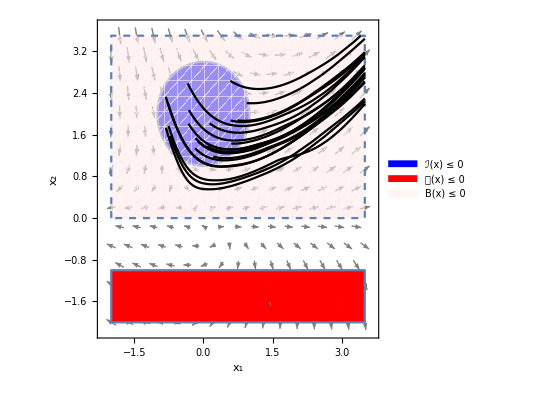

SDP CPU-time elapsed: 0.032418s

Total CPU-time elapsed: 2.8354s

```mathematica
(*main procedure for synthesizing BCs, drop the bcTempDefault argument if you'd like a general polynomial template*)
main[varSet2,flowVec2,domainRange2,initialBoundary2,unsafeBoundary2,barrierDegree2,polyDegrees2,paraRange2,LieOrder2,ϵI2,ϵU2,ϵL2,ϵ2,δ2,bilinearUnsafeCons2,posteriorCheck2,verbose2,bcTempDefault2];
```

### contrived

```mathematica
varSet1={Subscript[x, 1],Subscript[x, 2]};
flowVec1={-Subscript[x, 1]+Subscript[x, 2],-Subscript[x, 2]};
domainRange1={0,2};
initialBoundary1=(Subscript[x, 1]-1.125)^2+(Subscript[x, 2]-0.625)^2-0.0125;
unsafeBoundary1=(Subscript[x, 1]-0.875)^2+(Subscript[x, 2]-0.125)^2-0.0125;
barrierDegree1=2;
polyDegrees1={2,2,0};
paraRange1={-10,10};
LieOrder1=1;
ϵI1=ϵL1=0;
ϵU1=N[10^-2];
ϵ1=N[10^-3];
δ1=-N[10^-3];
bilinearUnsafeCons1=False;
posteriorCheck1=True;
verbose1=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-2 a_20 x_1^2+(-a_01+a_10) x_2+(-2 a_02+a_11) x_2^2+x_1 (-a_10+(-2 a_11+2 a_20) x_2)}

SOS constraints:
{w_00+w_20 x_1^2+w_01 x_2+w_02 x_2^2+x_1 (w_10+w_11 x_2),u_00+u_20 x_1^2+u_01 x_2+u_02 x_2^2+x_1 (u_10+u_11 x_2),-a_00+1.64375 w_00+w_20 x_1^4+(-a_01-1.25 w_00+1.64375 w_01) x_2+(-a_02+w_00-1.25 w_01+1.64375 w_02) x_2^2+(w_01-1.25 w_02) x_2^3+w_02 x_2^4+x_1^3 (w_10-2.25 w_20+w_11 x_2)+x_1^2 (-a_20+w_00-2.25 w_10+1.64375 w_20+(w_01-2.25 w_11-1.25 w_20) x_2+(w_02+w_20) x_2^2)+x_1 (-a_10-2.25 w_00+1.64375 w_10+(-a_11-2.25 w_01-1.25 w_10+1.64375 w_11) x_2+(-2.25 w_02+w_10-1.25 w_11) x_2^2+w_11 x_2^3),-0.01+a_00+0.76875 u_00+u_20 x_1^4+(a_01-0.25 u_00+0.76875 u_01) x_2+(a_02+u_00-0.25 u_01+0.76875 u_02) x_2^2+(u_01-0.25 u_02) x_2^3+u_02 x_2^4+x_1^3 (u_10-1.75 u_20+u_11 x_2)+x_1^2 (a_20+u_00-1.75 u_10+0.76875 u_20+(u_01-1.75 u_11-0.25 u_20) x_2+(u_02+u_20) x_2^2)+x_1 (a_10-1.75 u_00+0.76875 u_10+(a_11-1.75 u_01-0.25 u_10+0.76875 u_11) x_2+(-1.75 u_02+u_10-0.25 u_11) x_2^2+u_11 x_2^3),a_00 v10_00+a_20 (2+v10_00) x_1^2+(-a_10+a_01 (1+v10_00)) x_2+(-a_11+a_02 (2+v10_00)) x_2^2+x_1 (a_10 (1+v10_00)+(-2 a_20+a_11 (2+v10_00)) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,w_01,w_02,w_10,w_11,w_20,u_00,u_01,u_02,u_10,u_11,u_20,v10_00}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,w_01→z_9,w_02→z_10,w_10→z_11,w_11→z_12,w_20→z_13,u_00→z_14,u_01→z_15,u_02→z_16,u_10→z_17,u_11→z_18,u_20→z_19,v10_00→z_20}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,0,0,0,0,0,1,0,0,0,0,0,-1}

Initial feasible solution:
z^0={z_1→-0.0208338,z_2→-0.32816,z_3→0.404568,z_4→0.100732,z_5→-0.243322,z_6→0.0778535,z_7→1.3366×10^-8,z_8→1,z_9→0,z_10→0,z_11→0,z_12→0,z_13→0,z_14→1,z_15→0,z_16→0,z_17→0,z_18→0,z_19→0,z_20→-1}

Initial maximum:
λ^0=1.3366×10^-8

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,w_01,w_02,w_10,w_11,w_20,u_00,u_01,u_02,u_10,u_11,u_20,v10_00,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,w_01→z_9,w_02→z_10,w_10→z_11,w_11→z_12,w_20→z_13,u_00→z_14,u_01→z_15,u_02→z_16,u_10→z_17,u_11→z_18,u_20→z_19,v10_00→z_20,ζ→zz}

Barrier certificate candidate:
-0.0208338+0.100732 x_1+0.0778535 x_1^2-0.32816 x_2-0.243322 x_1 x_2+0.404568 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

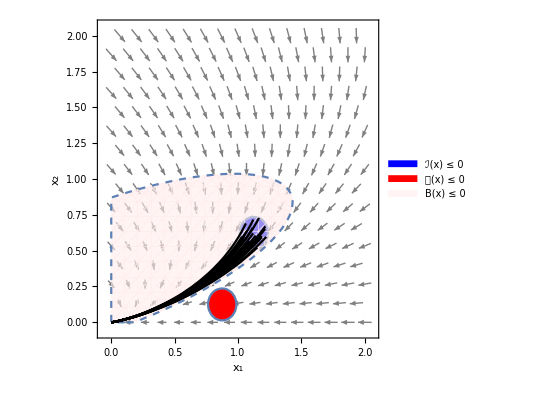

SDP CPU-time elapsed: 0.010647s

Total CPU-time elapsed: 1.43781s

```mathematica
main[varSet1,flowVec1,domainRange1,initialBoundary1,unsafeBoundary1,barrierDegree1,polyDegrees1,paraRange1,LieOrder1,ϵI1,ϵU1,ϵL1,ϵ1,δ1,bilinearUnsafeCons1,posteriorCheck1,verbose1];
```

### lie-der

```mathematica
varSet4={Subscript[x, 1],Subscript[x, 2]};
flowVec4={-2 Subscript[x, 2],Subscript[x, 1]^2};
domainRange4={-2,2};
initialBoundary4=(Subscript[x, 1]+1)^2+(Subscript[x, 2]-0.5)^2-0.16;
unsafeBoundary4=(Subscript[x, 1]+1)^2+(Subscript[x, 2]+0.5)^2-0.16;
barrierDegree4=1;
polyDegrees4={0,0,1};
paraRange4={-10,10};
LieOrder4=1;
ϵI4=ϵU4=ϵL4=N[10^-3];
ϵ4=N[10^-6];
δ4=-N[10^-3];
bilinearUnsafeCons4=False;
posteriorCheck4=True;
verbose4=False;
```

Template BC: 
a_00+a_10 x_1+a_01 x_2

Lie sequence: 
{a_00+a_10 x_1+a_01 x_2,a_01 x_1^2-2 a_10 x_2}

SOS constraints:
{w_00,u_00,-0.001-a_00+1.09 w_00+(-a_10+2 w_00) x_1+w_00 x_1^2+(-a_01-1. w_00) x_2+w_00 x_2^2,-0.001+a_00+1.09 u_00+(a_10+2 u_00) x_1+u_00 x_1^2+(a_01+1. u_00) x_2+u_00 x_2^2,-0.001+a_00 v10_00+(-a_01+a_10 v10_10) x_1^2+(2 a_10+a_01 v10_00+a_00 v10_01) x_2+a_01 v10_01 x_2^2+x_1 (a_10 v10_00+a_00 v10_10+(a_10 v10_01+a_01 v10_10) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9}

Initial vector:
{a_00,a_01,a_10,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.421691,z_2→-0.835563,z_3→-0.417781,z_4→2.64081×10^-8,z_5→1,z_6→1,z_7→-1,z_8→0,z_9→0}

Initial maximum:
λ^0=2.64081×10^-8

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9,ζ→zz}

Barrier certificate candidate:
-0.421691-0.417781 x_1-0.835563 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

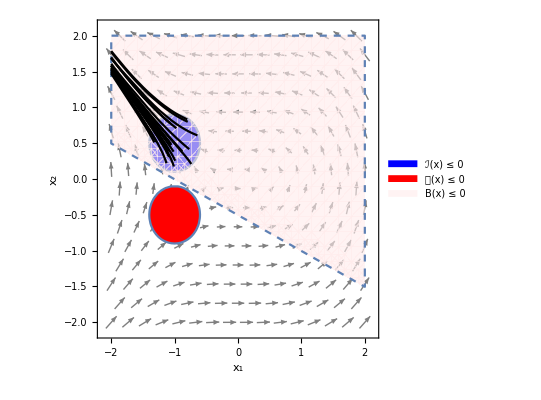

SDP CPU-time elapsed: 0.046715s

Total CPU-time elapsed: 0.946114s

```mathematica
main[varSet4,flowVec4,domainRange4,initialBoundary4,unsafeBoundary4,barrierDegree4,polyDegrees4,paraRange4,LieOrder4,ϵI4,ϵU4,ϵL4,ϵ4,δ4,bilinearUnsafeCons4,posteriorCheck4,verbose4];
```

### lorenz

```mathematica
varSet5={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
flowVec5={10.0(-Subscript[x, 1]+Subscript[x, 2]),-Subscript[x, 2]+Subscript[x, 1] (28.0-Subscript[x, 3]),Subscript[x, 1] Subscript[x, 2]-(8 Subscript[x, 3])/3};
domainRange5={-20,20};
initialBoundary5=-0.25+(14.5+Subscript[x, 1])^2+(14.5+Subscript[x, 2])^2+(-12.5+Subscript[x, 3])^2;
unsafeBoundary5=-0.25+(16.5+Subscript[x, 1])^2+(14.5+Subscript[x, 2])^2+(-2.5+Subscript[x, 3])^2;
(*bcTempDefault5=Subscript[a, 000]+Subscript[a, 100] Subscript[x, 1]+Subscript[a, 200] Subscript[x, 1]^2+Subscript[a, 001] Subscript[x, 3];
barrierDegree5=polyDegree[bcTempDefault5,varSet5];*)
barrierDegree5=2;
polyDegrees5={0,0,1};
paraRange5={-1,1};
LieOrder5=1;
ϵI5=ϵU5=ϵL5=N[10^-3];
ϵ5=N[10^-6];
δ5=-N[10^-3];
bilinearUnsafeCons5=False;
posteriorCheck5=True;
verbose5=False;
```

```mathematica
main[varSet5,flowVec5,domainRange5,initialBoundary5,unsafeBoundary5,barrierDegree5,polyDegrees5,paraRange5,LieOrder5,ϵI5,ϵU5,ϵL5,ϵ5,δ5,bilinearUnsafeCons5,posteriorCheck5,verbose5];
```

Template BC: 
a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2

Lie sequence: 
{a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2,(-2 a_020+10. a_110) x_2^2-8/3 a_001 x_3-16/3 a_002 x_3^2+x_2 (-a_010+10. a_100-3.66667 (a_011-2.72727 a_101) x_3)+x_1^2 (28. a_110-20. a_200+a_101 x_2-a_110 x_3)+x_1 (28. a_010-10. a_100+a_011 x_2^2+(-a_010+28. a_011-12.6667 a_101) x_3-a_011 x_3^2+x_2 (a_001+56. a_020-11. a_110+20. a_200+2 (a_002-a_020) x_3))}

SOS constraints:
{w_000,u_000,-0.001-a_000+576.5 w_000+(-a_200+w_000) x_1^2+(-a_020+w_000) x_2^2+(-a_001-25. w_000) x_3+(-a_002+w_000) x_3^2+x_2 (-a_010+29. w_000-a_011 x_3)+x_1 (-a_100+29. w_000-a_110 x_2-a_101 x_3),-0.001+a_000+488.5 u_000+(a_200+u_000) x_1^2+(a_020+u_000) x_2^2+(a_001-5. u_000) x_3+(a_002+u_000) x_3^2+x_2 (a_010+29. u_000+a_011 x_3)+x_1 (a_100+33. u_000+a_110 x_2+a_101 x_3),-0.001+a_000 v10_000+a_200 v10_100 x_1^3+a_020 v10_010 x_2^3+(a_001 (8/3+v10_000)+a_000 v10_001) x_3+(a_002 (16/3+v10_000)+a_001 v10_001) x_3^2+a_002 v10_001 x_3^3+x_2^2 (-10. a_110+a_020 (2+v10_000)+a_010 v10_010+(a_020 v10_001+a_011 v10_010) x_3)+x_1^2 (-28. a_110+a_200 (20.+v10_000)+a_100 v10_100+(-a_101+a_200 v10_010+a_110 v10_100) x_2+(a_110+a_200 v10_001+a_101 v10_100) x_3)+x_2 (-10. a_100+a_010 (1+v10_000)+a_000 v10_010+(-10. a_101+a_011 (3.66667+v10_000)+a_010 v10_001+a_001 v10_010) x_3+(a_011 v10_001+a_002 v10_010) x_3^2)+x_1 (-28. a_010+a_100 (10.+v10_000)+a_000 v10_100+(-a_011+a_110 v10_010+a_020 v10_100) x_2^2+(a_010-28. a_011+12.6667 a_101+a_101 v10_000+a_100 v10_001+a_001 v10_100) x_3+(a_011+a_101 v10_001+a_002 v10_100) x_3^2+x_2 (-a_001-56. a_020+11. a_110-20. a_200+a_110 v10_000+a_100 v10_010+a_010 v10_100+(-2 a_002+2 a_020+a_110 v10_001+a_101 v10_010+a_011 v10_100) x_3))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17}

Initial vector:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-0.325894,z_2→-0.023822,z_3→0.000542765,z_4→0.00380387,z_5→-0.0000568394,z_6→0.000212731,z_7→-0.00667617,z_8→0.000310007,z_9→-0.000648497,z_10→0.00227624,z_11→-0.000164882,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0}

Initial maximum:
λ^0=-0.000164882

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17,ζ→zz}

Feasible solution:
z^1={z_1→-0.322124,z_2→-0.0249281,z_3→0.000419954,z_4→0.00130927,z_5→-9.51815×10^-6,z_6→0.000169525,z_7→-0.00371955,z_8→0.000154765,z_9→-0.000477808,z_10→0.00214766,z_11→-0.000133842,z_12→0.993025,z_13→0.894031,z_14→-1.,z_15→-0.0122582,z_16→0.00183224,z_17→0.0000778178,zz→-5.73114×10^-6}

Maximum:
(λ+ζ)^1=-0.000139573

|z^1-z^0|=0.107062

Feasible solution:
z^2={z_1→-0.321076,z_2→-0.0295153,z_3→0.000338281,z_4→-0.000699813,z_5→0.000014467,z_6→0.000162606,z_7→-0.00155888,z_8→0.000073581,z_9→-0.000333606,z_10→0.00215363,z_11→-0.0000965252,z_12→0.999799,z_13→0.899643,z_14→-1.,z_15→-0.024298,z_16→0.00329655,z_17→0.000113699,zz→-5.3876×10^-6}

Maximum:
(λ+ζ)^2=-0.000101913

|z^2-z^1|=0.0159798

Feasible solution:
z^3={z_1→-0.323693,z_2→-0.0346014,z_3→0.000262108,z_4→-0.00180753,z_5→0.000026325,z_6→0.000157902,z_7→-0.000548204,z_8→0.0000387928,z_9→-0.00020547,z_10→0.00217783,z_11→-0.0000602657,z_12→0.999838,z_13→0.911584,z_14→-1.,z_15→-0.0351018,z_16→0.00440518,z_17→0.00012042,zz→-4.62972×10^-6}

Maximum:
(λ+ζ)^3=-0.0000648955

|z^3-z^2|=0.0171911

Feasible solution:
z^4={z_1→-0.328847,z_2→-0.0392768,z_3→0.000219575,z_4→-0.00221991,z_5→0.0000231049,z_6→0.000159099,z_7→-0.000295268,z_8→0.0000304171,z_9→-0.000123131,z_10→0.00222465,z_11→-0.000034149,z_12→0.99985,z_13→0.93135,z_14→-1.,z_15→-0.0431291,z_16→0.00524617,z_17→0.00014692,zz→-3.46278×10^-6}

Maximum:
(λ+ζ)^4=-0.0000376118

|z^4-z^3|=0.0224614

Feasible solution:
z^5={z_1→-0.33493,z_2→-0.0433353,z_3→0.000211049,z_4→-0.00237694,z_5→0.0000168256,z_6→0.000172354,z_7→-0.000274307,z_8→0.0000275752,z_9→-0.0000765027,z_10→0.00226695,z_11→-0.0000202467,z_12→0.999859,z_13→0.949465,z_14→-1.,z_15→-0.0485638,z_16→0.00587483,z_17→0.000205241,zz→-2.74446×10^-6}

Maximum:
(λ+ζ)^5=-0.0000229911

|z^5-z^4|=0.0202882

Feasible solution:
z^6={z_1→-0.34067,z_2→-0.0466746,z_3→0.000220565,z_4→-0.00246525,z_5→0.0000124521,z_6→0.000192839,z_7→-0.000302813,z_8→0.0000259168,z_9→-0.0000497743,z_10→0.00229575,z_11→-0.0000135735,z_12→0.999864,z_13→0.961973,z_14→-1.,z_15→-0.0522773,z_16→0.00634407,z_17→0.000277544,zz→-2.52017×10^-6}

Maximum:
(λ+ζ)^6=-0.0000160937

|z^6-z^5|=0.0146477

Feasible solution:
z^7={z_1→-0.345355,z_2→-0.0493201,z_3→0.000236411,z_4→-0.00252641,z_5→9.7998×10^-6,z_6→0.000214697,z_7→-0.000338439,z_8→0.0000249428,z_9→-0.0000334819,z_10→0.0023134,z_11→-0.0000102105,z_12→0.999865,z_13→0.969903,z_14→-1.,z_15→-0.0549461,z_16→0.00670467,z_17→0.000351347,zz→-2.53985×10^-6}

Maximum:
(λ+ζ)^7=-0.0000127504

|z^7-z^6|=0.0099548

Feasible solution:
z^8={z_1→-0.348744,z_2→-0.0513583,z_3→0.00025274,z_4→-0.00257086,z_5→8.17337×10^-6,z_6→0.000234615,z_7→-0.000371013,z_8→0.000024388,z_9→-0.0000229177,z_10→0.00232307,z_11→-8.35017×10^-6,z_12→0.999863,z_13→0.974946,z_14→-1.,z_15→-0.0569735,z_16→0.00699287,z_17→0.000422105,zz→-2.64208×10^-6}

Maximum:
(λ+ζ)^8=-0.0000109922

|z^8-z^7|=0.00672863

Barrier certificate candidate:
-0.348744-0.000371013 x_1+0.00232307 x_1^2-0.00257086 x_2-0.0000229177 x_1 x_2+0.000234615 x_2^2-0.0513583 x_3+0.000024388 x_1 x_3+8.17337×10^-6 x_2 x_3+0.00025274 x_3^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 2.57361s

Total CPU-time elapsed: 12.6317s

### lti-stable

```mathematica
varSet7={Subscript[x, 1],Subscript[x, 2]};
flowVec7={-0.1 Subscript[x, 1]-10 Subscript[x, 2],4 Subscript[x, 1]-2 Subscript[x, 2]};
domainRange7={-2,2};
initialBoundary7=(Subscript[x, 1]-1.125)^2+(Subscript[x, 2]-0.625)^2-0.125^2;
unsafeBoundary7=(Subscript[x, 1]+1.5)^2+(Subscript[x, 2]+1.25)^2-0.25^2;
barrierDegree7=2;
polyDegrees7={0,0,1};
paraRange7={-10,10};
LieOrder7=1;
ϵI7=ϵU7=ϵL7=N[10^-3];
ϵ7=N[10^-6];
δ7=-N[10^-3];
bilinearUnsafeCons7=False;
posteriorCheck7=True;
verbose7=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,(4 a_11-0.2 a_20) x_1^2-2 (a_01+5 a_10) x_2-2 (2 a_02+5 a_11) x_2^2+x_1 (4 a_01-0.1 a_10+(8 a_02-2.1 a_11-20 a_20) x_2)}

SOS constraints:
{w_00,u_00,-0.001-a_00+1.64063 w_00+(-a_20+w_00) x_1^2+(-a_01-1.25 w_00) x_2+(-a_02+w_00) x_2^2+x_1 (-a_10-2.25 w_00-a_11 x_2),-0.001+a_00+3.75 u_00+(a_20+u_00) x_1^2+(a_01+2.5 u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10+3. u_00+a_11 x_2),-0.001+a_00 v10_00+a_20 v10_10 x_1^3+(10 a_10+a_01 (2+v10_00)+a_00 v10_01) x_2+(10 a_11+a_02 (4+v10_00)+a_01 v10_01) x_2^2+a_02 v10_01 x_2^3+x_1^2 (-4 a_11+a_20 (0.2+v10_00)+a_10 v10_10+(a_20 v10_01+a_11 v10_10) x_2)+x_1 (-4 a_01+a_10 (0.1+v10_00)+a_00 v10_10+(-8 a_02+20 a_20+a_11 (2.1+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_11 v10_01+a_02 v10_10) x_2^2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.893409,z_2→-0.150189,z_3→0.663497,z_4→-0.0663279,z_5→-0.132079,z_6→0.256836,z_7→2.2714×10^-8,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=2.2714×10^-8

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Barrier certificate candidate:
-0.893409-0.0663279 x_1+0.256836 x_1^2-0.150189 x_2-0.132079 x_1 x_2+0.663497 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

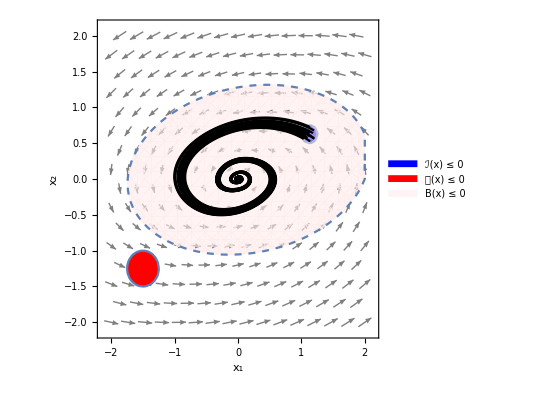

SDP CPU-time elapsed: 0.008787s

Total CPU-time elapsed: 1.58266s

```mathematica
main[varSet7,flowVec7,domainRange7,initialBoundary7,unsafeBoundary7,barrierDegree7,polyDegrees7,paraRange7,LieOrder7,ϵI7,ϵU7,ϵL7,ϵ7,δ7,bilinearUnsafeCons7,posteriorCheck7,verbose7];
```

### lotka-volterra

```mathematica
varSet8={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
flowVec8={Subscript[x, 1](1-Subscript[x, 3]),Subscript[x, 2](1-2 Subscript[x, 3]),Subscript[x, 3](-1+Subscript[x, 1]+Subscript[x, 2])};
domainRange8={-2,2};
initialBoundary8=-0.64+(-1+Subscript[x, 1])^2+(-1+Subscript[x, 2])^2+Subscript[x, 3]^2;
unsafeBoundary8=-0.25+Subscript[x, 1]^2+(1+Subscript[x, 2])^2;
bcTempDefault8=Subscript[a, 01] Subscript[x, 2];
barrierDegree8=polyDegree[bcTempDefault8,varSet8];
polyDegrees8={0,0,1};
paraRange8={-1,1};
LieOrder8=1;
ϵI8=ϵU8=ϵL8=N[10^-3];
ϵ8=N[10^-2];
δ8=-N[10^-3];
bilinearUnsafeCons8=False;
posteriorCheck8=True;
verbose8=False;
```

```mathematica
main[varSet8,flowVec8,domainRange8,initialBoundary8,unsafeBoundary8,barrierDegree8,polyDegrees8,paraRange8,LieOrder8,ϵI8,ϵU8,ϵL8,ϵ8,δ8,bilinearUnsafeCons8,posteriorCheck8,verbose8,bcTempDefault8];
```

Template BC: 
a_01 x_2

Lie sequence: 
{a_01 x_2,x_2 (a_01-2 a_01 x_3)}

SOS constraints:
{w_000,u_000,-0.001+1.36 w_000-2 w_000 x_1+w_000 x_1^2+(-a_01-2 w_000) x_2+w_000 x_2^2+w_000 x_3^2,-0.001+0.75 u_000+u_000 x_1^2+(a_01+2 u_000) x_2+u_000 x_2^2,-0.001+a_01 v10_100 x_1 x_2+a_01 v10_010 x_2^2+x_2 (a_01 (-1+v10_000)+a_01 (2+v10_001) x_3)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_01,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_01→z_1,λ→z_2,w_000→z_3,u_000→z_4,v10_000→z_5,v10_001→z_6,v10_010→z_7,v10_100→z_8}

Initial vector:
{a_01,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-0.139783,z_2→-0.197933,z_3→1,z_4→1,z_5→-1,z_6→0,z_7→0,z_8→0}

Initial maximum:
λ^0=-0.197933

LMI variables:
{a_01,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_01→z_1,λ→z_2,w_000→z_3,u_000→z_4,v10_000→z_5,v10_001→z_6,v10_010→z_7,v10_100→z_8,ζ→zz}

Feasible solution:
z^1={z_1→-0.000378202,z_2→-0.0034366,z_3→0.0127247,z_4→0.0230179,z_5→-0.987501,z_6→-0.00814964,z_7→-0.0500757,z_8→0.,zz→-0.0009946}

Maximum:
(λ+ζ)^1=-0.0044312

|z^1-z^0|=1.41039

Feasible solution:
z^2={z_1→-2.31171×10^-6,z_2→-0.00100002,z_3→0.00212867,z_4→0.00300939,z_5→-0.987337,z_6→-0.0000172599,z_7→-0.0000749162,z_8→0.,zz→-0.00102411}

Maximum:
(λ+ζ)^2=-0.00202413

|z^2-z^1|=0.0555422

Feasible solution:
z^3={z_1→-2.91585×10^-6,z_2→-0.00100001,z_3→0.00212958,z_4→0.00301172,z_5→-0.987472,z_6→-2.09273×10^-7,z_7→-0.0000720957,z_8→0.,zz→-0.0010241}

Maximum:
(λ+ζ)^3=-0.00202411

|z^3-z^2|=0.000136259

Close enough solutions: 0.000136259 ≤ ϵ = 0.01

Barrier certificate candidate:
-2.91585×10^-6 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 0.06705s

Total CPU-time elapsed: 0.540797s

### clock

```mathematica
varSetC1={Subscript[x, 1],Subscript[x, 2]};
flowVecC1={-Subscript[x, 1]+ 2 Subscript[x, 1]^2  Subscript[x, 2],-Subscript[x, 2]};
domainRangeC1={-1.5,5.5};
initialBoundaryC1=(8 Subscript[x, 1] - 33)^2 + Subscript[x, 2]^2 - 1;
unsafeBoundaryC1=(Subscript[x, 1] - 1.5)^2 + (Subscript[x, 2] - 2.5)^2 - 0.5^2;
barrierDegreeC1=1;
polyDegreesC1={0,0,1};
paraRangeC1={-10,10};
LieOrderC1=1;
ϵIC1=ϵUC1=ϵLC1=N[10^-3];
ϵC1=N[10^-6];
δC1=-N[10^-3];
bilinearUnsafeConsC1=False;
posteriorCheckC1=True;
verboseC1=False;
```

Template BC: 
a_00+a_10 x_1+a_01 x_2

Lie sequence: 
{a_00+a_10 x_1+a_01 x_2,-a_10 x_1-a_01 x_2+2 a_10 x_1^2 x_2}

SOS constraints:
{w_00,u_00,-0.001-a_00+1088 w_00+(-a_10-528 w_00) x_1+64 w_00 x_1^2-a_01 x_2+w_00 x_2^2,-0.001+a_00+8.25 u_00+(a_10-3. u_00) x_1+u_00 x_1^2+(a_01-5. u_00) x_2+u_00 x_2^2,-0.001+a_00 v10_00+(a_01 (1+v10_00)+a_00 v10_01) x_2+a_01 v10_01 x_2^2+x_1^2 (a_10 v10_10-2 a_10 x_2)+x_1 (a_10 (1+v10_00)+a_00 v10_10+(a_10 v10_01+a_01 v10_10) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9}

Initial vector:
{a_00,a_01,a_10,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-3.68427,z_2→2.54327,z_3→-1.76345×10^-16,z_4→2.46442×10^-7,z_5→1,z_6→1,z_7→-1,z_8→0,z_9→0}

Initial maximum:
λ^0=2.46442×10^-7

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9,ζ→zz}

Barrier certificate candidate:
-3.68427-1.76345×10^-16 x_1+2.54327 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

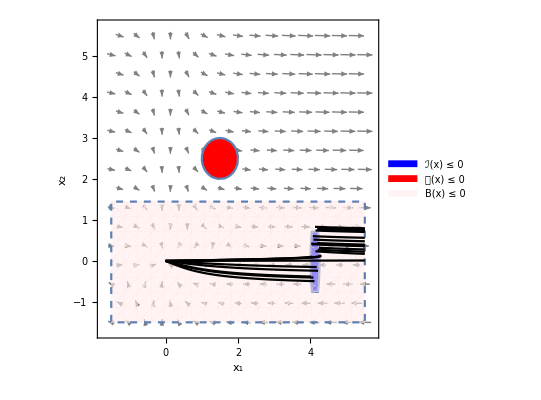

SDP CPU-time elapsed: 0.012529s

Total CPU-time elapsed: 0.776111s

```mathematica
main[varSetC1,flowVecC1,domainRangeC1,initialBoundaryC1,unsafeBoundaryC1,barrierDegreeC1,polyDegreesC1,paraRangeC1,LieOrderC1,ϵIC1,ϵUC1,ϵLC1,ϵC1,δC1,bilinearUnsafeConsC1,posteriorCheckC1,verboseC1];
```

### lyapunov

```mathematica
varSetC2={Subscript[x, 1],Subscript[x, 2], Subscript[x, 3]};
flowVecC2={-Subscript[x, 2],-Subscript[x, 3],-Subscript[x, 1]-2 Subscript[x, 2] - Subscript[x, 3] + Subscript[x, 1]^3};
domainRangeC2={-2,2};
initialBoundaryC2=(Subscript[x, 1] - 0.25)^2 + (Subscript[x, 2] - 0.25)^2 + (Subscript[x, 3]-0.25)^2- 0.5^2;
unsafeBoundaryC2=(Subscript[x, 1] - 1.5)^2 + (Subscript[x, 2] + 1.5)^2 +(Subscript[x, 3]+ 1.5)^2- 0.5^2;
barrierDegreeC2=2;
polyDegreesC2={0,0,1};
paraRangeC2={-1,1};
LieOrderC2=1;
ϵIC2=ϵUC2=ϵLC2=N[10^-3];
ϵC2=N[10^-2];
δC2=-N[10^-3];
bilinearUnsafeConsC2=False;
posteriorCheckC2=True;
verboseC2=False;
```

```mathematica
main[varSetC2,flowVecC2,domainRangeC2,initialBoundaryC2,unsafeBoundaryC2,barrierDegreeC2,polyDegreesC2,paraRangeC2,LieOrderC2,ϵIC2,ϵUC2,ϵLC2,ϵC2,δC2,bilinearUnsafeConsC2,posteriorCheckC2,verboseC2];
```

Template BC: 
a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2

Lie sequence: 
{a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2,-a_101 x_1^2+a_101 x_1^4+(-2 a_011-a_110) x_2^2+(-a_001-a_010) x_3+(-2 a_002-a_011) x_3^2+x_1^3 (a_001+a_011 x_2+2 a_002 x_3)+x_2 (-2 a_001-a_100+(-4 a_002-a_011-2 a_020-a_101) x_3)+x_1 (-a_001+(-a_011-2 (a_101+a_200)) x_2+(-2 a_002-a_101-a_110) x_3)}

SOS constraints:
{w_000,u_000,-0.001-a_000-0.0625 w_000+(-a_200+w_000) x_1^2+(-a_020+w_000) x_2^2+(-a_001-0.5 w_000) x_3+(-a_002+w_000) x_3^2+x_2 (-a_010-0.5 w_000-a_011 x_3)+x_1 (-a_100-0.5 w_000-a_110 x_2-a_101 x_3),-0.001+a_000+6.5 u_000+(a_200+u_000) x_1^2+(a_020+u_000) x_2^2+(a_001+3. u_000) x_3+(a_002+u_000) x_3^2+x_2 (a_010+3. u_000+a_011 x_3)+x_1 (a_100-3. u_000+a_110 x_2+a_101 x_3),-0.001+a_000 v10_000-a_101 x_1^4+a_020 v10_010 x_2^3+(a_010+a_001 (1+v10_000)+a_000 v10_001) x_3+(a_011+a_002 (2+v10_000)+a_001 v10_001) x_3^2+a_002 v10_001 x_3^3+x_1^3 (-a_001+a_200 v10_100-a_011 x_2-2 a_002 x_3)+x_2^2 (2 a_011+a_110+a_020 v10_000+a_010 v10_010+(a_020 v10_001+a_011 v10_010) x_3)+x_1^2 (a_101+a_200 v10_000+a_100 v10_100+(a_200 v10_010+a_110 v10_100) x_2+(a_200 v10_001+a_101 v10_100) x_3)+x_2 (2 a_001+a_100+a_010 v10_000+a_000 v10_010+(4 a_002+2 a_020+a_101+a_011 (1+v10_000)+a_010 v10_001+a_001 v10_010) x_3+(a_011 v10_001+a_002 v10_010) x_3^2)+x_1 (a_001+a_100 v10_000+a_000 v10_100+(a_110 v10_010+a_020 v10_100) x_2^2+(2 a_002+a_110+a_101 (1+v10_000)+a_100 v10_001+a_001 v10_100) x_3+(a_101 v10_001+a_002 v10_100) x_3^2+x_2 (a_011+2 (a_101+a_200)+a_110 v10_000+a_100 v10_010+a_010 v10_100+(a_110 v10_001+a_101 v10_010+a_011 v10_100) x_3))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17}

Initial vector:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-0.230078,z_2→-5.13989×10^-10,z_3→0.00670157,z_4→-0.144127,z_5→0.0329718,z_6→-0.0164856,z_7→0.0915851,z_8→-0.025443,z_9→-0.0187056,z_10→-0.0351678,z_11→-0.0091539,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0}

Initial maximum:
λ^0=-0.0091539

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17,ζ→zz}

Feasible solution:
z^1={z_1→-0.119784,z_2→-0.000870353,z_3→0.00146557,z_4→-0.0518907,z_5→0.00596767,z_6→-0.0124562,z_7→0.0704291,z_8→-0.00295718,z_9→0.0103611,z_10→-0.0152686,z_11→-0.00232787,z_12→0.456952,z_13→0.0465791,z_14→-1.,z_15→0.00456971,z_16→0.00524804,z_17→-0.00363948,zz→-0.000613831}

Maximum:
(λ+ζ)^1=-0.0029417

|z^1-z^0|=1.108

Feasible solution:
z^2={z_1→-0.035861,z_2→9.36079×10^-6,z_3→0.000446169,z_4→-0.014751,z_5→0.00215303,z_6→-0.00397882,z_7→0.0234534,z_8→-0.000881508,z_9→0.00333381,z_10→-0.00548931,z_11→-0.000820401,z_12→0.130765,z_13→0.0137163,z_14→-1.,z_15→0.00500137,z_16→0.0107673,z_17→0.00263904,zz→-0.000895379}

Maximum:
(λ+ζ)^2=-0.00171578

|z^2-z^1|=0.344117

Feasible solution:
z^3={z_1→-0.00119954,z_2→2.2054×10^-6,z_3→0.0000892488,z_4→-0.000010194,z_5→0.00040152,z_6→0.0000697128,z_7→0.000160986,z_8→-0.000192457,z_9→-0.0005212,z_10→-0.000381642,z_11→-0.000147392,z_12→0.0014366,z_13→0.00230548,z_14→-1.,z_15→0.00580286,z_16→0.0120749,z_17→0.00568373,zz→-0.00103894}

Maximum:
(λ+ζ)^3=-0.00118633

|z^3-z^2|=0.137442

Feasible solution:
z^4={z_1→-0.000977052,z_2→-0.0000116085,z_3→0.0000672489,z_4→-0.000107448,z_5→0.000308756,z_6→0.000122173,z_7→-9.82724×10^-6,z_8→-0.000241406,z_9→-0.000493944,z_10→-0.000237463,z_11→-0.0000872635,z_12→0.000380132,z_13→0.00211618,z_14→-1.,z_15→0.0059785,z_16→0.012003,z_17→0.00545054,zz→-0.00104025}

Maximum:
(λ+ζ)^4=-0.00112751

|z^4-z^3|=0.00117049

Close enough solutions: 0.00117049 ≤ ϵ = 0.01

Barrier certificate candidate:
-0.000977052-9.82724×10^-6 x_1-0.000237463 x_1^2-0.000107448 x_2-0.000493944 x_1 x_2+0.000122173 x_2^2-0.0000116085 x_3-0.000241406 x_1 x_3+0.000308756 x_2 x_3+0.0000672489 x_3^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 1.27819s

Total CPU-time elapsed: 5.14256s

### arch1

```mathematica
varSetC3={Subscript[x, 1],Subscript[x, 2]};
flowVecC3={-Subscript[x, 1]+ 2 Subscript[x, 1]^3  Subscript[x, 2]^2,-Subscript[x, 2]};
domainRangeC3={-2,2};
initialBoundaryC3=Subscript[x, 1]^2 + (Subscript[x, 2] - 0.5)^2 - 0.2^2;
unsafeBoundaryC3=(Subscript[x, 1] + 1.5)^2 + (Subscript[x, 2] + 1.5)^2 - 0.5^2;
barrierDegreeC3=2;
polyDegreesC3={0,0,1};
paraRangeC3={-10,10};
LieOrderC3=1;
ϵIC3=ϵUC3=ϵLC3=N[10^-3];
ϵC3=N[10^-6];
δC3=-N[10^-3];
bilinearUnsafeConsC3=False;
posteriorCheckC3=True;
verboseC3=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-2 a_20 x_1^2-a_01 x_2-2 a_02 x_2^2+4 a_20 x_1^4 x_2^2+x_1 (-a_10-2 a_11 x_2)+x_1^3 (2 a_10 x_2^2+2 a_11 x_2^3)}

SOS constraints:
{w_00,u_00,-0.001-a_00+0.21 w_00+(-a_20+w_00) x_1^2+(-a_01-1. w_00) x_2+(-a_02+w_00) x_2^2+x_1 (-a_10-a_11 x_2),-0.001+a_00+4.25 u_00+(a_20+u_00) x_1^2+(a_01+3. u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10+3. u_00+a_11 x_2),-0.001+a_00 v10_00+(a_01 (1+v10_00)+a_00 v10_01) x_2+(a_02 (2+v10_00)+a_01 v10_01) x_2^2-4 a_20 x_1^4 x_2^2+a_02 v10_01 x_2^3+x_1^2 (a_20 (2+v10_00)+a_10 v10_10+(a_20 v10_01+a_11 v10_10) x_2)+x_1 (a_10 (1+v10_00)+a_00 v10_10+(a_11 (2+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_11 v10_01+a_02 v10_10) x_2^2)+x_1^3 (a_20 v10_10-2 a_10 x_2^2-2 a_11 x_2^3)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-1.1385,z_2→-1.68761,z_3→0.536489,z_4→-1.66577×10^-13,z_5→4.33849×10^-13,z_6→-2.17352×10^-10,z_7→1.30649×10^-8,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=1.30649×10^-8

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Barrier certificate candidate:
-1.1385-1.66577×10^-13 x_1-2.17352×10^-10 x_1^2-1.68761 x_2+4.33849×10^-13 x_1 x_2+0.536489 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

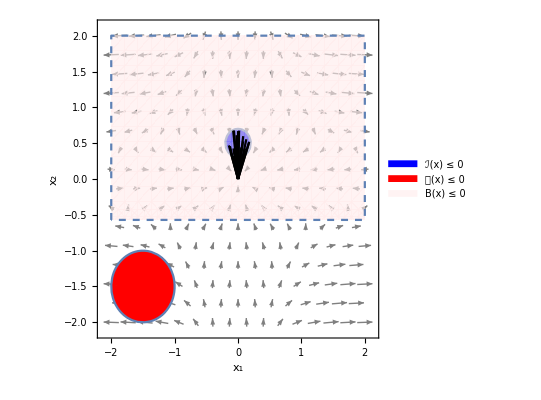

SDP CPU-time elapsed: 0.007901s

Total CPU-time elapsed: 0.820723s

```mathematica
main[varSetC3,flowVecC3,domainRangeC3,initialBoundaryC3,unsafeBoundaryC3,barrierDegreeC3,polyDegreesC3,paraRangeC3,LieOrderC3,ϵIC3,ϵUC3,ϵLC3,ϵC3,δC3,bilinearUnsafeConsC3,posteriorCheckC3,verboseC3];
```

### arch2

```mathematica
varSetC4={Subscript[x, 1],Subscript[x, 2]};
flowVecC4={-1 + Subscript[x, 1]^2 + Subscript[x, 2]^2,5 (-1 + Subscript[x, 1] Subscript[x, 2])};
domainRangeC4={-2,2};
initialBoundaryC4=(Subscript[x, 1]+0.5)^2 + (Subscript[x, 2] + 0.5)^2 - 0.5^2;
unsafeBoundaryC4=(Subscript[x, 1] + 1.5)^2 + (Subscript[x, 2] + 1.5)^2 - 0.5^2;
barrierDegreeC4=2;
polyDegreesC4={0,0,1};
paraRangeC4={-10,10};
LieOrderC4=1;
ϵIC4=ϵUC4=ϵLC4=N[10^-3];
ϵC4=N[10^-1];
δC4=-N[10^-3];
bilinearUnsafeConsC4=False;
posteriorCheckC4=True;
verboseC4=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-5 a_01-a_10+2 a_20 x_1^3+(-10 a_02-a_11) x_2+a_10 x_2^2+a_11 x_2^3+x_1^2 (a_10+6 a_11 x_2)+x_1 (-5 a_11-2 a_20+5 a_01 x_2+2 (5 a_02+a_20) x_2^2)}

SOS constraints:
{w_00,u_00,-0.001-a_00+0.25 w_00+(-a_20+w_00) x_1^2+(-a_01+1. w_00) x_2+(-a_02+w_00) x_2^2+x_1 (-a_10+1. w_00-a_11 x_2),-0.001+a_00+4.25 u_00+(a_20+u_00) x_1^2+(a_01+3. u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10+3. u_00+a_11 x_2),-0.001+5 a_01+a_10+a_00 v10_00+a_20 (-2+v10_10) x_1^3+(10 a_02+a_11+a_01 v10_00+a_00 v10_01) x_2+(-a_10+a_02 v10_00+a_01 v10_01) x_2^2+(-a_11+a_02 v10_01) x_2^3+x_1^2 (a_20 v10_00+a_10 (-1+v10_10)+(a_20 v10_01+a_11 (-6+v10_10)) x_2)+x_1 (5 a_11+2 a_20+a_10 v10_00+a_00 v10_10+(a_11 v10_00+a_10 v10_01+a_01 (-5+v10_10)) x_2+(-2 a_20+a_11 v10_01+a_02 (-10+v10_10)) x_2^2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.926831,z_2→0.0680251,z_3→0.0135944,z_4→-0.980467,z_5→0.0158214,z_6→-0.0235189,z_7→-0.00444591,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=-0.00444591

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Feasible solution:
z^1={z_1→-0.799814,z_2→0.0414525,z_3→0.0087727,z_4→-0.828726,z_5→0.00968842,z_6→-0.0107443,z_7→-0.00252798,z_8→0.811779,z_9→0.829649,z_10→-1.25759,z_11→0.0111752,z_12→0.0303179,zz→-0.0000859677}

Maximum:
(λ+ζ)^1=-0.00261395

|z^1-z^0|=0.414651

Feasible solution:
z^2={z_1→-0.771507,z_2→0.0220106,z_3→0.00565126,z_4→-0.784369,z_5→0.00555419,z_6→-0.00460579,z_7→-0.00111099,z_8→0.781953,z_9→0.789586,z_10→-1.43047,z_11→0.016796,z_12→0.0488025,zz→-0.000172511}

Maximum:
(λ+ζ)^2=-0.0012835

|z^2-z^1|=0.189657

Feasible solution:
z^3={z_1→-0.788414,z_2→0.0127498,z_3→0.00394476,z_4→-0.79446,z_5→0.00343663,z_6→-0.00220444,z_7→-0.000532819,z_8→0.798122,z_9→0.800747,z_10→-1.54896,z_11→0.0198894,z_12→0.0611125,zz→-0.000221739}

Maximum:
(λ+ζ)^3=-0.000754558

|z^3-z^2|=0.122778

Feasible solution:
z^4={z_1→-0.82352,z_2→0.00791202,z_3→0.00292988,z_4→-0.826397,z_5→0.00226694,z_6→-0.00117942,z_7→-0.000279929,z_8→0.832781,z_9→0.832776,z_10→-1.62786,z_11→0.0216136,z_12→0.0699257,zz→-0.000247163}

Maximum:
(λ+ζ)^4=-0.000527093

|z^4-z^3|=0.103978

Feasible solution:
z^5={z_1→-0.861804,z_2→0.00530718,z_3→0.00231901,z_4→-0.863142,z_5→0.00161921,z_6→-0.000720569,z_7→-0.000166244,z_8→0.870423,z_9→0.869176,z_10→-1.67714,z_11→0.0225382,z_12→0.076762,zz→-0.000260809}

Maximum:
(λ+ζ)^5=-0.000427053

|z^5-z^4|=0.0896758

Close enough solutions: 0.0896758 ≤ ϵ = 0.1

Barrier certificate candidate:
-0.861804-0.863142 x_1-0.000720569 x_1^2+0.00530718 x_2+0.00161921 x_1 x_2+0.00231901 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

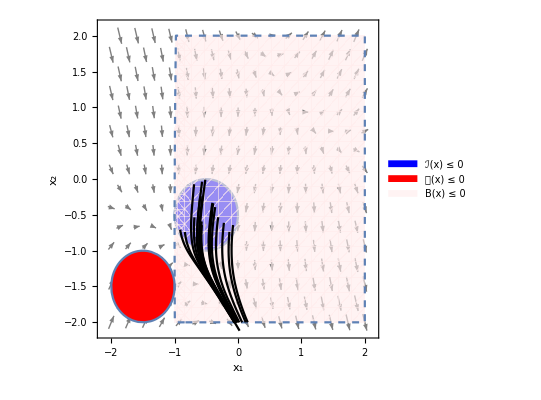

SDP CPU-time elapsed: 0.383862s

Total CPU-time elapsed: 1.24873s

```mathematica
main[varSetC4,flowVecC4,domainRangeC4,initialBoundaryC4,unsafeBoundaryC4,barrierDegreeC4,polyDegreesC4,paraRangeC4,LieOrderC4,ϵIC4,ϵUC4,ϵLC4,ϵC4,δC4,bilinearUnsafeConsC4,posteriorCheckC4,verboseC4];
```

### arch3

```mathematica
varSetC5={Subscript[x, 1],Subscript[x, 2]};
flowVecC5={Subscript[x, 1] - Subscript[x, 1]^3 + Subscript[x, 2] - Subscript[x, 1] Subscript[x, 2]^2 ,-Subscript[x, 1] + Subscript[x, 2] - Subscript[x, 1]^2 Subscript[x, 2] - Subscript[x, 2]^3};
domainRangeC5={-3,3};
initialBoundaryC5=Subscript[x, 1]^2 + Subscript[x, 2]^2 - 0.2^2;
unsafeBoundaryC5=(Subscript[x, 1] - 2.5)^2 + (Subscript[x, 2] - 2.5)^2 - 0.5^2;
barrierDegreeC5=2;
polyDegreesC5={0,0,1};
paraRangeC5={-10,10};
LieOrderC5=1;
ϵIC5=N[10^-2];
ϵLC5=N[10^-3];
ϵUC5=N[5*10^-2];
ϵC5=N[10^1];
δC5=-N[10^-3];
bilinearUnsafeConsC5=False;
posteriorCheckC5=True;
verboseC5=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-2 a_20 x_1^4+(a_01+a_10) x_2+(2 a_02+a_11) x_2^2-a_01 x_2^3-2 a_02 x_2^4+x_1^3 (-a_10-2 a_11 x_2)+x_1^2 (-a_11+2 a_20-a_01 x_2-2 (a_02+a_20) x_2^2)+x_1 (-a_01+a_10+2 (-a_02+a_11+a_20) x_2-a_10 x_2^2-2 a_11 x_2^3)}

SOS constraints:
{w_00,u_00,-0.01-a_00-0.04 w_00+(-a_20+w_00) x_1^2-a_01 x_2+(-a_02+w_00) x_2^2+x_1 (-a_10-a_11 x_2),-0.05+a_00+12.25 u_00+(a_20+u_00) x_1^2+(a_01-5. u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10-5. u_00+a_11 x_2),-0.001+a_00 v10_00+2 a_20 x_1^4+(-a_10+a_01 (-1+v10_00)+a_00 v10_01) x_2+(-a_11+a_02 (-2+v10_00)+a_01 v10_01) x_2^2+(a_01+a_02 v10_01) x_2^3+2 a_02 x_2^4+x_1^3 (a_10+a_20 v10_10+2 a_11 x_2)+x_1^2 (a_11+a_20 (-2+v10_00)+a_10 v10_10+(a_01+a_20 v10_01+a_11 v10_10) x_2+2 (a_02+a_20) x_2^2)+x_1 (a_01+a_10 (-1+v10_00)+a_00 v10_10+(2 a_02-2 a_20+a_11 (-2+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_10+a_11 v10_01+a_02 v10_10) x_2^2+2 a_11 x_2^3)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.0320067,z_2→0.0087763,z_3→0.004778,z_4→0.00737919,z_5→-0.00128341,z_6→0.00536189,z_7→-0.0180257,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=-0.0180257

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Feasible solution:
z^1={z_1→-0.00644975,z_2→0.00197305,z_3→0.000984508,z_4→0.00155299,z_5→-0.000303773,z_6→0.00114815,z_7→-0.00396139,z_8→0.0058638,z_9→0.0331991,z_10→-0.995101,z_11→-0.00023828,z_12→0.000882783,zz→-0.000962}

Maximum:
(λ+ζ)^1=-0.00492339

|z^1-z^0|=1.38708

Close enough solutions: 1.38708 ≤ ϵ = 10.

Barrier certificate candidate:
-0.00644975+0.00155299 x_1+0.00114815 x_1^2+0.00197305 x_2-0.000303773 x_1 x_2+0.000984508 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

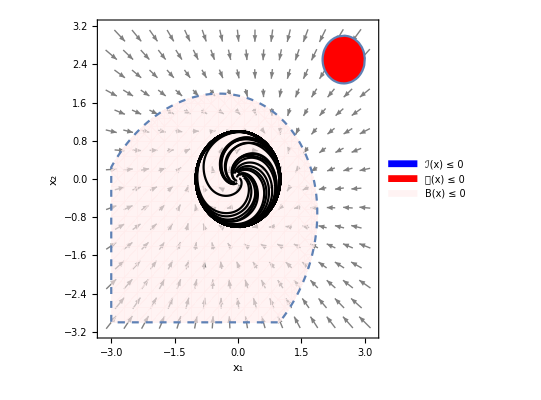

SDP CPU-time elapsed: 0.076057s

Total CPU-time elapsed: 1.18113s

```mathematica
main[varSetC5,flowVecC5,domainRangeC5,initialBoundaryC5,unsafeBoundaryC5,barrierDegreeC5,polyDegreesC5,paraRangeC5,LieOrderC5,ϵIC5,ϵUC5,ϵLC5,ϵC5,δC5,bilinearUnsafeConsC5,posteriorCheckC5,verboseC5];
```

### arch4

```mathematica
varSetC6={Subscript[x, 1],Subscript[x, 2]};
flowVecC6={-2 Subscript[x, 1] + Subscript[x, 1]^2 + Subscript[x, 2],Subscript[x, 1] - 2 Subscript[x, 2] + Subscript[x, 2]^2};
domainRangeC6={-0.5,1};
initialBoundaryC6=Subscript[x, 1]^2 + Subscript[x, 2]^2 - 0.1^2;
unsafeBoundaryC6=(Subscript[x, 1] - 0.75)^2 + (Subscript[x, 2] - 0.75)^2 - 0.25^2;
barrierDegreeC6=1;
polyDegreesC6={0,1,1};
paraRangeC6={-1,1};
LieOrderC6=1;
ϵIC6=0;
ϵUC6=ϵLC6=N[10^-3];
ϵC6=N[10^-1];
δC6=-N[10^-3];
bilinearUnsafeConsC6=False;
posteriorCheckC6=True;
verboseC6=False;
```

Template BC: 
a_00+a_10 x_1+a_01 x_2

Lie sequence: 
{a_00+a_10 x_1+a_01 x_2,(a_01-2 a_10) x_1+a_10 x_1^2+(-2 a_01+a_10) x_2+a_01 x_2^2}

SOS constraints:
{w_00,u_00+u_10 x_1+u_01 x_2,-a_00-0.01 w_00-a_10 x_1+w_00 x_1^2-a_01 x_2+w_00 x_2^2,-0.001+a_00+1.0625 u_00+u_10 x_1^3+(a_01-1.5 u_00+1.0625 u_01) x_2+(u_00-1.5 u_01) x_2^2+u_01 x_2^3+x_1^2 (u_00-1.5 u_10+u_01 x_2)+x_1 (a_10-1.5 u_00+1.0625 u_10+(-1.5 u_01-1.5 u_10) x_2+u_10 x_2^2),-0.001+a_00 v10_00+a_10 (-1+v10_10) x_1^2+(-a_10+a_01 (2+v10_00)+a_00 v10_01) x_2+a_01 (-1+v10_01) x_2^2+x_1 (-a_01+a_10 (2+v10_00)+a_00 v10_10+(a_10 v10_01+a_01 v10_10) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,u_01,u_10,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,u_01→z_7,u_10→z_8,v10_00→z_9,v10_01→z_10,v10_10→z_11}

Initial vector:
{a_00,a_01,a_10,λ,1,1,0,0,-1,0,0}

Initial feasible solution:
z^0={z_1→0.00596421,z_2→0.0160916,z_3→0.0160916,z_4→-0.0160916,z_5→1,z_6→1,z_7→0,z_8→0,z_9→-1,z_10→0,z_11→0}

Initial maximum:
λ^0=-0.0160916

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,u_01,u_10,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,u_01→z_7,u_10→z_8,v10_00→z_9,v10_01→z_10,v10_10→z_11,ζ→zz}

Feasible solution:
z^1={z_1→-0.000544775,z_2→0.000455535,z_3→0.000455535,z_4→-0.00052632,z_5→0.107013,z_6→0.00518969,z_7→-0.000410905,z_8→-0.000399836,z_9→-0.99797,z_10→0.00392678,z_11→0.00392678,zz→-0.000893941}

Maximum:
(λ+ζ)^1=-0.00142026

|z^1-z^0|=1.33712

Feasible solution:
z^2={z_1→-0.0005117,z_2→0.000489327,z_3→0.000489327,z_4→-0.000489349,z_5→0.0999859,z_6→0.0050168,z_7→-0.000381947,z_8→-0.000372007,z_9→-0.998373,z_10→0.00383193,z_11→0.00382879,zz→-0.000900411}

Maximum:
(λ+ζ)^2=-0.00138976

|z^2-z^1|=0.00704285

Close enough solutions: 0.00704285 ≤ ϵ = 0.1

Barrier certificate candidate:
-0.0005117+0.000489327 x_1+0.000489327 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

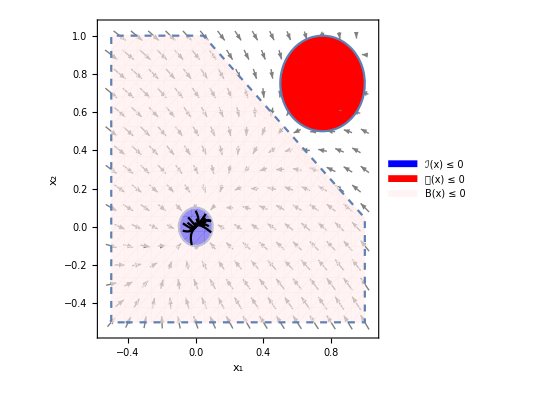

SDP CPU-time elapsed: 0.089763s

Total CPU-time elapsed: 0.758548s

```mathematica
main[varSetC6,flowVecC6,domainRangeC6,initialBoundaryC6,unsafeBoundaryC6,barrierDegreeC6,polyDegreesC6,paraRangeC6,LieOrderC6,ϵIC6,ϵUC6,ϵLC6,ϵC6,δC6,bilinearUnsafeConsC6,posteriorCheckC6,verboseC6];
```

### barr-cert1

```mathematica
varSet3={Subscript[x, 1],Subscript[x, 2]};
flowVec3={Subscript[x, 2],-Subscript[x, 1]+1/3 Subscript[x, 1]^3-Subscript[x, 2]};
domainRange3={-4,4};
initialBoundary3=(Subscript[x, 1]-1.5)^2+Subscript[x, 2]^2-0.25;
unsafeBoundary3=(Subscript[x, 1]+1)^2+(Subscript[x, 2]+1)^2-0.16;
barrierDegree3=2;
polyDegrees3={0,0,1};
paraRange3={-1,1};
LieOrder3=1;
ϵI3=ϵU3=ϵL3=N[10^-3];
ϵ3=N[10^-3];
δ3=-N[10^-3];
bilinearUnsafeCons3=True;
posteriorCheck3=True;
verbose3=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-a_11 x_1^2+1/3 a_11 x_1^4+(-a_01+a_10) x_2+(-2 a_02+a_11) x_2^2+x_1^3 (a_01/3+2/3 a_02 x_2)+x_1 (-a_01+(-2 a_02-a_11+2 a_20) x_2)}

SOS constraints:
{w_00,u_00,-0.001-a_00+2. w_00+(-a_20+w_00) x_1^2-a_01 x_2+(-a_02+w_00) x_2^2+x_1 (-a_10-3. w_00-a_11 x_2),1.839+a_00 u_00+(1+a_20 u_00) x_1^2+(2+a_01 u_00) x_2+(1+a_02 u_00) x_2^2+x_1 (2+a_10 u_00+a_11 u_00 x_2),-0.001+a_00 v10_00-1/3 a_11 x_1^4+(-a_10+a_01 (1+v10_00)+a_00 v10_01) x_2+(-a_11+a_02 (2+v10_00)+a_01 v10_01) x_2^2+a_02 v10_01 x_2^3+x_1^3 (-a_01/3+a_20 v10_10-2/3 a_02 x_2)+x_1^2 (a_11+a_20 v10_00+a_10 v10_10+(a_20 v10_01+a_11 v10_10) x_2)+x_1 (a_01+a_10 v10_00+a_00 v10_10+(2 a_02-2 a_20+a_11 (1+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_11 v10_01+a_02 v10_10) x_2^2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.0722189,z_2→-0.0526667,z_3→0.0237358,z_4→-0.101831,z_5→0.00962465,z_6→0.00933792,z_7→-0.0157104,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=-0.0157104

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Feasible solution:
z^1={z_1→-0.0214019,z_2→-0.0416281,z_3→0.0224746,z_4→-0.0538795,z_5→0.0132896,z_6→0.0184887,z_7→-0.0136064,z_8→0.41033,z_9→1.,z_10→-0.981263,z_11→0.0157775,z_12→-0.0438463,zz→-0.00017767}

Maximum:
(λ+ζ)^1=-0.013784

|z^1-z^0|=0.596104

Feasible solution:
z^2={z_1→-0.0187989,z_2→-0.042273,z_3→0.0217234,z_4→-0.0531155,z_5→0.0122643,z_6→0.0196371,z_7→-0.0128507,z_8→0.375679,z_9→1.,z_10→-0.950759,z_11→0.0226086,z_12→-0.0759101,zz→-0.000201968}

Maximum:
(λ+ζ)^2=-0.0130527

|z^2-z^1|=0.05672

Feasible solution:
z^3={z_1→-0.0216088,z_2→-0.0449698,z_3→0.0210798,z_4→-0.057175,z_5→0.0102943,z_6→0.0199389,z_7→-0.0123114,z_8→0.400801,z_9→1.,z_10→-0.919089,z_11→0.0288332,z_12→-0.110226,zz→-0.000191657}

Maximum:
(λ+ζ)^3=-0.0125031

|z^3-z^2|=0.0537287

Feasible solution:
z^4={z_1→-0.0260505,z_2→-0.0489361,z_3→0.0203,z_4→-0.0629813,z_5→0.00764846,z_6→0.0199555,z_7→-0.0116893,z_8→0.443821,z_9→1.,z_10→-0.887283,z_11→0.034641,z_12→-0.148742,zz→-0.000174582}

Maximum:
(λ+ζ)^4=-0.0118639

|z^4-z^3|=0.0667584

Feasible solution:
z^5={z_1→-0.032224,z_2→-0.0544534,z_3→0.0193293,z_4→-0.0706467,z_5→0.00418073,z_6→0.01971,z_7→-0.0109436,z_8→0.504978,z_9→1.,z_10→-0.855519,z_11→0.039369,z_12→-0.192561,zz→-0.000153653}

Maximum:
(λ+ζ)^5=-0.0110972

|z^5-z^4|=0.0826595

Feasible solution:
z^6={z_1→-0.0407329,z_2→-0.0622178,z_3→0.0180461,z_4→-0.080794,z_5→-0.00043963,z_6→0.0191068,z_7→-0.0100195,z_8→0.590271,z_9→1.,z_10→-0.823937,z_11→0.0420265,z_12→-0.242764,zz→-0.000130682}

Maximum:
(λ+ζ)^6=-0.0101502

|z^6-z^5|=0.105164

Feasible solution:
z^7={z_1→-0.052294,z_2→-0.0732281,z_3→0.0162678,z_4→-0.0941433,z_5→-0.00667889,z_6→0.0180188,z_7→-0.00884018,z_8→0.706591,z_9→1.,z_10→-0.792693,z_11→0.0413026,z_12→-0.300144,zz→-0.00011109}

Maximum:
(λ+ζ)^7=-0.00895127

|z^7-z^6|=0.135194

Feasible solution:
z^8={z_1→-0.0675017,z_2→-0.0887125,z_3→0.0137615,z_4→-0.11123,z_5→-0.0151023,z_6→0.0163148,z_7→-0.00731684,z_8→0.858972,z_9→1.,z_10→-0.761817,z_11→0.0357703,z_12→-0.364487,zz→-0.000106495}

Maximum:
(λ+ζ)^8=-0.00742334

|z^8-z^7|=0.170849

Feasible solution:
z^9={z_1→-0.0880103,z_2→-0.1107,z_3→0.0102692,z_4→-0.133562,z_5→-0.0267309,z_6→0.0135631,z_7→-0.00539027,z_8→0.999769,z_9→1.,z_10→-0.730831,z_11→0.024432,z_12→-0.433907,zz→-0.000133788}

Maximum:
(λ+ζ)^9=-0.00552406

|z^9-z^8|=0.165206

Feasible solution:
z^10={z_1→-0.120047,z_2→-0.144148,z_3→0.00551476,z_4→-0.166966,z_5→-0.0442839,z_6→0.00834194,z_7→-0.00306052,z_8→0.999801,z_9→1.,z_10→-0.69833,z_11→0.00767397,z_12→-0.505303,zz→-0.000182346}

Maximum:
(λ+ζ)^10=-0.00324287

|z^10-z^9|=0.100293

Feasible solution:
z^11={z_1→-0.164565,z_2→-0.190944,z_3→-0.00012426,z_4→-0.211598,z_5→-0.0691815,z_6→0.000393027,z_7→-0.000393335,z_8→0.9998,z_9→1.,z_10→-0.663131,z_11→-0.000671038,z_12→-0.573928,zz→-0.000244833}

Maximum:
(λ+ζ)^11=-0.000638168

|z^11-z^10|=0.113595

Feasible solution:
z^12={z_1→-0.145811,z_2→-0.182462,z_3→-2.39609×10^-6,z_4→-0.196314,z_5→-0.06694,z_6→0.00319324,z_7→-4.36844×10^-7,z_8→0.999794,z_9→0.999999,z_10→-0.702853,z_11→0.0000484782,z_12→-0.572964,zz→-0.000227242}

Maximum:
(λ+ζ)^12=-0.000227678

|z^12-z^11|=0.04743

Barrier certificate candidate:
-0.145811-0.196314 x_1+0.00319324 x_1^2-0.182462 x_2-0.06694 x_1 x_2-2.39609×10^-6 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

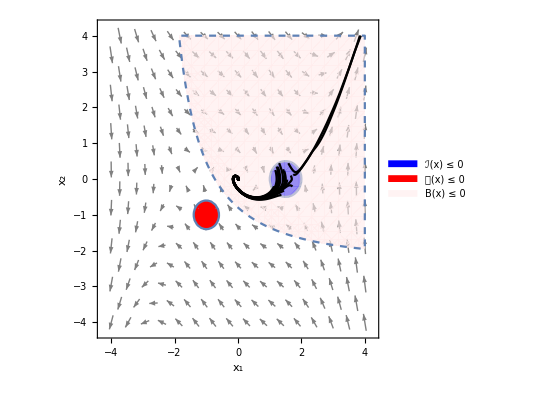

SDP CPU-time elapsed: 1.01272s

Total CPU-time elapsed: 2.0193s

```mathematica
main[varSet3,flowVec3,domainRange3,initialBoundary3,unsafeBoundary3,barrierDegree3,polyDegrees3,paraRange3,LieOrder3,ϵI3,ϵU3,ϵL3,ϵ3,δ3,bilinearUnsafeCons3,posteriorCheck3,verbose3];
```

### barr-cert2

```mathematica
varSet6={Subscript[x, 1],Subscript[x, 2]};
flowVec6={-Subscript[x, 1]+Subscript[x, 1] Subscript[x, 2],-Subscript[x, 2]};
domainRange6={0,1.5};
initialBoundary6=(Subscript[x, 1]-1.125)^2+(Subscript[x, 2]-0.625)^2-0.125^2;
unsafeBoundary6=(Subscript[x, 1]-0.875)^2+(Subscript[x, 2]-0.125)^2-0.075^2;
barrierDegree6=2;
polyDegrees6={2,2,2};
paraRange6={-10,10};
LieOrder6=1;
ϵI6=ϵU6=ϵL6=N[10^-3];
ϵ6=N[10^-6];
δ6=-N[10^-3];
bilinearUnsafeCons6=False;
posteriorCheck6=True;
verbose6=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-a_01 x_2-2 a_02 x_2^2+x_1^2 (-2 a_20+2 a_20 x_2)+x_1 (-a_10+(a_10-2 a_11) x_2+a_11 x_2^2)}

SOS constraints:
{w_00+w_20 x_1^2+w_01 x_2+w_02 x_2^2+x_1 (w_10+w_11 x_2),u_00+u_20 x_1^2+u_01 x_2+u_02 x_2^2+x_1 (u_10+u_11 x_2),-0.001-a_00+1.64063 w_00+w_20 x_1^4+(-a_01-1.25 w_00+1.64063 w_01) x_2+(-a_02+w_00-1.25 w_01+1.64063 w_02) x_2^2+(w_01-1.25 w_02) x_2^3+w_02 x_2^4+x_1^3 (w_10-2.25 w_20+w_11 x_2)+x_1^2 (-a_20+w_00-2.25 w_10+1.64063 w_20+(w_01-2.25 w_11-1.25 w_20) x_2+(w_02+w_20) x_2^2)+x_1 (-a_10-2.25 w_00+1.64063 w_10+(-a_11-2.25 w_01-1.25 w_10+1.64063 w_11) x_2+(-2.25 w_02+w_10-1.25 w_11) x_2^2+w_11 x_2^3),-0.001+a_00+0.775625 u_00+u_20 x_1^4+(a_01-0.25 u_00+0.775625 u_01) x_2+(a_02+u_00-0.25 u_01+0.775625 u_02) x_2^2+(u_01-0.25 u_02) x_2^3+u_02 x_2^4+x_1^3 (u_10-1.75 u_20+u_11 x_2)+x_1^2 (a_20+u_00-1.75 u_10+0.775625 u_20+(u_01-1.75 u_11-0.25 u_20) x_2+(u_02+u_20) x_2^2)+x_1 (a_10-1.75 u_00+0.775625 u_10+(a_11-1.75 u_01-0.25 u_10+0.775625 u_11) x_2+(-1.75 u_02+u_10-0.25 u_11) x_2^2+u_11 x_2^3),-0.001+a_00 v10_00+a_20 v10_20 x_1^4+(a_01 (1+v10_00)+a_00 v10_01) x_2+(a_02 (2+v10_00)+a_01 v10_01+a_00 v10_02) x_2^2+(a_02 v10_01+a_01 v10_02) x_2^3+a_02 v10_02 x_2^4+x_1^3 (a_20 v10_10+a_10 v10_20+(a_20 v10_11+a_11 v10_20) x_2)+x_1^2 (a_20 (2+v10_00)+a_10 v10_10+a_00 v10_20+(a_20 (-2+v10_01)+a_11 v10_10+a_10 v10_11+a_01 v10_20) x_2+(a_20 v10_02+a_11 v10_11+a_02 v10_20) x_2^2)+x_1 (a_10 (1+v10_00)+a_00 v10_10+(a_11 (2+v10_00)+a_10 (-1+v10_01)+a_01 v10_10+a_00 v10_11) x_2+(a_11 (-1+v10_01)+a_10 v10_02+a_02 v10_10+a_01 v10_11) x_2^2+(a_11 v10_02+a_02 v10_11) x_2^3)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,w_01,w_02,w_10,w_11,w_20,u_00,u_01,u_02,u_10,u_11,u_20,v10_00,v10_01,v10_02,v10_10,v10_11,v10_20}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,w_01→z_9,w_02→z_10,w_10→z_11,w_11→z_12,w_20→z_13,u_00→z_14,u_01→z_15,u_02→z_16,u_10→z_17,u_11→z_18,u_20→z_19,v10_00→z_20,v10_01→z_21,v10_02→z_22,v10_10→z_23,v10_11→z_24,v10_20→z_25}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0,0,0}

Initial feasible solution:
z^0={z_1→-0.000824533,z_2→-0.217056,z_3→0.175424,z_4→0.0407829,z_5→0.00177403,z_6→0.00321743,z_7→-0.000175443,z_8→1,z_9→0,z_10→0,z_11→0,z_12→0,z_13→0,z_14→1,z_15→0,z_16→0,z_17→0,z_18→0,z_19→0,z_20→-1,z_21→0,z_22→0,z_23→0,z_24→0,z_25→0}

Initial maximum:
λ^0=-0.000175443

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,w_01,w_02,w_10,w_11,w_20,u_00,u_01,u_02,u_10,u_11,u_20,v10_00,v10_01,v10_02,v10_10,v10_11,v10_20,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,w_01→z_9,w_02→z_10,w_10→z_11,w_11→z_12,w_20→z_13,u_00→z_14,u_01→z_15,u_02→z_16,u_10→z_17,u_11→z_18,u_20→z_19,v10_00→z_20,v10_01→z_21,v10_02→z_22,v10_10→z_23,v10_11→z_24,v10_20→z_25,ζ→zz}

Feasible solution:
z^1={z_1→-0.00095613,z_2→-0.217495,z_3→0.15986,z_4→0.0410135,z_5→0.015228,z_6→0.00119727,z_7→-0.0000618461,z_8→0.937531,z_9→-0.0000984652,z_10→-0.0000251613,z_11→-0.0000983519,z_12→0.0000172865,z_13→-0.0000301512,z_14→0.999316,z_15→-0.000037679,z_16→0.000218905,z_17→-0.0000963189,z_18→-0.0000206786,z_19→0.0000448846,z_20→-0.998785,z_21→0.000104524,z_22→0.0118668,z_23→0.00484958,z_24→0.00132589,z_25→0.00988786,zz→-2.29793×10^-6}

Maximum:
(λ+ζ)^1=-0.000064144

|z^1-z^0|=0.0677927

Feasible solution:
z^2={z_1→-0.000990694,z_2→-0.217758,z_3→0.155775,z_4→0.0412068,z_5→0.0163559,z_6→0.00118508,z_7→-0.0000182994,z_8→0.97408,z_9→-0.0000304237,z_10→-5.24393×10^-6,z_11→-0.0000284652,z_12→6.24055×10^-6,z_13→-0.0000100473,z_14→1.00001,z_15→0.0000439972,z_16→0.000299657,z_17→-0.0000382968,z_18→-0.000110458,z_19→0.000248691,z_20→-0.999736,z_21→0.00024711,z_22→0.0189213,z_23→0.00763579,z_24→0.0027994,z_25→0.00879672,zz→-8.88646×10^-7}

Maximum:
(λ+ζ)^2=-0.000019188

|z^2-z^1|=0.0376334

Feasible solution:
z^3={z_1→-0.000998284,z_2→-0.218053,z_3→0.155105,z_4→0.0412524,z_5→0.0169042,z_6→0.0011425,z_7→-0.0000147402,z_8→0.97696,z_9→-0.0000243933,z_10→-3.76838×10^-6,z_11→-0.0000230081,z_12→4.93334×10^-6,z_13→-8.02576×10^-6,z_14→1.00003,z_15→0.0000465169,z_16→0.000291385,z_17→-0.0000327926,z_18→-0.000110432,z_19→0.000248711,z_20→-0.999592,z_21→0.000372991,z_22→0.0253406,z_23→0.0101687,z_24→0.00403948,z_25→0.0080542,zz→-1.00271×10^-6}

Maximum:
(λ+ζ)^3=-0.0000157429

|z^3-z^2|=0.00767348

Feasible solution:
z^4={z_1→-0.00100404,z_2→-0.218352,z_3→0.154946,z_4→0.0413206,z_5→0.0171279,z_6→0.00111627,z_7→-0.0000121653,z_8→0.979353,z_9→-0.0000194862,z_10→-1.84353×10^-6,z_11→-0.000019377,z_12→3.50982×10^-6,z_13→-6.1457×10^-6,z_14→1.00007,z_15→0.000050787,z_16→0.000290086,z_17→-0.0000292783,z_18→-0.000114127,z_19→0.000257042,z_20→-0.999472,z_21→0.000490327,z_22→0.0306548,z_23→0.012434,z_24→0.00511191,z_25→0.00745198,zz→-1.13226×10^-6}

Maximum:
(λ+ζ)^4=-0.0000132976

|z^4-z^3|=0.00638839

Feasible solution:
z^5={z_1→-0.00100897,z_2→-0.218643,z_3→0.155052,z_4→0.0413993,z_5→0.0171818,z_6→0.00109787,z_7→-0.000010205,z_8→0.981383,z_9→-0.000014974,z_10→9.26749×10^-7,z_11→-0.0000170691,z_12→1.74617×10^-6,z_13→-4.12196×10^-6,z_14→1.0001,z_15→0.0000557927,z_16→0.00029562,z_17→-0.0000269214,z_18→-0.000120151,z_19→0.000270603,z_20→-0.999356,z_21→0.000600691,z_22→0.0348586,z_23→0.0144646,z_24→0.00604993,z_25→0.00695292,zz→-1.25837×10^-6}

Maximum:
(λ+ζ)^5=-0.0000114634

|z^5-z^4|=0.0052132

Feasible solution:
z^6={z_1→-0.00101328,z_2→-0.218923,z_3→0.155308,z_4→0.0414812,z_5→0.0171388,z_6→0.00108458,z_7→-8.68221×10^-6,z_8→0.983101,z_9→-0.0000111586,z_10→3.58856×10^-6,z_11→-0.0000154585,z_12→1.03748×10^-7,z_13→-2.31141×10^-6,z_14→1.00013,z_15→0.0000600219,z_16→0.000300369,z_17→-0.0000251581,z_18→-0.000125343,z_19→0.000282264,z_20→-0.999245,z_21→0.000704345,z_22→0.0380498,z_23→0.0162935,z_24→0.00687155,z_25→0.00653211,zz→-1.36967×10^-6}

Maximum:
(λ+ζ)^6=-0.0000100519

|z^6-z^5|=0.00418439

Barrier certificate candidate:
-0.00101328+0.0414812 x_1+0.00108458 x_1^2-0.218923 x_2+0.0171388 x_1 x_2+0.155308 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

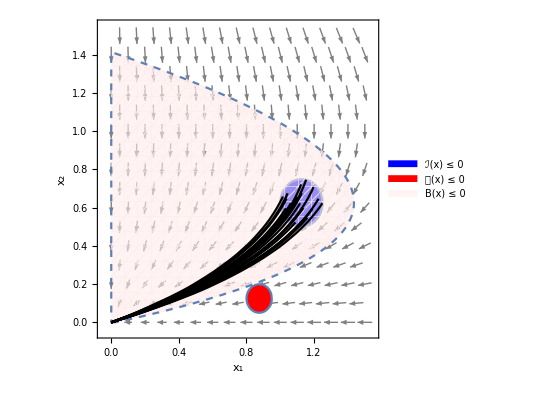

SDP CPU-time elapsed: 1.575s

Total CPU-time elapsed: 2.97386s

```mathematica
main[varSet6,flowVec6,domainRange6,initialBoundary6,unsafeBoundary6,barrierDegree6,polyDegrees6,paraRange6,LieOrder6,ϵI6,ϵU6,ϵL6,ϵ6,δ6,bilinearUnsafeCons6,posteriorCheck6,verbose6];
```

### barr-cert3

```mathematica
varSetC7={Subscript[x, 1],Subscript[x, 2]};
flowVecC7={-Subscript[x, 1] + Subscript[x, 1] Subscript[x, 2],-Subscript[x, 2]};
domainRangeC7={-2,2};
initialBoundaryC7=(Subscript[x, 1] + 1)^2 + (Subscript[x, 2] + 1)^2 - 0.5^2;
unsafeBoundaryC7=Subscript[x, 1]^2 + (Subscript[x, 2] - 1)^2 - 0.5^2;
barrierDegreeC7=1;
polyDegreesC7={0,0,1};
paraRangeC7={-10,10};
LieOrderC7=1;
ϵIC7=ϵUC7=ϵLC7=N[10^-3];
ϵC7=N[10^-3];
δC7=-N[10^-3];
bilinearUnsafeConsC7=False;
posteriorCheckC7=True;
verboseC7=False;
```

Template BC: 
a_00+a_10 x_1+a_01 x_2

Lie sequence: 
{a_00+a_10 x_1+a_01 x_2,-a_01 x_2+x_1 (-a_10+a_10 x_2)}

SOS constraints:
{w_00,u_00,-0.001-a_00+1.75 w_00+(-a_10+2 w_00) x_1+w_00 x_1^2+(-a_01+2 w_00) x_2+w_00 x_2^2,-0.001+a_00+0.75 u_00+a_10 x_1+u_00 x_1^2+(a_01-2 u_00) x_2+u_00 x_2^2,-0.001+a_00 v10_00+a_10 v10_10 x_1^2+(a_01 (1+v10_00)+a_00 v10_01) x_2+a_01 v10_01 x_2^2+x_1 (a_10 (1+v10_00)+a_00 v10_10+(a_10 (-1+v10_01)+a_01 v10_10) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9}

Initial vector:
{a_00,a_01,a_10,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.378117,z_2→1.9881,z_3→4.11417×10^-13,z_4→5.71666×10^-9,z_5→1,z_6→1,z_7→-1,z_8→0,z_9→0}

Initial maximum:
λ^0=5.71666×10^-9

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9,ζ→zz}

Barrier certificate candidate:
-0.378117+4.11417×10^-13 x_1+1.9881 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

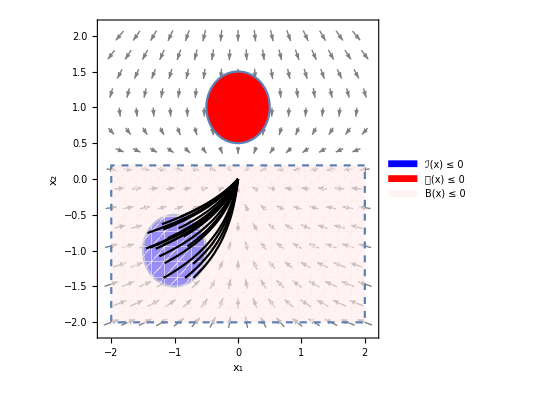

SDP CPU-time elapsed: 0.012157s

Total CPU-time elapsed: 0.499227s

```mathematica
main[varSetC7,flowVecC7,domainRangeC7,initialBoundaryC7,unsafeBoundaryC7,barrierDegreeC7,polyDegreesC7,paraRangeC7,LieOrderC7,ϵIC7,ϵUC7,ϵLC7,ϵC7,δC7,bilinearUnsafeConsC7,posteriorCheckC7,verboseC7];
```

### barr-cert4

```mathematica
varSetC8={Subscript[x, 1],Subscript[x, 2]};
flowVecC8={-Subscript[x, 1] + 2 Subscript[x, 1]^2 Subscript[x, 2],-Subscript[x, 2]};
domainRangeC8={-1,3};
initialBoundaryC8=(3 Subscript[x, 1])^2 + (2 Subscript[x, 2] - 2.25)^2 - 0.75^2;
unsafeBoundaryC8=(Subscript[x, 1] - 2)^2 + (Subscript[x, 2] - 2)^2 - 0.5^2;
barrierDegreeC8=2;
polyDegreesC8={0,0,1};
paraRangeC8={-1,1};
LieOrderC8=1;
ϵIC8=N[10^-3];
ϵUC8=ϵLC8=N[10^-3];
ϵC8=N[10^-2];
δC8=-N[10^-3];
bilinearUnsafeConsC8=False;
posteriorCheckC8=True;
verboseC8=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-a_01 x_2+4 a_20 x_1^3 x_2-2 a_02 x_2^2+x_1 (-a_10-2 a_11 x_2)+x_1^2 (-2 a_20+2 a_10 x_2+2 a_11 x_2^2)}

SOS constraints:
{w_00,u_00,-0.001-a_00+4.5 w_00+(-a_20+9 w_00) x_1^2+(-a_01-9. w_00) x_2+(-a_02+4 w_00) x_2^2+x_1 (-a_10-a_11 x_2),-0.001+a_00+7.75 u_00+(a_20+u_00) x_1^2+(a_01-4 u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10-4 u_00+a_11 x_2),-0.001+a_00 v10_00+(a_01 (1+v10_00)+a_00 v10_01) x_2+(a_02 (2+v10_00)+a_01 v10_01) x_2^2+a_02 v10_01 x_2^3+x_1^3 (a_20 v10_10-4 a_20 x_2)+x_1^2 (a_20 (2+v10_00)+a_10 v10_10+(-2 a_10+a_20 v10_01+a_11 v10_10) x_2-2 a_11 x_2^2)+x_1 (a_10 (1+v10_00)+a_00 v10_10+(a_11 (2+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_11 v10_01+a_02 v10_10) x_2^2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.726727,z_2→-1.,z_3→0.946993,z_4→0.0729669,z_5→0.00279561,z_6→1.88707×10^-10,z_7→-0.00559122,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=-0.00559122

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Feasible solution:
z^1={z_1→-0.643411,z_2→-0.911503,z_3→0.895054,z_4→0.0334194,z_5→0.000213218,z_6→0.000195754,z_7→-0.00134436,z_8→0.598423,z_9→1.,z_10→-0.997434,z_11→-0.00117978,z_12→0.00882843,zz→-0.0000902048}

Maximum:
(λ+ζ)^1=-0.00143456

|z^1-z^0|=0.424746

Feasible solution:
z^2={z_1→-0.575445,z_2→-0.852963,z_3→0.824934,z_4→0.0239257,z_5→-0.000142914,z_6→0.000125347,z_7→-0.000734638,z_8→0.549345,z_9→1.,z_10→-0.991443,z_11→-0.00132925,z_12→0.00680699,zz→-0.000132527}

Maximum:
(λ+ζ)^2=-0.000867165

|z^2-z^1|=0.12451

Feasible solution:
z^3={z_1→-0.525327,z_2→-0.811718,z_3→0.774671,z_4→0.0175339,z_5→-0.0000512963,z_6→0.0000557842,z_7→-0.000410598,z_8→0.514709,z_9→1.,z_10→-0.986768,z_11→-0.000993946,z_12→0.00410248,zz→-0.000172257}

Maximum:
(λ+ζ)^3=-0.000582855

|z^3-z^2|=0.0894933

Feasible solution:
z^4={z_1→-0.486473,z_2→-0.783729,z_3→0.738468,z_4→0.0133134,z_5→-7.86498×10^-6,z_6→0.0000218957,z_7→-0.000242258,z_8→0.48955,z_9→1.,z_10→-0.983402,z_11→-0.000686488,z_12→0.00210728,zz→-0.000206207}

Maximum:
(λ+ζ)^4=-0.000448465

|z^4-z^3|=0.0653451

Feasible solution:
z^5={z_1→-0.454815,z_2→-0.765858,z_3→0.712315,z_4→0.0104529,z_5→0.0000141581,z_6→7.47712×10^-6,z_7→-0.000152133,z_8→0.470989,z_9→1.,z_10→-0.980984,z_11→-0.000475384,z_12→0.000934631,zz→-0.000233996}

Maximum:
(λ+ζ)^5=-0.00038613

|z^5-z^4|=0.0486365

Feasible solution:
z^6={z_1→-0.427705,z_2→-0.756459,z_3→0.693883,z_4→0.00849518,z_5→0.0000260715,z_6→1.92779×10^-6,z_7→-0.000102177,z_8→0.45725,z_9→1.,z_10→-0.979074,z_11→-0.000339391,z_12→0.000335812,zz→-0.000256001}

Maximum:
(λ+ζ)^6=-0.000358177

|z^6-z^5|=0.0368733

Feasible solution:
z^7={z_1→-0.403515,z_2→-0.755696,z_3→0.682538,z_4→0.00720602,z_5→0.0000320266,z_6→1.57213×10^-7,z_7→-0.0000744145,z_8→0.447555,z_9→1.,z_10→-0.977247,z_11→-0.000255155,z_12→0.000069757,zz→-0.000272082}

Maximum:
(λ+ζ)^7=-0.000346496

|z^7-z^6|=0.0285223

Feasible solution:
z^8={z_1→-0.382943,z_2→-0.764723,z_3→0.679363,z_4→0.00654137,z_5→0.000029003,z_6→5.982×10^-8,z_7→-0.0000614676,z_8→0.442232,z_9→1.,z_10→-0.975055,z_11→-0.000220531,z_12→0.0000474507,zz→-0.000280673}

Maximum:
(λ+ζ)^8=-0.000342141

|z^8-z^7|=0.0234173

Feasible solution:
z^9={z_1→-0.365471,z_2→-0.778697,z_3→0.680882,z_4→0.00622014,z_5→0.0000267798,z_6→1.06486×10^-7,z_7→-0.00005532,z_8→0.439705,z_9→1.,z_10→-0.972406,z_11→-0.000199078,z_12→0.0000523702,zz→-0.00028474}

Maximum:
(λ+ζ)^9=-0.00034006

|z^9-z^8|=0.0227234

Feasible solution:
z^10={z_1→-0.351557,z_2→-0.794966,z_3→0.685533,z_4→0.00613826,z_5→0.0000237965,z_6→1.73297×10^-7,z_7→-0.000053336,z_8→0.439097,z_9→1.,z_10→-0.968882,z_11→-0.00019326,z_12→0.0000770083,zz→-0.000285619}

Maximum:
(λ+ζ)^10=-0.000338955

|z^10-z^9|=0.0221972

Feasible solution:
z^11={z_1→-0.34038,z_2→-0.810516,z_3→0.69093,z_4→0.00615083,z_5→0.0000239776,z_6→1.66758×10^-7,z_7→-0.0000528862,z_8→0.43932,z_9→1.,z_10→-0.963739,z_11→-0.000191609,z_12→0.0000862436,zz→-0.000285458}

Maximum:
(λ+ζ)^11=-0.000338344

|z^11-z^10|=0.0205514

Feasible solution:
z^12={z_1→-0.33354,z_2→-0.821469,z_3→0.695193,z_4→0.00620438,z_5→0.0000257359,z_6→1.58463×10^-7,z_7→-0.0000531826,z_8→0.439887,z_9→1.,z_10→-0.957566,z_11→-0.000190178,z_12→0.0000990299,zz→-0.000284948}

Maximum:
(λ+ζ)^12=-0.000338131

|z^12-z^11|=0.0149449

Feasible solution:
z^13={z_1→-0.332215,z_2→-0.824153,z_3→0.696396,z_4→0.00623194,z_5→0.0000267002,z_6→1.98412×10^-7,z_7→-0.0000535036,z_8→0.440148,z_9→1.,z_10→-0.956534,z_11→-0.000187202,z_12→0.000132343,zz→-0.000284588}

Maximum:
(λ+ζ)^13=-0.000338092

|z^13-z^12|=0.00339698

Close enough solutions: 0.00339698 ≤ ϵ = 0.01

Barrier certificate candidate:
-0.332215+0.00623194 x_1+1.98412×10^-7 x_1^2-0.824153 x_2+0.0000267002 x_1 x_2+0.696396 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

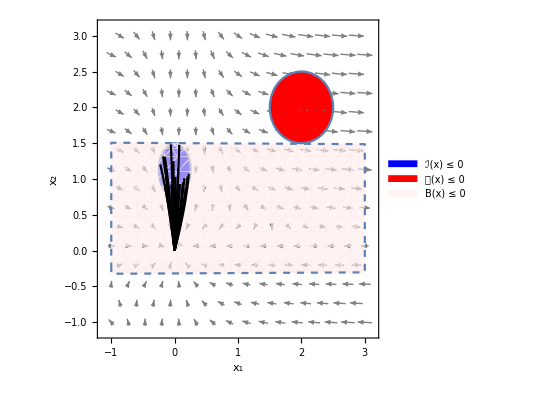

SDP CPU-time elapsed: 0.954721s

Total CPU-time elapsed: 1.61804s

```mathematica
main[varSetC8,flowVecC8,domainRangeC8,initialBoundaryC8,unsafeBoundaryC8,barrierDegreeC8,polyDegreesC8,paraRangeC8,LieOrderC8,ϵIC8,ϵUC8,ϵLC8,ϵC8,δC8,bilinearUnsafeConsC8,posteriorCheckC8,verboseC8];
```

### fitzhugh-nagumo

```mathematica
varSetC12={Subscript[x, 1],Subscript[x, 2]};
flowVecC12={-1/3 Subscript[x, 1]^3 + Subscript[x, 1] - Subscript[x, 2] + 0.875, 0.08(Subscript[x, 1] - 0.8 Subscript[x, 2] + 0.7)};
domainRangeC12={-5,5};
initialBoundaryC12=(Subscript[x, 1] + 0.75)^2 + (Subscript[x, 2] - 1.25)^2 - 0.25^2;
unsafeBoundaryC12=(Subscript[x, 1]+2.25)^2+(Subscript[x, 2]+1.75)^2-0.25^2;
barrierDegreeC12=2;
polyDegreesC12={0,0,1};
paraRangeC12={-10,10};
LieOrderC12=1;
ϵIC12=ϵUC12=ϵLC12=N[10^-3];
ϵC12=N[10^-1];
δC12=-N[10^-3];
bilinearUnsafeConsC12=False;
posteriorCheckC12=True;
verboseC12=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,0.056 a_01+0.875 a_10+(0.08 a_11+2 a_20) x_1^2-2/3 a_20 x_1^4+(-0.064 a_01+0.112 a_02-a_10+0.875 a_11) x_2+(-0.128 a_02-a_11) x_2^2+x_1^3 (-a_10/3-1/3 a_11 x_2)+x_1 (0.08 a_01+a_10+0.056 a_11+1.75 a_20+(0.16 a_02+0.936 a_11-2 a_20) x_2)}

SOS constraints:
{w_00,u_00,-0.001-a_00+2.0625 w_00+(-a_20+w_00) x_1^2+(-a_01-2.5 w_00) x_2+(-a_02+w_00) x_2^2+x_1 (-a_10+1.5 w_00-a_11 x_2),-0.001+a_00+8.0625 u_00+(a_20+u_00) x_1^2+(a_01+3.5 u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10+4.5 u_00+a_11 x_2),-0.001-0.056 a_01-0.875 a_10+a_00 v10_00+2/3 a_20 x_1^4+(-0.112 a_02+a_10-0.875 a_11+a_01 (0.064+v10_00)+a_00 v10_01) x_2+(a_11+a_02 (0.128+v10_00)+a_01 v10_01) x_2^2+a_02 v10_01 x_2^3+x_1^3 (a_10/3+a_20 v10_10+1/3 a_11 x_2)+x_1^2 (-0.08 a_11+a_20 (-2+v10_00)+a_10 v10_10+(a_20 v10_01+a_11 v10_10) x_2)+x_1 (-0.08 a_01-0.056 a_11-1.75 a_20+a_10 (-1+v10_00)+a_00 v10_10+(-0.16 a_02+2 a_20+a_11 (-0.936+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_11 v10_01+a_02 v10_10) x_2^2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.0163714,z_2→-0.0261145,z_3→-0.00242609,z_4→-0.0000445665,z_5→0.00129163,z_6→0.0011054,z_7→-0.00342024,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=-0.00342024

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Feasible solution:
z^1={z_1→-0.0210492,z_2→-0.0246866,z_3→-0.00724648,z_4→0.0000333312,z_5→0.000124111,z_6→7.84783×10^-6,z_7→-0.000115189,z_8→0.996196,z_9→0.00713182,z_10→-0.998723,z_11→-0.0069853,z_12→-0.00908535,zz→-0.000492998}

Maximum:
(λ+ζ)^1=-0.000608187

|z^1-z^0|=0.992973

Feasible solution:
z^2={z_1→-0.0254125,z_2→-0.0299596,z_3→-0.00877736,z_4→0.0000827116,z_5→0.000198837,z_6→-2.99189×10^-6,z_7→-0.0000918111,z_8→1.,z_9→0.00868668,z_10→-1.00009,z_11→-0.0112117,z_12→-0.0150178,zz→-0.000491602}

Maximum:
(λ+ζ)^2=-0.000583413

|z^2-z^1|=0.0110004

Close enough solutions: 0.0110004 ≤ ϵ = 0.1

Barrier certificate candidate:
-0.0254125+0.0000827116 x_1-2.99189×10^-6 x_1^2-0.0299596 x_2+0.000198837 x_1 x_2-0.00877736 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

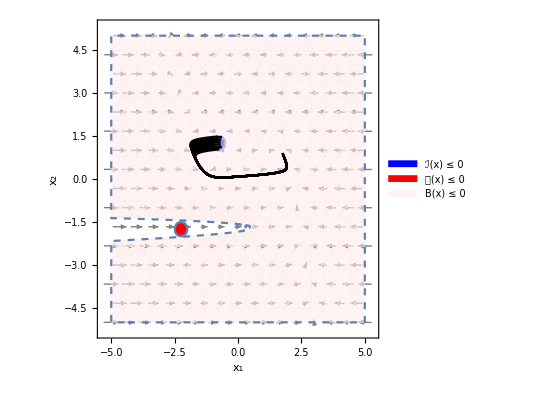

SDP CPU-time elapsed: 0.156141s

Total CPU-time elapsed: 0.88189s

```mathematica
main[varSetC12,flowVecC12,domainRangeC12,initialBoundaryC12,unsafeBoundaryC12,barrierDegreeC12,polyDegreesC12,paraRangeC12,LieOrderC12,ϵIC12,ϵUC12,ϵLC12,ϵC12,δC12,bilinearUnsafeConsC12,posteriorCheckC12,verboseC12];
```

### stabilization

```mathematica
varSetC14={Subscript[x, 1],Subscript[x, 2], Subscript[x, 3]};
flowVecC14={-Subscript[x, 1] + Subscript[x, 2] - Subscript[x, 3], -Subscript[x, 1] (Subscript[x, 3] + 1) - Subscript[x, 2], -Subscript[x, 1] + 1.76524 Subscript[x, 1] - 4.7037 Subscript[x, 3]};
domainRangeC14={-2,2};
initialBoundaryC14= Subscript[x, 1]^2 + Subscript[x, 2]^2 + Subscript[x, 3]^2 - 1;
unsafeBoundaryC14= 3 - Subscript[x, 1]^2 - Subscript[x, 2]^2;
barrierDegreeC14=2;
polyDegreesC14={0,0,1};
paraRangeC14={-10,10};
LieOrderC14=1;
ϵIC14=ϵUC14=ϵLC14=N[10^-3];
ϵC14=N[10^-1];
δC14=-N[10^-3];
bilinearUnsafeConsC14=False;
posteriorCheckC14=True;
verboseC14=False;
```

```mathematica
main[varSetC14,flowVecC14,domainRangeC14,initialBoundaryC14,unsafeBoundaryC14,barrierDegreeC14,polyDegreesC14,paraRangeC14,LieOrderC14,ϵIC14,ϵUC14,ϵLC14,ϵC14,δC14,bilinearUnsafeConsC14,posteriorCheckC14,verboseC14];
```

Template BC: 
a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2

Lie sequence: 
{a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2,(-2 a_020+a_110) x_2^2+(-4.7037 a_001-a_100) x_3+(-9.4074 a_002-a_101) x_3^2+x_2 (-a_010+a_100+(-5.7037 a_011+a_101-a_110) x_3)+x_1^2 (0.76524 a_101-a_110-2 a_200-a_110 x_3)+x_1 (0.76524 a_001-a_010-a_100+(1.53048 a_002-a_010-a_011-5.7037 a_101-2 a_200) x_3-a_011 x_3^2+x_2 (0.76524 a_011-2 (a_020+a_110-a_200)-2 a_020 x_3))}

SOS constraints:
{w_000,u_000,-0.001-a_000-w_000+(-a_200+w_000) x_1^2+(-a_020+w_000) x_2^2-a_001 x_3+(-a_002+w_000) x_3^2+x_2 (-a_010-a_011 x_3)+x_1 (-a_100-a_110 x_2-a_101 x_3),-0.001+a_000+3 u_000+(a_200-u_000) x_1^2+(a_020-u_000) x_2^2+a_001 x_3+a_002 x_3^2+x_2 (a_010+a_011 x_3)+x_1 (a_100+a_110 x_2+a_101 x_3),-0.001+a_000 v10_000+a_200 v10_100 x_1^3+a_020 v10_010 x_2^3+(a_100+a_001 (4.7037+v10_000)+a_000 v10_001) x_3+(a_101+a_002 (9.4074+v10_000)+a_001 v10_001) x_3^2+a_002 v10_001 x_3^3+x_2^2 (-a_110+a_020 (2+v10_000)+a_010 v10_010+(a_020 v10_001+a_011 v10_010) x_3)+x_1^2 (-0.76524 a_101+a_110+2 a_200+a_200 v10_000+a_100 v10_100+(a_200 v10_010+a_110 v10_100) x_2+(a_110+a_200 v10_001+a_101 v10_100) x_3)+x_2 (-a_100+a_010 (1+v10_000)+a_000 v10_010+(-a_101+a_110+a_011 (5.7037+v10_000)+a_010 v10_001+a_001 v10_010) x_3+(a_011 v10_001+a_002 v10_010) x_3^2)+x_1 (-0.76524 a_001+a_010+a_100+a_100 v10_000+a_000 v10_100+(a_110 v10_010+a_020 v10_100) x_2^2+(-1.53048 a_002+a_010+a_011+5.7037 a_101+2 a_200+a_101 v10_000+a_100 v10_001+a_001 v10_100) x_3+(a_011+a_101 v10_001+a_002 v10_100) x_3^2+x_2 (-0.76524 a_011+2 (a_020+a_110-a_200)+a_110 v10_000+a_100 v10_010+a_010 v10_100+(2 a_020+a_110 v10_001+a_101 v10_010+a_011 v10_100) x_3))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17}

Initial vector:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-0.912243,z_2→0.0000651202,z_3→1.08909,z_4→-0.0237353,z_5→-0.00131387,z_6→0.910474,z_7→-0.00286964,z_8→0.0189931,z_9→5.0655×10^-6,z_10→0.910486,z_11→-0.0895914,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0}

Initial maximum:
λ^0=-0.0895914

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17,ζ→zz}

Feasible solution:
z^1={z_1→-1.70681,z_2→7.6901×10^-6,z_3→1.76261,z_4→-6.23079×10^-8,z_5→0.00120133,z_6→0.531305,z_7→-0.000537006,z_8→0.0200929,z_9→0.000134585,z_10→1.0612,z_11→-0.0284727,z_12→1.73428,z_13→0.559778,z_14→-0.115182,z_15→-0.0000659004,z_16→-0.00202475,z_17→-0.00564969,zz→-0.00138583}

Maximum:
(λ+ζ)^1=-0.0298586

|z^1-z^0|=1.66483

Feasible solution:
z^2={z_1→-1.2519,z_2→1.15106×10^-6,z_3→1.27977,z_4→-3.02677×10^-9,z_5→0.000927971,z_6→0.398201,z_7→-0.0000409857,z_8→0.0197407,z_9→0.0000960572,z_10→0.928587,z_11→-0.0145736,z_12→1.26547,z_13→0.412774,z_14→-0.0453448,z_15→-0.0000412643,z_16→-0.000734396,z_17→-0.00180987,zz→-0.000873679}

Maximum:
(λ+ζ)^2=-0.0154472

|z^2-z^1|=0.849624

Feasible solution:
z^3={z_1→-0.856,z_2→-2.38374×10^-6,z_3→0.874897,z_4→-6.87976×10^-9,z_5→0.000632419,z_6→0.271999,z_7→0.0000370227,z_8→0.0187906,z_9→-0.000142117,z_10→0.729582,z_11→-0.0102511,z_12→0.865251,z_13→0.28225,z_14→-0.0469477,z_15→-0.000279038,z_16→-0.00147586,z_17→-0.00133076,zz→-0.000968961}

Maximum:
(λ+ζ)^3=-0.0112201

|z^3-z^2|=0.743919

Feasible solution:
z^4={z_1→-0.546126,z_2→3.33152×10^-6,z_3→0.556488,z_4→-1.34689×10^-8,z_5→-0.00346745,z_6→0.1735,z_7→-0.0000118647,z_8→0.0138917,z_9→0.000151477,z_10→0.533711,z_11→-0.00666031,z_12→0.551786,z_13→0.180155,z_14→-0.169412,z_15→-0.00136354,z_16→-0.00678939,z_17→-0.000128961,zz→-0.00133662}

Maximum:
(λ+ζ)^4=-0.00799693

|z^4-z^3|=0.607651

Feasible solution:
z^5={z_1→-0.34335,z_2→-4.17816×10^-13,z_3→0.350663,z_4→-8.78979×10^-13,z_5→-0.00581362,z_6→0.109242,z_7→3.03135×10^-12,z_8→8.34677×10^-7,z_9→0.0000692378,z_10→0.350698,z_11→-0.00417373,z_12→0.346524,z_13→0.113392,z_14→-0.378619,z_15→-0.000258485,z_16→-0.0085032,z_17→0.00590895,zz→-0.00171591}

Maximum:
(λ+ζ)^5=-0.00588963

|z^5-z^4|=0.460117

Feasible solution:
z^6={z_1→-0.201333,z_2→-1.65404×10^-13,z_3→0.205243,z_4→-1.36031×10^-12,z_5→-0.00461924,z_6→0.0641717,z_7→-1.63263×10^-12,z_8→4.49563×10^-6,z_9→0.000274667,z_10→0.20528,z_11→-0.00247383,z_12→0.202807,z_13→0.0666197,z_14→-0.567842,z_15→0.00059864,z_16→-0.00691474,z_17→0.0101641,zz→-0.00210114}

Maximum:
(λ+ζ)^6=-0.00457497

|z^6-z^5|=0.350951

Feasible solution:
z^7={z_1→-0.100203,z_2→-2.21747×10^-12,z_3→0.10169,z_4→-5.35041×10^-12,z_5→-0.00249074,z_6→0.0320771,z_7→-1.32169×10^-11,z_8→7.71085×10^-7,z_9→0.0000431261,z_10→0.101712,z_11→-0.00125437,z_12→0.100458,z_13→0.0333164,z_14→-0.659419,z_15→0.00049799,z_16→-0.00691921,z_17→0.0120659,zz→-0.00246432}

Maximum:
(λ+ζ)^7=-0.00371869

|z^7-z^6|=0.229537

Feasible solution:
z^8={z_1→-0.0370837,z_2→-5.83747×10^-13,z_3→0.0370511,z_4→-1.26491×10^-12,z_5→-0.000991442,z_6→0.0120497,z_7→-4.44018×10^-12,z_8→1.30204×10^-6,z_9→0.0000656989,z_10→0.0370608,z_11→-0.000488589,z_12→0.0365723,z_13→0.0125317,z_14→-0.709301,z_15→0.000482638,z_16→-0.00692388,z_17→0.0126069,zz→-0.00271979}

Maximum:
(λ+ζ)^8=-0.00320838

|z^8-z^7|=0.140527

Feasible solution:
z^9={z_1→-0.00620537,z_2→-2.30689×10^-8,z_3→0.00544214,z_4→1.63008×10^-11,z_5→-0.000105083,z_6→0.00224363,z_7→-7.20502×10^-7,z_8→-0.0000222056,z_9→1.79512×10^-6,z_10→0.00509613,z_11→-0.00011899,z_12→0.00532437,z_13→0.00236213,z_14→-0.757187,z_15→0.000394163,z_16→-0.00683621,z_17→0.0124654,zz→-0.00284628}

Maximum:
(λ+ζ)^9=-0.00296527

|z^9-z^8|=0.0802769

Close enough solutions: 0.0802769 ≤ ϵ = 0.1

Barrier certificate candidate:
-0.00620537-7.20502×10^-7 x_1+0.00509613 x_1^2+1.63008×10^-11 x_2+1.79512×10^-6 x_1 x_2+0.00224363 x_2^2-2.30689×10^-8 x_3-0.0000222056 x_1 x_3-0.000105083 x_2 x_3+0.00544214 x_3^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 2.94541s

Total CPU-time elapsed: 5.52612s

### lie-high-order

```mathematica
varSet19={Subscript[x, 1],Subscript[x, 2]};
flowVec19={1.0*Subscript[x, 1],1.0*Subscript[x, 2]};
domainRange19={-2,2};
initialBoundary19=(Subscript[x, 1]-1.125)^2+(Subscript[x, 2]-0.625)^2-0.0125;
unsafeBoundary19=(Subscript[x, 1]-0.875)^2+(Subscript[x, 2]-0.125)^2-0.0125;
bcTempDefault19=  Subscript[a, 00]+Subscript[x, 1]^2+Subscript[a, 10] Subscript[x, 1]+Subscript[a, 01] Subscript[x, 2]+Subscript[a, 02] Subscript[x, 2]^2;
barrierDegree19=polyDegree[bcTempDefault19,varSet19];
barrierDegree19=2;
polyDegrees19={0,0,1};
paraRange19={-10,10};
LieOrder19=2;
ϵI19=ϵL19=0;
ϵU19=N[10^-2];
ϵ19=N[10^-2];
δ19=-N[10^-3];
bilinearUnsafeCons19=False;
posteriorCheck19=True;
verbose19=False;
```

Template BC: 
a_00+a_10 x_1+x_1^2+a_01 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+x_1^2+a_01 x_2+a_02 x_2^2,1. a_10 x_1+2. x_1^2+1. a_01 x_2+2. a_02 x_2^2,1. a_10 x_1+4. x_1^2+1. a_01 x_2+4. a_02 x_2^2}

SOS constraints:
{w_00,u_00,-a_00+1.64375 w_00+(-a_10-2.25 w_00) x_1+(-1+w_00) x_1^2+(-a_01-1.25 w_00) x_2+(-a_02+w_00) x_2^2,-0.01+a_00+0.76875 u_00+(a_10-1.75 u_00) x_1+(1+u_00) x_1^2+(a_01-0.25 u_00) x_2+(a_02+u_00) x_2^2,a_00 v10_00+v10_10 x_1^3+(a_01 (-1.+v10_00)+a_00 v10_01) x_2+(a_02 (-2.+v10_00)+a_01 v10_01) x_2^2+a_02 v10_01 x_2^3+x_1^2 (-2.+v10_00+a_10 v10_10+v10_01 x_2)+x_1 (a_10 (-1.+v10_00)+a_00 v10_10+(a_10 v10_01+a_01 v10_10) x_2+a_02 v10_10 x_2^2),a_00 v20_00+(v20_10+2. v21_10) x_1^3+(a_00 v20_01+a_01 (-1.+v20_00+1. v21_00)) x_2+(a_02 (-4.+v20_00+2. v21_00)+a_01 (v20_01+1. v21_01)) x_2^2+a_02 (v20_01+2. v21_01) x_2^3+x_1^2 (-4.+v20_00+2. v21_00+a_10 (v20_10+1. v21_10)+(v20_01+2. v21_01) x_2)+x_1 (a_00 v20_10+a_10 (-1.+v20_00+1. v21_00)+(a_10 (v20_01+1. v21_01)+a_01 (v20_10+1. v21_10)) x_2+a_02 (v20_10+2. v21_10) x_2^2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10,v20_00,v20_01,v20_10,v21_00,v21_01,v21_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,λ→z_5,w_00→z_6,u_00→z_7,v10_00→z_8,v10_01→z_9,v10_10→z_10,v20_00→z_11,v20_01→z_12,v20_10→z_13,v21_00→z_14,v21_01→z_15,v21_10→z_16}

Initial vector:
{a_00,a_01,a_02,a_10,λ,1,1,-1,0,0,-1,0,0,-1,0,0}

Initial feasible solution:
z^0={z_1→-2.78306,z_2→0.0531796,z_3→-4.23679,z_4→-1.2163×10^-9,z_5→-7.,z_6→1,z_7→1,z_8→-1,z_9→0,z_10→0,z_11→-1,z_12→0,z_13→0,z_14→-1,z_15→0,z_16→0}

Initial maximum:
λ^0=-7.

LMI variables:
{a_00,a_01,a_02,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10,v20_00,v20_01,v20_10,v21_00,v21_01,v21_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,λ→z_5,w_00→z_6,u_00→z_7,v10_00→z_8,v10_01→z_9,v10_10→z_10,v20_00→z_11,v20_01→z_12,v20_10→z_13,v21_00→z_14,v21_01→z_15,v21_10→z_16,ζ→zz}

Feasible solution:
z^1={z_1→-2.87366,z_2→0.0726968,z_3→-3.84259,z_4→0.00758471,z_5→-1.80581,z_6→1.,z_7→3.3851,z_8→0.462735,z_9→-0.00522644,z_10→-0.00295317,z_11→-0.550418,z_12→0.00215994,z_13→-0.0014379,z_14→1.85566,z_15→0.000609314,z_16→0.00288788,zz→-0.0216645}

Maximum:
(λ+ζ)^1=-1.82747

|z^1-z^0|=6.58247

Feasible solution:
z^2={z_1→-2.40235,z_2→0.089555,z_3→-3.29143,z_4→0.0122136,z_5→-1.45751,z_6→1.00001,z_7→2.99306,z_8→0.571807,z_9→-0.009576,z_10→-0.00254983,z_11→0.11128,z_12→0.000392273,z_13→0.00203245,z_14→1.22955,z_15→0.000392018,z_16→0.00326943,zz→-0.022204}

Maximum:
(λ+ζ)^2=-1.47972

|z^2-z^1|=1.2818

Feasible solution:
z^3={z_1→-1.80889,z_2→0.0917173,z_3→-3.21172,z_4→0.00637858,z_5→-1.36145,z_6→1.,z_7→1.95689,z_8→0.684166,z_9→-0.0114628,z_10→-0.000780105,z_11→0.131242,z_12→0.000112795,z_13→0.00321768,z_14→1.27586,z_15→0.000112517,z_16→0.00286136,zz→-0.022003}

Maximum:
(λ+ζ)^3=-1.38345

|z^3-z^2|=1.20691

Feasible solution:
z^4={z_1→-0.90984,z_2→0.092924,z_3→-3.16498,z_4→0.00393326,z_5→-1.17617,z_6→1.,z_7→2.02899,z_8→0.93258,z_9→-0.0107479,z_10→0.000125893,z_11→0.173188,z_12→0.0000334746,z_13→0.00340882,z_14→1.37674,z_15→0.0000331867,z_16→0.00112055,zz→-0.0251977}

Maximum:
(λ+ζ)^4=-1.20137

|z^4-z^3|=0.961071

Feasible solution:
z^5={z_1→0.521626,z_2→0.0253446,z_3→-3.95202,z_4→-0.0587145,z_5→-0.460918,z_6→4.09271,z_7→3.6009,z_8→1.91824,z_9→0.0281075,z_10→-0.00172624,z_11→-0.193538,z_12→0.0165497,z_13→-0.1142,z_14→2.00311,z_15→0.028868,z_16→-0.00852787,zz→-0.0441478}

Maximum:
(λ+ζ)^5=-0.505066

|z^5-z^4|=4.09136

Feasible solution:
z^6={z_1→0.0258065,z_2→-0.00809962,z_3→-4.40096,z_4→-0.129832,z_5→-0.0865156,z_6→9.07627,z_7→4.84231,z_8→1.99847,z_9→-0.00107912,z_10→0.00192453,z_11→-0.0392518,z_12→0.0921186,z_13→0.232305,z_14→2.01305,z_15→-0.0486219,z_16→-0.114162,zz→-0.0773966}

Maximum:
(λ+ζ)^6=-0.163912

|z^6-z^5|=5.21008

Feasible solution:
z^7={z_1→-0.0114939,z_2→-0.000458721,z_3→-4.83115,z_4→-0.090187,z_5→-0.05814,z_6→9.47522,z_7→5.47695,z_8→2.00062,z_9→0.000600692,z_10→-0.00201768,z_11→-0.0707758,z_12→0.0305143,z_13→0.11487,z_14→2.02797,z_15→-0.0148734,z_16→-0.0574682,zz→-0.0835806}

Maximum:
(λ+ζ)^7=-0.141721

|z^7-z^6|=0.87977

Feasible solution:
z^8={z_1→-0.00543249,z_2→-0.0000419416,z_3→-5.23401,z_4→-0.0682906,z_5→-0.0406805,z_6→9.75457,z_7→6.04109,z_8→1.99847,z_9→-0.000211262,z_10→-0.000867428,z_11→-0.104329,z_12→-0.00642002,z_13→0.00470845,z_14→2.04552,z_15→0.00325988,z_16→-0.00234695,zz→-0.0891363}

Maximum:
(λ+ζ)^8=-0.129817

|z^8-z^7|=0.760072

Feasible solution:
z^9={z_1→-0.00160514,z_2→-0.000482948,z_3→-5.56382,z_4→-0.0500223,z_5→-0.0272372,z_6→9.93677,z_7→6.51655,z_8→1.99899,z_9→-0.00014181,z_10→-0.000387589,z_11→-0.128293,z_12→-0.016589,z_13→-0.0674097,z_14→2.06004,z_15→0.00830719,z_16→0.0337019,zz→-0.0937721}

Maximum:
(λ+ζ)^9=-0.121009

|z^9-z^8|=0.613172

Feasible solution:
z^10={z_1→-0.000223936,z_2→-0.000482995,z_3→-5.83183,z_4→-0.0346325,z_5→-0.0179571,z_6→10.,z_7→6.90736,z_8→1.99933,z_9→-0.0000506106,z_10→-0.000161314,z_11→-0.140583,z_12→-0.0219312,z_13→-0.114263,z_14→2.06769,z_15→0.0109763,z_16→0.0571315,zz→-0.0970503}

Maximum:
(λ+ζ)^10=-0.115007

|z^10-z^9|=0.481535

Feasible solution:
z^11={z_1→0.000188126,z_2→-0.000399511,z_3→-6.04591,z_4→-0.0227353,z_5→-0.0114613,z_6→10.,z_7→7.22333,z_8→1.99958,z_9→-0.0000163817,z_10→-0.0000644884,z_11→-0.143953,z_12→-0.0271404,z_13→-0.144426,z_14→2.07038,z_15→0.0135807,z_16→0.0722133,zz→-0.0993884}

Maximum:
(λ+ζ)^11=-0.11085

|z^11-z^10|=0.383466

Feasible solution:
z^12={z_1→0.000212034,z_2→-0.000265721,z_3→-6.20952,z_4→-0.0134679,z_5→-0.00669458,z_6→10.,z_7→7.46779,z_8→1.99975,z_9→-2.75891×10^-6,z_10→-0.0000218847,z_11→-0.140966,z_12→-0.029948,z_13→-0.16334,z_14→2.06957,z_15→0.0149801,z_16→0.0816704,zz→-0.101287}

Maximum:
(λ+ζ)^12=-0.107981

|z^12-z^11|=0.295129

Feasible solution:
z^13={z_1→0.000120623,z_2→-0.000142002,z_3→-6.32594,z_4→-0.00684378,z_5→-0.0033899,z_6→10.,z_7→7.64346,z_8→1.99988,z_9→9.25718×10^-7,z_10→-5.58243×10^-6,z_11→-0.133221,z_12→-0.0312565,z_13→-0.174498,z_14→2.06616,z_15→0.0156312,z_16→0.0872495,zz→-0.102696}

Maximum:
(λ+ζ)^13=-0.106086

|z^13-z^12|=0.211419

Feasible solution:
z^14={z_1→0.0000370388,z_2→-0.0000587871,z_3→-6.40093,z_4→-0.00281605,z_5→-0.00140654,z_6→9.99061,z_7→7.75726,z_8→1.99995,z_9→9.02109×10^-7,z_10→-8.96407×10^-7,z_11→-0.122109,z_12→-0.0316512,z_13→-0.180625,z_14→2.06087,z_15→0.0158267,z_16→0.0903125,zz→-0.103543}

Maximum:
(λ+ζ)^14=-0.104949

|z^14-z^13|=0.137404

Feasible solution:
z^15={z_1→0.0000106634,z_2→-0.0000318878,z_3→-6.45876,z_4→-0.00165641,z_5→-0.000836044,z_6→9.90622,z_7→7.84396,z_8→1.99997,z_9→1.72987×10^-7,z_10→-2.56925×10^-7,z_11→-0.109688,z_12→-0.0316124,z_13→-0.184145,z_14→2.05473,z_15→0.0158064,z_16→0.0920723,zz→-0.103501}

Maximum:
(λ+ζ)^15=-0.104337

|z^15-z^14|=0.134877

Feasible solution:
z^16={z_1→-2.96881×10^-6,z_2→-0.0000190237,z_3→-6.50491,z_4→-0.00103644,z_5→-0.000532417,z_6→9.82961,z_7→7.91321,z_8→1.99998,z_9→7.90472×10^-8,z_10→-1.00037×10^-7,z_11→-0.0971031,z_12→-0.0313962,z_13→-0.186534,z_14→2.04848,z_15→0.0156982,z_16→0.0932668,zz→-0.103396}

Maximum:
(λ+ζ)^16=-0.103929

|z^16-z^15|=0.114016

Feasible solution:
z^17={z_1→-9.81763×10^-6,z_2→-0.0000118387,z_3→-6.54272,z_4→-0.000680565,z_5→-0.000357431,z_6→9.76311,z_7→7.97003,z_8→1.99999,z_9→3.93792×10^-8,z_10→-4.23827×10^-8,z_11→-0.0846917,z_12→-0.0310806,z_13→-0.188144,z_14→2.0423,z_15→0.0155403,z_16→0.0940722,zz→-0.103286}

Maximum:
(λ+ζ)^17=-0.103644

|z^17-z^16|=0.096312

Feasible solution:
z^18={z_1→-0.0000130254,z_2→-7.57634×10^-6,z_3→-6.57435,z_4→-0.000463859,z_5→-0.000250087,z_6→9.70597,z_7→8.01764,z_8→1.99999,z_9→2.10663×10^-8,z_10→-1.96583×10^-8,z_11→-0.0726442,z_12→-0.0307131,z_13→-0.189163,z_14→2.03629,z_15→0.0153566,z_16→0.0945815,zz→-0.103187}

Maximum:
(λ+ζ)^18=-0.103438

|z^18-z^17|=0.0819438

Feasible solution:
z^19={z_1→-0.0000142365,z_2→-4.94888×10^-6,z_3→-6.60124,z_4→-0.000325396,z_5→-0.000180813,z_6→9.65682,z_7→8.05818,z_8→1.99999,z_9→1.19×10^-8,z_10→-9.86132×10^-9,z_11→-0.0610673,z_12→-0.0303243,z_13→-0.189703,z_14→2.03051,z_15→0.0151622,z_16→0.0948513,zz→-0.103103}

Maximum:
(λ+ζ)^19=-0.103284

|z^19-z^18|=0.0703646

Feasible solution:
z^20={z_1→-0.0000143332,z_2→-3.25687×10^-6,z_3→-6.62441,z_4→-0.00023328,z_5→-0.000134108,z_6→9.61433,z_7→8.09316,z_8→2.,z_9→7.09047×10^-9,z_10→-5.22194×10^-9,z_11→-0.0500211,z_12→-0.0299271,z_13→-0.18984,z_14→2.02499,z_15→0.0149636,z_16→0.0949198,zz→-0.103033}

Maximum:
(λ+ζ)^20=-0.103167

|z^20-z^19|=0.0609777

Feasible solution:
z^21={z_1→-0.0000138086,z_2→-2.11697×10^-6,z_3→-6.64457,z_4→-0.000170051,z_5→-0.00010152,z_6→9.57736,z_7→8.12364,z_8→2.,z_9→4.40007×10^-9,z_10→-2.874×10^-9,z_11→-0.0395369,z_12→-0.0295204,z_13→-0.189633,z_14→2.01976,z_15→0.0147602,z_16→0.0948166,zz→-0.102974}

Maximum:
(λ+ζ)^21=-0.103076

|z^21-z^20|=0.0532901

Feasible solution:
z^22={z_1→-0.0000129469,z_2→-1.39184×10^-6,z_3→-6.66226,z_4→-0.000125716,z_5→-0.0000782445,z_6→9.54498,z_7→8.15043,z_8→2.,z_9→2.79076×10^-9,z_10→-1.7152×10^-9,z_11→-0.0296248,z_12→-0.0291272,z_13→-0.18913,z_14→2.0148,z_15→0.0145636,z_16→0.0945651,zz→-0.102926}

Maximum:
(λ+ζ)^22=-0.103004

|z^22-z^21|=0.0469298

Feasible solution:
z^23={z_1→-0.000011928,z_2→-8.87362×10^-7,z_3→-6.6779,z_4→-0.0000937346,z_5→-0.0000610745,z_6→9.51648,z_7→8.17415,z_8→2.,z_9→1.84937×10^-9,z_10→-1.02458×10^-9,z_11→-0.0202792,z_12→-0.0287439,z_13→-0.188375,z_14→2.01013,z_15→0.0143719,z_16→0.0941877,zz→-0.102886}

Maximum:
(λ+ζ)^23=-0.102947

|z^23-z^22|=0.0415862

Feasible solution:
z^24={z_1→-0.000010861,z_2→-5.58204×10^-7,z_3→-6.69182,z_4→-0.0000705778,z_5→-0.0000483504,z_6→9.49123,z_7→8.19526,z_8→2.,z_9→1.22715×10^-9,z_10→-6.58975×10^-10,z_11→-0.0114854,z_12→-0.0283792,z_13→-0.187404,z_14→2.00574,z_15→0.0141896,z_16→0.0937022,zz→-0.102852}

Maximum:
(λ+ζ)^24=-0.1029

|z^24-z^23|=0.0370805

Feasible solution:
z^25={z_1→-9.78309×10^-6,z_2→-3.41221×10^-7,z_3→-6.70426,z_4→-0.0000532913,z_5→-0.0000385561,z_6→9.46876,z_7→8.21415,z_8→2.,z_9→8.46337×10^-10,z_10→-4.35626×10^-10,z_11→-0.00323243,z_12→-0.0280385,z_13→-0.186247,z_14→2.00161,z_15→0.0140192,z_16→0.0931234,zz→-0.102824}

Maximum:
(λ+ζ)^25=-0.102862

|z^25-z^24|=0.0332188

Feasible solution:
z^26={z_1→-8.77963×10^-6,z_2→-1.97124×10^-7,z_3→-6.71543,z_4→-0.0000406096,z_5→-0.0000311927,z_6→9.44866,z_7→8.23114,z_8→2.,z_9→5.7915×10^-10,z_10→-2.90646×10^-10,z_11→0.00451514,z_12→-0.0277203,z_13→-0.184936,z_14→1.99774,z_15→0.0138602,z_16→0.0924679,zz→-0.1028}

Maximum:
(λ+ζ)^26=-0.102831

|z^26-z^25|=0.0299135

Feasible solution:
z^27={z_1→-7.81862×10^-6,z_2→-1.05751×10^-7,z_3→-6.7255,z_4→-0.0000309345,z_5→-0.0000253576,z_6→9.43062,z_7→8.24647,z_8→2.,z_9→4.16584×10^-10,z_10→-2.06105×10^-10,z_11→0.0117725,z_12→-0.0274282,z_13→-0.183498,z_14→1.99411,z_15→0.0137141,z_16→0.0917489,zz→-0.10278}

Maximum:
(λ+ζ)^27=-0.102805

|z^27-z^26|=0.0270252

Feasible solution:
z^28={z_1→-6.93484×10^-6,z_2→-3.84047×10^-8,z_3→-6.73462,z_4→-0.0000236023,z_5→-0.0000207697,z_6→9.41436,z_7→8.26035,z_8→2.,z_9→2.92246×10^-10,z_10→-1.42947×10^-10,z_11→0.018562,z_12→-0.0271554,z_13→-0.181949,z_14→1.99072,z_15→0.0135777,z_16→0.0909747,zz→-0.102763}

Maximum:
(λ+ζ)^28=-0.102783

|z^28-z^27|=0.024509

Feasible solution:
z^29={z_1→-6.12296×10^-6,z_2→-4.45069×10^-8,z_3→-6.74289,z_4→-0.0000179496,z_5→-0.000017093,z_6→9.39967,z_7→8.27296,z_8→2.,z_9→1.89695×10^-10,z_10→-1.3051×10^-10,z_11→0.0249108,z_12→-0.026935,z_13→-0.180311,z_14→1.98754,z_15→0.0134675,z_16→0.0901556,zz→-0.102748}

Maximum:
(λ+ζ)^29=-0.102765

|z^29-z^28|=0.0222993

Feasible solution:
z^30={z_1→-5.36922×10^-6,z_2→-3.38445×10^-8,z_3→-6.75043,z_4→-0.0000135797,z_5→-0.0000140845,z_6→9.38634,z_7→8.28445,z_8→2.,z_9→1.21178×10^-10,z_10→-8.80134×10^-11,z_11→0.0308287,z_12→-0.0267478,z_13→-0.178602,z_14→1.98458,z_15→0.0133739,z_16→0.0893012,zz→-0.102736}

Maximum:
(λ+ζ)^30=-0.10275

|z^30-z^29|=0.0203499

Feasible solution:
z^31={z_1→-4.72685×10^-6,z_2→-1.38566×10^-8,z_3→-6.75732,z_4→-0.0000103535,z_5→-0.0000117802,z_6→9.37419,z_7→8.29496,z_8→2.,z_9→7.63369×10^-11,z_10→-6.15546×10^-11,z_11→0.0363607,z_12→-0.0265769,z_13→-0.176845,z_14→1.98182,z_15→0.0132885,z_16→0.0884224,zz→-0.102725}

Maximum:
(λ+ζ)^31=-0.102737

|z^31-z^30|=0.018636

Feasible solution:
z^32={z_1→-4.14825×10^-6,z_2→-7.9279×10^-9,z_3→-6.76362,z_4→-7.86173×10^-6,z_5→-9.89597×10^-6,z_6→9.36312,z_7→8.30458,z_8→2.,z_9→3.78501×10^-11,z_10→-5.06625×10^-11,z_11→0.041529,z_12→-0.0264267,z_13→-0.175058,z_14→1.97923,z_15→0.0132134,z_16→0.0875288,zz→-0.102716}

Maximum:
(λ+ζ)^32=-0.102726

|z^32-z^31|=0.0170994

Barrier certificate candidate:
x_1^2-6.76362 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

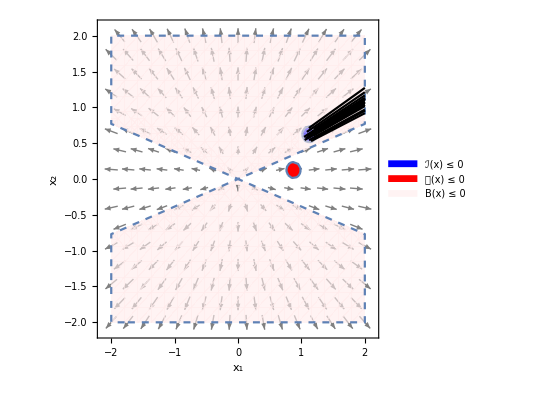

SDP CPU-time elapsed: 4.39492s

Total CPU-time elapsed: 5.04275s

```mathematica
main[varSet19,flowVec19,domainRange19,initialBoundary19,unsafeBoundary19,barrierDegree19,polyDegrees19,paraRange19,LieOrder19,ϵI19,ϵU19,ϵL19,ϵ19,δ19,bilinearUnsafeCons19,posteriorCheck19,verbose19,bcTempDefault19];
```

### raychaudhuri

```mathematica
varSetC17={Subscript[x, 1],Subscript[x, 2], Subscript[x, 3], Subscript[x, 4]};
flowVecC17={1/2 Subscript[x, 1]^2 - 2(Subscript[x, 2]^2 + Subscript[x, 3]^2 - Subscript[x, 4]^2),-Subscript[x, 1] Subscript[x, 2] - 1,-Subscript[x, 1] Subscript[x, 3],-Subscript[x, 1] Subscript[x, 4]};
domainRangeC17={-1.5,1.5};
initialBoundaryC17= Subscript[x, 1]^2 + (Subscript[x, 2]+ 1)^2  - 0.1;
unsafeBoundaryC17= (Subscript[x, 1] + 1)^2 + Subscript[x, 2]^2 - 0.1;
bcTempDefaultC17=Subscript[a, 0000]+Subscript[a, 1000] Subscript[x, 1]+Subscript[a, 2000] Subscript[x, 1]^2+Subscript[a, 0100] Subscript[x, 2]+Subscript[a, 1100] Subscript[x, 1] Subscript[x, 2]+Subscript[a, 0200] Subscript[x, 2]^2;
barrierDegreeC17=polyDegree[bcTempDefaultC17,varSetC17];
polyDegreesC17={0,0,1};
paraRangeC17={-10,10};
LieOrderC17=1;
ϵIC17=ϵUC17=ϵLC17=N[10^-3];
ϵC17=N[10^-2];
δC17=-N[10^-3];
bilinearUnsafeConsC17=True;
posteriorCheckC17=True;
verboseC17=False;
```

```mathematica
main[varSetC17,flowVecC17,domainRangeC17,initialBoundaryC17,unsafeBoundaryC17,barrierDegreeC17,polyDegreesC17,paraRangeC17,LieOrderC17,ϵIC17,ϵUC17,ϵLC17,ϵC17,δC17,bilinearUnsafeConsC17,posteriorCheckC17,verboseC17,bcTempDefaultC17];
```

Template BC: 
a_0000+a_1000 x_1+a_2000 x_1^2+a_0100 x_2+a_1100 x_1 x_2+a_0200 x_2^2

Lie sequence: 
{a_0000+a_1000 x_1+a_2000 x_1^2+a_0100 x_2+a_1100 x_1 x_2+a_0200 x_2^2,-a_0100+a_2000 x_1^3-2 a_1000 x_2^2-2 a_1100 x_2^3+x_1^2 (a_1000/2-1/2 a_1100 x_2)-2 a_1000 x_3^2+2 a_1000 x_4^2+x_2 (-2 a_0200-2 a_1100 x_3^2+2 a_1100 x_4^2)+x_1 (-a_1100-a_0100 x_2-2 (a_0200+2 a_2000) x_2^2-4 a_2000 x_3^2+4 a_2000 x_4^2)}

SOS constraints:
{w_0000,u_0000,-0.001-a_0000+0.9 w_0000+(-a_2000+w_0000) x_1^2+(-a_0100+2 w_0000) x_2+(-a_0200+w_0000) x_2^2+x_1 (-a_1000-a_1100 x_2),0.899+a_0000 u_0000+(1+a_2000 u_0000) x_1^2+a_0100 u_0000 x_2+(1+a_0200 u_0000) x_2^2+x_1 (2+a_1000 u_0000+a_1100 u_0000 x_2),-0.001+a_0100+a_0000 v10_0000+a_2000 (-1+v10_1000) x_1^3+(2 a_1100+a_0200 v10_0100) x_2^3+a_0000 v10_0010 x_3+2 a_1000 x_3^2+a_0000 v10_0001 x_4-2 a_1000 x_4^2+x_2^2 (2 a_1000+a_0200 v10_0000+a_0100 v10_0100+a_0200 v10_0010 x_3+a_0200 v10_0001 x_4)+x_1^2 (a_2000 v10_0000+a_1000 (-1/2+v10_1000)+(a_2000 v10_0100+a_1100 (1/2+v10_1000)) x_2+a_2000 v10_0010 x_3+a_2000 v10_0001 x_4)+x_2 (2 a_0200+a_0100 v10_0000+a_0000 v10_0100+a_0100 v10_0010 x_3+2 a_1100 x_3^2+a_0100 v10_0001 x_4-2 a_1100 x_4^2)+x_1 (a_1100+a_1000 v10_0000+a_0000 v10_1000+(4 a_2000+a_1100 v10_0100+a_0200 (2+v10_1000)) x_2^2+a_1000 v10_0010 x_3+4 a_2000 x_3^2+a_1000 v10_0001 x_4-4 a_2000 x_4^2+x_2 (a_1100 v10_0000+a_1000 v10_0100+a_0100 (1+v10_1000)+a_1100 v10_0010 x_3+a_1100 v10_0001 x_4))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_0000,a_0100,a_0200,a_1000,a_1100,a_2000,λ,w_0000,u_0000,v10_0000,v10_0001,v10_0010,v10_0100,v10_1000}

Variable correspondence:
{a_0000→z_1,a_0100→z_2,a_0200→z_3,a_1000→z_4,a_1100→z_5,a_2000→z_6,λ→z_7,w_0000→z_8,u_0000→z_9,v10_0000→z_10,v10_0001→z_11,v10_0010→z_12,v10_0100→z_13,v10_1000→z_14}

Initial vector:
{a_0000,a_0100,a_0200,a_1000,a_1100,a_2000,λ,1,1,-1,0,0,0,0}

Initial feasible solution:
z^0={z_1→0.0265284,z_2→0.0382372,z_3→-0.0288245,z_4→0.00423657,z_5→-0.00127634,z_6→0.0143864,z_7→-0.0333476,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0,z_13→0,z_14→0}

Initial maximum:
λ^0=-0.0333476

LMI variables:
{a_0000,a_0100,a_0200,a_1000,a_1100,a_2000,λ,w_0000,u_0000,v10_0000,v10_0001,v10_0010,v10_0100,v10_1000,ζ}

Variable correspondence:
{a_0000→z_1,a_0100→z_2,a_0200→z_3,a_1000→z_4,a_1100→z_5,a_2000→z_6,λ→z_7,w_0000→z_8,u_0000→z_9,v10_0000→z_10,v10_0001→z_11,v10_0010→z_12,v10_0100→z_13,v10_1000→z_14,ζ→zz}

Feasible solution:
z^1={z_1→0.0635441,z_2→0.0467195,z_3→0.00690941,z_4→0.0120798,z_5→-0.000231747,z_6→0.000709874,z_7→-0.0246148,z_8→0.118716,z_9→1.03587,z_10→-0.960825,z_11→0.,z_12→0.,z_13→0.0604019,z_14→-0.0429612,zz→-0.000394011}

Maximum:
(λ+ζ)^1=-0.0250088

|z^1-z^0|=0.887706

Feasible solution:
z^2={z_1→0.0629564,z_2→0.0471391,z_3→0.000575682,z_4→0.00965721,z_5→-0.0000426374,z_6→0.00166111,z_7→-0.0219224,z_8→0.125904,z_9→1.07921,z_10→-0.922044,z_11→0.,z_12→0.,z_13→0.124306,z_14→-0.10473,zz→-0.000402705}

Maximum:
(λ+ζ)^2=-0.0223251

|z^2-z^1|=0.106714

Feasible solution:
z^3={z_1→0.061905,z_2→0.0485476,z_3→-0.00225941,z_4→0.00650067,z_5→0.00108185,z_6→0.00164185,z_7→-0.0195716,z_8→0.12832,z_9→1.12419,z_10→-0.890972,z_11→0.,z_12→0.,z_13→0.187057,z_14→-0.166992,zz→-0.00042622}

Maximum:
(λ+ζ)^3=-0.0199978

|z^3-z^2|=0.1041

Feasible solution:
z^4={z_1→0.0610272,z_2→0.0508712,z_3→-0.00434749,z_4→0.00360286,z_5→0.00221363,z_6→0.0015577,z_7→-0.0171903,z_8→0.130909,z_9→1.17036,z_10→-0.865613,z_11→0.,z_12→0.,z_13→0.25014,z_14→-0.230503,zz→-0.000460246}

Maximum:
(λ+ζ)^4=-0.0176506

|z^4-z^3|=0.104023

Feasible solution:
z^5={z_1→0.0603643,z_2→0.0542533,z_3→-0.00590086,z_4→0.000816338,z_5→0.00321739,z_6→0.00145113,z_7→-0.0146648,z_8→0.134051,z_9→1.21752,z_10→-0.844655,z_11→0.,z_12→0.,z_13→0.314668,z_14→-0.295835,zz→-0.000505161}

Maximum:
(λ+ζ)^5=-0.0151699

|z^5-z^4|=0.10552

Feasible solution:
z^6={z_1→0.0599294,z_2→0.0590052,z_3→-0.00694766,z_4→-0.00208157,z_5→0.0039392,z_6→0.00135016,z_7→-0.0118459,z_8→0.137996,z_9→1.26551,z_10→-0.826838,z_11→0.,z_12→0.,z_13→0.381735,z_14→-0.363844,zz→-0.000562179}

Maximum:
(λ+ζ)^6=-0.0124081

|z^6-z^5|=0.108627

Feasible solution:
z^7={z_1→0.0619692,z_2→0.0678012,z_3→-0.00828979,z_4→-0.00333543,z_5→0.00384989,z_6→0.000869354,z_7→-0.00872641,z_8→0.14919,z_9→1.31381,z_10→-0.817947,z_11→0.,z_12→0.,z_13→0.434499,z_14→-0.430482,zz→-0.000616515}

Maximum:
(λ+ζ)^7=-0.00934292

|z^7-z^6|=0.0992862

Feasible solution:
z^8={z_1→0.0640461,z_2→0.0737019,z_3→-0.0102171,z_4→-0.00266315,z_5→0.00308311,z_6→0.000301753,z_7→-0.0067862,z_8→0.162866,z_9→1.36146,z_10→-0.820142,z_11→0.,z_12→0.,z_13→0.458791,z_14→-0.478827,zz→-0.000653772}

Maximum:
(λ+ζ)^8=-0.00743998

|z^8-z^7|=0.0737387

Feasible solution:
z^9={z_1→0.0635625,z_2→0.0741709,z_3→-0.01162,z_4→-0.00241005,z_5→0.00261824,z_6→0.0000651768,z_7→-0.00597129,z_8→0.180685,z_9→1.40742,z_10→-0.825443,z_11→0.,z_12→0.,z_13→0.468659,z_14→-0.508833,zz→-0.000675131}

Maximum:
(λ+ζ)^9=-0.00664642

|z^9-z^8|=0.0588098

Feasible solution:
z^10={z_1→0.0623784,z_2→0.0756536,z_3→-0.0120199,z_4→-0.00231713,z_5→0.00233583,z_6→-0.0000337955,z_7→-0.00560841,z_8→0.231497,z_9→1.45112,z_10→-0.830804,z_11→0.,z_12→0.,z_13→0.473884,z_14→-0.531225,zz→-0.000666749}

Maximum:
(λ+ζ)^10=-0.00627516

|z^10-z^9|=0.0710852

Feasible solution:
z^11={z_1→0.0612705,z_2→0.0786252,z_3→-0.0118474,z_4→-0.00224974,z_5→0.00211368,z_6→-0.0000823039,z_7→-0.0053421,z_8→0.282035,z_9→1.49241,z_10→-0.835988,z_11→0.,z_12→0.,z_13→0.478139,z_14→-0.552549,zz→-0.000661473}

Maximum:
(λ+ζ)^11=-0.00600357

|z^11-z^10|=0.0690608

Feasible solution:
z^12={z_1→0.0603567,z_2→0.0822718,z_3→-0.011611,z_4→-0.00218336,z_5→0.00191088,z_6→-0.000119747,z_7→-0.00509624,z_8→0.330799,z_9→1.53133,z_10→-0.840985,z_11→0.,z_12→0.,z_13→0.481978,z_14→-0.573888,zz→-0.000660761}

Maximum:
(λ+ζ)^12=-0.005757

|z^12-z^11|=0.0663474

Feasible solution:
z^13={z_1→0.0596407,z_2→0.0865406,z_3→-0.0113979,z_4→-0.00211565,z_5→0.00172204,z_6→-0.000150573,z_7→-0.0048622,z_8→0.380911,z_9→1.56793,z_10→-0.845808,z_11→0.,z_12→0.,z_13→0.485474,z_14→-0.595415,zz→-0.000662303}

Maximum:
(λ+ζ)^13=-0.0055245

|z^13-z^12|=0.0660957

Feasible solution:
z^14={z_1→0.0591211,z_2→0.0914566,z_3→-0.0112328,z_4→-0.00204621,z_5→0.00154597,z_6→-0.000176021,z_7→-0.00463757,z_8→0.434031,z_9→1.60227,z_10→-0.850462,z_11→0.,z_12→0.,z_13→0.488599,z_14→-0.617074,zz→-0.000665103}

Maximum:
(λ+ζ)^14=-0.00530267

|z^14-z^13|=0.0672724

Feasible solution:
z^15={z_1→0.0587961,z_2→0.09703,z_3→-0.0111328,z_4→-0.00197527,z_5→0.0013828,z_6→-0.000196607,z_7→-0.00442183,z_8→0.49102,z_9→1.63438,z_10→-0.854951,z_11→0.,z_12→0.,z_13→0.49128,z_14→-0.638692,zz→-0.000668861}

Maximum:
(λ+ζ)^15=-0.00509069

|z^15-z^14|=0.0693149

Feasible solution:
z^16={z_1→0.0586617,z_2→0.103228,z_3→-0.0111142,z_4→-0.00190364,z_5→0.00123334,z_6→-0.000212678,z_7→-0.0042158,z_8→0.552101,z_9→1.66431,z_10→-0.859271,z_11→0.,z_12→0.,z_13→0.493428,z_14→-0.659993,zz→-0.00067373}

Maximum:
(λ+ζ)^16=-0.00488953

|z^16-z^15|=0.0717104

Feasible solution:
z^17={z_1→0.0587072,z_2→0.109947,z_3→-0.0111952,z_4→-0.00183271,z_5→0.00109867,z_6→-0.000224607,z_7→-0.0040214,z_8→0.616799,z_9→1.69212,z_10→-0.863412,z_11→0.,z_12→0.,z_13→0.494953,z_14→-0.68061,zz→-0.000680174}

Maximum:
(λ+ζ)^17=-0.00470157

|z^17-z^16|=0.0738195

Feasible solution:
z^18={z_1→0.0589107,z_2→0.116999,z_3→-0.0113928,z_4→-0.00176443,z_5→0.000979873,z_6→-0.000232904,z_7→-0.0038415,z_8→0.683847,z_9→1.71791,z_10→-0.867357,z_11→0.,z_12→0.,z_13→0.495775,z_14→-0.700115,zz→-0.00068879}

Maximum:
(λ+ζ)^18=-0.00453029

|z^18-z^17|=0.0748804

Feasible solution:
z^19={z_1→0.0592359,z_2→0.12411,z_3→-0.0117182,z_4→-0.00170106,z_5→0.000877661,z_6→-0.000238246,z_7→-0.00367951,z_8→0.751246,z_9→1.74178,z_10→-0.871081,z_11→0.,z_12→0.,z_13→0.495849,z_14→-0.718058,zz→-0.000700042}

Maximum:
(λ+ζ)^19=-0.00437955

|z^19-z^18|=0.0741551

Feasible solution:
z^20={z_1→0.059633,z_2→0.130957,z_3→-0.0121713,z_4→-0.00164468,z_5→0.000792085,z_6→-0.000241413,z_7→-0.00353845,z_8→0.816495,z_9→1.76387,z_10→-0.87456,z_11→0.,z_12→0.,z_13→0.495177,z_14→-0.734037,zz→-0.000714017}

Maximum:
(λ+ζ)^20=-0.00425246

|z^20-z^19|=0.0711382

Feasible solution:
z^21={z_1→0.060046,z_2→0.137222,z_3→-0.0127345,z_4→-0.0015967,z_5→0.000722387,z_6→-0.000243169,z_7→-0.0034201,z_8→0.877053,z_9→1.78434,z_10→-0.877769,z_11→0.,z_12→0.,z_13→0.493807,z_14→-0.747768,zz→-0.000730286}

Maximum:
(λ+ζ)^21=-0.00415038

|z^21-z^20|=0.0657765

Feasible solution:
z^22={z_1→0.0604228,z_2→0.142664,z_3→-0.0133703,z_4→-0.00155748,z_5→0.000667054,z_6→-0.000244132,z_7→-0.00332428,z_8→0.930808,z_9→1.80334,z_10→-0.880697,z_11→0.,z_12→0.,z_13→0.491829,z_14→-0.75913,zz→-0.000747995}

Maximum:
(λ+ζ)^22=-0.00407228

|z^22-z^21|=0.0585002

Feasible solution:
z^23={z_1→0.0607247,z_2→0.147146,z_3→-0.0140267,z_4→-0.00152632,z_5→0.000624068,z_6→-0.0002447,z_7→-0.00324882,z_8→0.976388,z_9→1.82103,z_10→-0.883348,z_11→0.,z_12→0.,z_13→0.489358,z_14→-0.76818,zz→-0.000766117}

Maximum:
(λ+ζ)^23=-0.00401493

|z^23-z^22|=0.0500632

Feasible solution:
z^24={z_1→0.0609623,z_2→0.150865,z_3→-0.0146681,z_4→-0.0015017,z_5→0.000591628,z_6→-0.000244782,z_7→-0.00319004,z_8→0.999999,z_9→1.83752,z_10→-0.885759,z_11→0.,z_12→0.,z_13→0.486532,z_14→-0.775303,zz→-0.000783762}

Maximum:
(λ+ζ)^24=-0.0039738

|z^24-z^23|=0.0301343

Feasible solution:
z^25={z_1→0.0611641,z_2→0.154076,z_3→-0.0152833,z_4→-0.00148186,z_5→0.000567295,z_6→-0.000244405,z_7→-0.00314343,z_8→0.999999,z_9→1.85284,z_10→-0.887987,z_11→0.,z_12→0.,z_13→0.48348,z_14→-0.78102,zz→-0.000799797}

Maximum:
(λ+ζ)^25=-0.00394322

|z^25-z^24|=0.0171038

Feasible solution:
z^26={z_1→0.0613096,z_2→0.15668,z_3→-0.0158397,z_4→-0.00146563,z_5→0.000548073,z_6→-0.000244108,z_7→-0.00310563,z_8→1.,z_9→1.86711,z_10→-0.890056,z_11→0.,z_12→0.,z_13→0.480259,z_14→-0.785537,zz→-0.000814126}

Maximum:
(λ+ζ)^26=-0.00391975

|z^26-z^25|=0.0156758

Feasible solution:
z^27={z_1→0.0613921,z_2→0.158689,z_3→-0.016327,z_4→-0.00145214,z_5→0.000532906,z_6→-0.000243842,z_7→-0.00307454,z_8→1.,z_9→1.88043,z_10→-0.89199,z_11→0.,z_12→0.,z_13→0.476916,z_14→-0.789041,zz→-0.00082695}

Maximum:
(λ+ζ)^27=-0.00390149

|z^27-z^26|=0.0144525

Feasible solution:
z^28={z_1→0.061413,z_2→0.160159,z_3→-0.0167355,z_4→-0.0014407,z_5→0.00052094,z_6→-0.000243576,z_7→-0.00304854,z_8→1.,z_9→1.8929,z_10→-0.893812,z_11→0.,z_12→0.,z_13→0.47349,z_14→-0.791711,zz→-0.000838471}

Maximum:
(λ+ζ)^28=-0.00388702

|z^28-z^27|=0.0134201

Feasible solution:
z^29={z_1→0.0614178,z_2→0.161477,z_3→-0.0166763,z_4→-0.00143091,z_5→0.000510329,z_6→-0.000243567,z_7→-0.00302648,z_8→1.,z_9→1.90465,z_10→-0.895466,z_11→0.,z_12→0.,z_13→0.470101,z_14→-0.793423,zz→-0.000848779}

Maximum:
(λ+ζ)^29=-0.00387526

|z^29-z^28|=0.0125287

Feasible solution:
z^30={z_1→0.0613654,z_2→0.162347,z_3→-0.0165313,z_4→-0.00142226,z_5→0.000502553,z_6→-0.000243506,z_7→-0.00300745,z_8→1.,z_9→1.91571,z_10→-0.897019,z_11→0.,z_12→0.,z_13→0.466762,z_14→-0.794608,zz→-0.000858171}

Maximum:
(λ+ζ)^30=-0.00386562

|z^30-z^29|=0.011752

Feasible solution:
z^31={z_1→0.0612639,z_2→0.162825,z_3→-0.0163674,z_4→-0.00141444,z_5→0.000496501,z_6→-0.00024334,z_7→-0.00299053,z_8→1.,z_9→1.92616,z_10→-0.8985,z_11→0.,z_12→0.,z_13→0.463476,z_14→-0.795429,zz→-0.000866822}

Maximum:
(λ+ζ)^31=-0.00385735

|z^31-z^30|=0.0110921

Feasible solution:
z^32={z_1→0.0611264,z_2→0.16301,z_3→-0.0161901,z_4→-0.00140725,z_5→0.000491639,z_6→-0.000243095,z_7→-0.00297521,z_8→1.,z_9→1.93605,z_10→-0.899923,z_11→0.,z_12→0.,z_13→0.460243,z_14→-0.795983,zz→-0.00087486}

Maximum:
(λ+ζ)^32=-0.00385007

|z^32-z^31|=0.0105245

Feasible solution:
z^33={z_1→0.0609638,z_2→0.162981,z_3→-0.016004,z_4→-0.00140059,z_5→0.000487656,z_6→-0.000242796,z_7→-0.00296113,z_8→1.,z_9→1.94545,z_10→-0.9013,z_11→0.,z_12→0.,z_13→0.457066,z_14→-0.796341,zz→-0.000882385}

Maximum:
(λ+ζ)^33=-0.00384351

|z^33-z^32|=0.0100249

Feasible solution:
z^34={z_1→0.060785,z_2→0.162798,z_3→-0.0158125,z_4→-0.00139436,z_5→0.00048433,z_6→-0.000242466,z_7→-0.00294807,z_8→1.,z_9→1.9544,z_10→-0.902638,z_11→0.,z_12→0.,z_13→0.453946,z_14→-0.796555,zz→-0.000889474}

Maximum:
(λ+ζ)^34=-0.00383754

|z^34-z^33|=0.00957609

Close enough solutions: 0.00957609 ≤ ϵ = 0.01

Barrier certificate candidate:
0.060785-0.00139436 x_1-0.000242466 x_1^2+0.162798 x_2+0.00048433 x_1 x_2-0.0158125 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

SDP CPU-time elapsed: 9.44589s

Total CPU-time elapsed: 16.6802s

### focus

```mathematica
varSetC13={Subscript[x, 1],Subscript[x, 2]};
flowVecC13={Subscript[x, 1] - Subscript[x, 2], Subscript[x, 1] + Subscript[x, 2]};
domainRangeC13={1.5,3.5};
initialBoundaryC13=(Subscript[x, 1] - 2.75)^2 + (5 Subscript[x, 2] - 10)^2 - 0.25^2;
unsafeBoundaryC13=Subscript[x, 1] - 2;
barrierDegreeC13=4;
polyDegreesC13={0,0,1};
paraRangeC13={-10,10};
LieOrderC13=1;
ϵIC13=0;
ϵUC13=ϵLC13=N[10^-3];
ϵC13=N[10^-3];
δC13=-N[10^-3];
bilinearUnsafeConsC13=False;
posteriorCheckC13=True;
verboseC13=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_30 x_1^3+a_40 x_1^4+a_01 x_2+a_11 x_1 x_2+a_21 x_1^2 x_2+a_31 x_1^3 x_2+a_02 x_2^2+a_12 x_1 x_2^2+a_22 x_1^2 x_2^2+a_03 x_2^3+a_13 x_1 x_2^3+a_04 x_2^4

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_30 x_1^3+a_40 x_1^4+a_01 x_2+a_11 x_1 x_2+a_21 x_1^2 x_2+a_31 x_1^3 x_2+a_02 x_2^2+a_12 x_1 x_2^2+a_22 x_1^2 x_2^2+a_03 x_2^3+a_13 x_1 x_2^3+a_04 x_2^4,(a_31+4 a_40) x_1^4+(a_01-a_10) x_2+(2 a_02-a_11) x_2^2+(3 a_03-a_12) x_2^3+(4 a_04-a_13) x_2^4+x_1^3 (a_21+3 a_30+2 (a_22+2 a_31-2 a_40) x_2)+x_1^2 (a_11+2 a_20+(2 a_12+3 a_21-3 a_30) x_2+(3 a_13+4 a_22-3 a_31) x_2^2)+x_1 (a_01+a_10+2 (a_02+a_11-a_20) x_2+(3 a_03+3 a_12-2 a_21) x_2^2+(4 a_04+4 a_13-2 a_22) x_2^3)}

SOS constraints:
{w_00,u_00,-a_00+107.5 w_00-a_40 x_1^4+(-a_01-100 w_00) x_2+(-a_02+25 w_00) x_2^2-a_03 x_2^3-a_04 x_2^4+x_1^3 (-a_30-a_31 x_2)+x_1^2 (-a_20+w_00-a_21 x_2-a_22 x_2^2)+x_1 (-a_10-5.5 w_00-a_11 x_2-a_12 x_2^2-a_13 x_2^3),-0.001+a_00-2 u_00+a_40 x_1^4+a_01 x_2+a_02 x_2^2+a_03 x_2^3+a_04 x_2^4+x_1^3 (a_30+a_31 x_2)+x_1^2 (a_20+a_21 x_2+a_22 x_2^2)+x_1 (a_10+u_00+a_11 x_2+a_12 x_2^2+a_13 x_2^3),-0.001+a_00 v10_00+a_40 v10_10 x_1^5+(a_10+a_01 (-1+v10_00)+a_00 v10_01) x_2+(a_11+a_02 (-2+v10_00)+a_01 v10_01) x_2^2+(a_12+a_03 (-3+v10_00)+a_02 v10_01) x_2^3+(a_13+a_04 (-4+v10_00)+a_03 v10_01) x_2^4+a_04 v10_01 x_2^5+x_1^4 (-a_31+a_40 (-4+v10_00)+a_30 v10_10+(a_40 v10_01+a_31 v10_10) x_2)+x_1^3 (-a_21+a_30 (-3+v10_00)+a_20 v10_10+(-2 a_22+4 a_40+a_31 (-4+v10_00)+a_30 v10_01+a_21 v10_10) x_2+(a_31 v10_01+a_22 v10_10) x_2^2)+x_1^2 (-a_11+a_20 (-2+v10_00)+a_10 v10_10+(-2 a_12+3 a_30+a_21 (-3+v10_00)+a_20 v10_01+a_11 v10_10) x_2+(-3 a_13+3 a_31+a_22 (-4+v10_00)+a_21 v10_01+a_12 v10_10) x_2^2+(a_22 v10_01+a_13 v10_10) x_2^3)+x_1 (-a_01+a_10 (-1+v10_00)+a_00 v10_10+(-2 a_02+2 a_20+a_11 (-2+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(-3 a_03+2 a_21+a_12 (-3+v10_00)+a_11 v10_01+a_02 v10_10) x_2^2+(-4 a_04+2 a_22+a_13 (-4+v10_00)+a_12 v10_01+a_03 v10_10) x_2^3+(a_13 v10_01+a_04 v10_10) x_2^4)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_03,a_04,a_10,a_11,a_12,a_13,a_20,a_21,a_22,a_30,a_31,a_40,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_03→z_4,a_04→z_5,a_10→z_6,a_11→z_7,a_12→z_8,a_13→z_9,a_20→z_10,a_21→z_11,a_22→z_12,a_30→z_13,a_31→z_14,a_40→z_15,λ→z_16,w_00→z_17,u_00→z_18,v10_00→z_19,v10_01→z_20,v10_10→z_21}

Initial vector:
{a_00,a_01,a_02,a_03,a_04,a_10,a_11,a_12,a_13,a_20,a_21,a_22,a_30,a_31,a_40,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→1.08623,z_2→8.86122×10^-9,z_3→0.362409,z_4→0.,z_5→-0.498185,z_6→-6.89041×10^-9,z_7→2.56854×10^-8,z_8→0.,z_9→-0.0883727,z_10→0.362409,z_11→0.,z_12→-0.541827,z_13→0.,z_14→0.0883727,z_15→-0.498185,z_16→-1.08723,z_17→1,z_18→1,z_19→-1,z_20→0,z_21→0}

Initial maximum:
λ^0=-1.08723

LMI variables:
{a_00,a_01,a_02,a_03,a_04,a_10,a_11,a_12,a_13,a_20,a_21,a_22,a_30,a_31,a_40,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_03→z_4,a_04→z_5,a_10→z_6,a_11→z_7,a_12→z_8,a_13→z_9,a_20→z_10,a_21→z_11,a_22→z_12,a_30→z_13,a_31→z_14,a_40→z_15,λ→z_16,w_00→z_17,u_00→z_18,v10_00→z_19,v10_01→z_20,v10_10→z_21,ζ→zz}

Feasible solution:
z^1={z_1→-0.117098,z_2→-0.0075589,z_3→-0.0593336,z_4→0.00369017,z_5→-0.0467958,z_6→0.0109312,z_7→0.0050932,z_8→-0.000199867,z_9→-0.00189487,z_10→-0.0525913,z_11→0.00292845,z_12→-0.0614514,z_13→0.0000853687,z_14→0.000310372,z_15→-0.0504461,z_16→-0.0615146,z_17→1.,z_18→-0.042509,z_19→-0.515275,z_20→-0.0382925,z_21→0.020591,zz→-0.00241215}

Maximum:
(λ+ζ)^1=-0.0639267

|z^1-z^0|=2.19643

Feasible solution:
z^2={z_1→-0.00102975,z_2→-0.000152471,z_3→-0.000715811,z_4→1.41751×10^-10,z_5→-0.000747179,z_6→0.000457803,z_7→0.000100861,z_8→-1.24023×10^-10,z_9→4.08957×10^-9,z_10→-0.00064765,z_11→-0.0000646987,z_12→-0.000747179,z_13→0.0000271162,z_14→5.0861×10^-9,z_15→-0.000481181,z_16→-0.00074718,z_17→0.265932,z_18→-0.000747185,z_19→-0.594931,z_20→-0.0215228,z_21→0.00596884,zz→-0.00256736}

Maximum:
(λ+ζ)^2=-0.00331454

|z^2-z^1|=0.761089

Feasible solution:
z^3={z_1→-0.00074777,z_2→0.000374724,z_3→-0.000293003,z_4→8.01957×10^-13,z_5→-0.000618534,z_6→0.000188542,z_7→-0.000747093,z_8→6.94174×10^-13,z_9→-6.76929×10^-10,z_10→-0.000189893,z_11→1.16034×10^-12,z_12→-0.000618534,z_13→-9.57153×10^-13,z_14→6.76823×10^-10,z_15→-0.000618534,z_16→-0.000618535,z_17→0.222865,z_18→-0.000618536,z_19→-0.599105,z_20→-0.0212362,z_21→0.00602,zz→-0.00259766}

Maximum:
(λ+ζ)^3=-0.0032162

|z^3-z^2|=0.0432894

Feasible solution:
z^4={z_1→-0.000745118,z_2→0.000373726,z_3→-0.000291729,z_4→7.91167×10^-13,z_5→-0.000617439,z_6→0.000189625,z_7→-0.000745706,z_8→6.69658×10^-13,z_9→-6.78951×10^-10,z_10→-0.000190625,z_11→1.10363×10^-12,z_12→-0.000617439,z_13→-9.15573×10^-13,z_14→6.78851×10^-10,z_15→-0.000617439,z_16→-0.00061744,z_17→0.222471,z_18→-0.000617441,z_19→-0.603055,z_20→-0.0209593,z_21→0.00610466,zz→-0.00259638}

Maximum:
(λ+ζ)^4=-0.00321382

|z^4-z^3|=0.00398052

Feasible solution:
z^5={z_1→-0.000742326,z_2→0.000373026,z_3→-0.000290502,z_4→7.84481×10^-13,z_5→-0.000616358,z_6→0.000190196,z_7→-0.000744555,z_8→6.63636×10^-13,z_9→-6.81328×10^-10,z_10→-0.000191051,z_11→1.08687×10^-12,z_12→-0.000616358,z_13→-9.04368×10^-13,z_14→6.8123×10^-10,z_15→-0.000616358,z_16→-0.000616359,z_17→0.222079,z_18→-0.00061636,z_19→-0.606985,z_20→-0.0206848,z_21→0.00618657,zz→-0.00259513}

Maximum:
(λ+ζ)^5=-0.00321149

|z^5-z^4|=0.00395939

Feasible solution:
z^6={z_1→-0.000739569,z_2→0.000372332,z_3→-0.000289294,z_4→7.76605×10^-13,z_5→-0.000615292,z_6→0.000190757,z_7→-0.000743416,z_8→6.56562×10^-13,z_9→-6.82765×10^-10,z_10→-0.000191468,z_11→1.06898×10^-12,z_12→-0.000615292,z_13→-8.92093×10^-13,z_14→6.8267×10^-10,z_15→-0.000615292,z_16→-0.000615293,z_17→0.221691,z_18→-0.000615294,z_19→-0.610893,z_20→-0.0204128,z_21→0.00626571,zz→-0.0025939}

Maximum:
(λ+ζ)^6=-0.00320919

|z^6-z^5|=0.00393774

Feasible solution:
z^7={z_1→-0.000736847,z_2→0.000371644,z_3→-0.000288105,z_4→7.69012×10^-13,z_5→-0.000614239,z_6→0.000191309,z_7→-0.000742288,z_8→6.49715×10^-13,z_9→-6.8455×10^-10,z_10→-0.000191877,z_11→1.05214×10^-12,z_12→-0.000614239,z_13→-8.80549×10^-13,z_14→6.84457×10^-10,z_15→-0.000614239,z_16→-0.00061424,z_17→0.221308,z_18→-0.000614241,z_19→-0.61478,z_20→-0.0201433,z_21→0.00634208,zz→-0.00259268}

Maximum:
(λ+ζ)^7=-0.00320692

|z^7-z^6|=0.00391603

Feasible solution:
z^8={z_1→-0.00073416,z_2→0.000370961,z_3→-0.000286935,z_4→7.61125×10^-13,z_5→-0.0006132,z_6→0.000191851,z_7→-0.00074117,z_8→6.426×10^-13,z_9→-6.86162×10^-10,z_10→-0.000192278,z_11→1.03546×10^-12,z_12→-0.0006132,z_13→-8.69016×10^-13,z_14→6.86071×10^-10,z_15→-0.0006132,z_16→-0.000613201,z_17→0.22093,z_18→-0.000613202,z_19→-0.618646,z_20→-0.0198762,z_21→0.00641565,zz→-0.00259149}

Maximum:
(λ+ζ)^8=-0.00320469

|z^8-z^7|=0.00389428

Feasible solution:
z^9={z_1→-0.000731507,z_2→0.000370285,z_3→-0.000285783,z_4→7.53052×10^-13,z_5→-0.000612174,z_6→0.000192383,z_7→-0.000740063,z_8→6.35307×10^-13,z_9→-6.87678×10^-10,z_10→-0.00019267,z_11→1.01908×10^-12,z_12→-0.000612174,z_13→-8.57591×10^-13,z_14→6.8759×10^-10,z_15→-0.000612174,z_16→-0.000612175,z_17→0.220556,z_18→-0.000612176,z_19→-0.622491,z_20→-0.0196116,z_21→0.00648641,zz→-0.00259032}

Maximum:
(λ+ζ)^9=-0.00320249

|z^9-z^8|=0.00387249

Feasible solution:
z^10={z_1→-0.000728888,z_2→0.000369614,z_3→-0.000284649,z_4→7.44771×10^-13,z_5→-0.000611161,z_6→0.000192907,z_7→-0.000738967,z_8→6.27823×10^-13,z_9→-6.8907×10^-10,z_10→-0.000193054,z_11→1.00294×10^-12,z_12→-0.000611161,z_13→-8.46242×10^-13,z_14→6.88984×10^-10,z_15→-0.000611161,z_16→-0.000611162,z_17→0.220187,z_18→-0.000611163,z_19→-0.626314,z_20→-0.0193495,z_21→0.00655436,zz→-0.00258916}

Maximum:
(λ+ζ)^10=-0.00320032

|z^10-z^9|=0.00385066

Feasible solution:
z^11={z_1→-0.000726302,z_2→0.00036895,z_3→-0.000283533,z_4→7.36301×10^-13,z_5→-0.000610161,z_6→0.000193421,z_7→-0.000737882,z_8→6.20167×10^-13,z_9→-6.90344×10^-10,z_10→-0.000193431,z_11→9.8705×10^-13,z_12→-0.000610161,z_13→-8.34981×10^-13,z_14→6.90261×10^-10,z_15→-0.000610161,z_16→-0.000610162,z_17→0.219822,z_18→-0.000610163,z_19→-0.630116,z_20→-0.0190897,z_21→0.00661947,zz→-0.00258803}

Maximum:
(λ+ζ)^11=-0.00319819

|z^11-z^10|=0.00382879

Feasible solution:
z^12={z_1→-0.000723749,z_2→0.000368291,z_3→-0.000282434,z_4→7.27681×10^-13,z_5→-0.000609174,z_6→0.000193926,z_7→-0.000736807,z_8→6.12374×10^-13,z_9→-6.91523×10^-10,z_10→-0.000193799,z_11→9.71449×10^-13,z_12→-0.000609174,z_13→-8.23837×10^-13,z_14→6.91442×10^-10,z_15→-0.000609174,z_16→-0.000609175,z_17→0.219462,z_18→-0.000609176,z_19→-0.633896,z_20→-0.0188324,z_21→0.00668174,zz→-0.00258691}

Maximum:
(λ+ζ)^12=-0.00319609

|z^12-z^11|=0.00380689

Feasible solution:
z^13={z_1→-0.000721228,z_2→0.000367638,z_3→-0.000281352,z_4→6.93741×10^-13,z_5→-0.0006082,z_6→0.000194424,z_7→-0.000735743,z_8→5.82681×10^-13,z_9→-6.68022×10^-10,z_10→-0.000194161,z_11→9.20988×10^-13,z_12→-0.0006082,z_13→-7.82917×10^-13,z_14→6.67946×10^-10,z_15→-0.0006082,z_16→-0.000608201,z_17→0.219106,z_18→-0.000608202,z_19→-0.637656,z_20→-0.0185775,z_21→0.00674116,zz→-0.00258581}

Maximum:
(λ+ζ)^13=-0.00319402

|z^13-z^12|=0.00378495

Feasible solution:
z^14={z_1→-0.000718738,z_2→0.000366991,z_3→-0.000280286,z_4→6.84173×10^-13,z_5→-0.000607238,z_6→0.000194912,z_7→-0.00073469,z_8→5.74046×10^-13,z_9→-6.67994×10^-10,z_10→-0.000194515,z_11→9.05261×10^-13,z_12→-0.000607238,z_13→-7.71292×10^-13,z_14→6.6792×10^-10,z_15→-0.000607238,z_16→-0.000607239,z_17→0.218754,z_18→-0.00060724,z_19→-0.641393,z_20→-0.0183249,z_21→0.00679772,zz→-0.00258474}

Maximum:
(λ+ζ)^14=-0.00319198

|z^14-z^13|=0.00376298

Feasible solution:
z^15={z_1→-0.00071628,z_2→0.00036635,z_3→-0.000279238,z_4→6.75428×10^-13,z_5→-0.000606289,z_6→0.000195392,z_7→-0.000733647,z_8→5.66111×10^-13,z_9→-6.68784×10^-10,z_10→-0.000194861,z_11→8.9115×10^-13,z_12→-0.000606289,z_13→-7.6091×10^-13,z_14→6.68712×10^-10,z_15→-0.000606289,z_16→-0.00060629,z_17→0.218407,z_18→-0.000606291,z_19→-0.645109,z_20→-0.0180747,z_21→0.00685143,zz→-0.00258368}

Maximum:
(λ+ζ)^15=-0.00318997

|z^15-z^14|=0.00374099

Feasible solution:
z^16={z_1→-0.000713853,z_2→0.000365715,z_3→-0.000278205,z_4→6.67403×10^-13,z_5→-0.000605351,z_6→0.000195864,z_7→-0.000732614,z_8→5.5879×10^-13,z_9→-6.70313×10^-10,z_10→-0.000195201,z_11→8.78458×10^-13,z_12→-0.000605351,z_13→-7.5162×10^-13,z_14→6.70244×10^-10,z_15→-0.000605351,z_16→-0.000605352,z_17→0.218064,z_18→-0.000605353,z_19→-0.648804,z_20→-0.0178269,z_21→0.00690227,zz→-0.00258264}

Maximum:
(λ+ζ)^16=-0.00318799

|z^16-z^15|=0.00371897

Feasible solution:
z^17={z_1→-0.000711456,z_2→0.000365085,z_3→-0.000277188,z_4→6.5998×10^-13,z_5→-0.000604426,z_6→0.000196327,z_7→-0.000731592,z_8→5.51981×10^-13,z_9→-6.72487×10^-10,z_10→-0.000195533,z_11→8.67002×10^-13,z_12→-0.000604426,z_13→-7.43271×10^-13,z_14→6.72419×10^-10,z_15→-0.000604426,z_16→-0.000604427,z_17→0.217724,z_18→-0.000604428,z_19→-0.652476,z_20→-0.0175814,z_21→0.00695025,zz→-0.00258161}

Maximum:
(λ+ζ)^17=-0.00318604

|z^17-z^16|=0.00369693

Feasible solution:
z^18={z_1→-0.00070909,z_2→0.000364461,z_3→-0.000276187,z_4→6.5278×10^-13,z_5→-0.000603512,z_6→0.000196783,z_7→-0.000730579,z_8→5.45363×10^-13,z_9→-6.7493×10^-10,z_10→-0.000195859,z_11→8.56203×10^-13,z_12→-0.000603512,z_13→-7.35389×10^-13,z_14→6.74864×10^-10,z_15→-0.000603512,z_16→-0.000603513,z_17→0.217389,z_18→-0.000603514,z_19→-0.656128,z_20→-0.0173383,z_21→0.00699536,zz→-0.00258061}

Maximum:
(λ+ζ)^18=-0.00318412

|z^18-z^17|=0.00367487

Feasible solution:
z^19={z_1→-0.000706753,z_2→0.000363843,z_3→-0.000275201,z_4→6.45778×10^-13,z_5→-0.00060261,z_6→0.000197231,z_7→-0.000729577,z_8→5.38917×10^-13,z_9→-6.77622×10^-10,z_10→-0.000196178,z_11→8.46021×10^-13,z_12→-0.00060261,z_13→-7.27941×10^-13,z_14→6.77558×10^-10,z_15→-0.00060261,z_16→-0.000602611,z_17→0.217058,z_18→-0.000602612,z_19→-0.659757,z_20→-0.0170975,z_21→0.0070376,zz→-0.00257962}

Maximum:
(λ+ζ)^19=-0.00318223

|z^19-z^18|=0.0036528

Feasible solution:
z^20={z_1→-0.000704445,z_2→0.000363231,z_3→-0.00027423,z_4→6.38776×10^-13,z_5→-0.000601719,z_6→0.000197672,z_7→-0.000728585,z_8→5.32474×10^-13,z_9→-6.80357×10^-10,z_10→-0.000196491,z_11→8.3615×10^-13,z_12→-0.000601719,z_13→-7.20674×10^-13,z_14→6.80294×10^-10,z_15→-0.000601719,z_16→-0.00060172,z_17→0.216731,z_18→-0.000601721,z_19→-0.663365,z_20→-0.0168589,z_21→0.00707698,zz→-0.00257865}

Maximum:
(λ+ζ)^20=-0.00318037

|z^20-z^19|=0.0036307

Feasible solution:
z^21={z_1→-0.000702165,z_2→0.000362624,z_3→-0.000273274,z_4→6.31705×10^-13,z_5→-0.000600839,z_6→0.000198105,z_7→-0.000727603,z_8→5.25979×10^-13,z_9→-6.83054×10^-10,z_10→-0.000196797,z_11→8.26483×10^-13,z_12→-0.000600839,z_13→-7.13497×10^-13,z_14→6.82993×10^-10,z_15→-0.000600839,z_16→-0.00060084,z_17→0.216408,z_18→-0.000600841,z_19→-0.666951,z_20→-0.0166227,z_21→0.0071135,zz→-0.0025777}

Maximum:
(λ+ζ)^21=-0.00317854

|z^21-z^20|=0.0036086

Feasible solution:
z^22={z_1→-0.000699915,z_2→0.000362023,z_3→-0.000272332,z_4→6.24348×10^-13,z_5→-0.000599971,z_6→0.000198531,z_7→-0.000726631,z_8→5.19248×10^-13,z_9→-6.85462×10^-10,z_10→-0.000197098,z_11→8.16674×10^-13,z_12→-0.000599971,z_13→-7.06124×10^-13,z_14→6.85403×10^-10,z_15→-0.000599971,z_16→-0.000599972,z_17→0.216089,z_18→-0.000599973,z_19→-0.670516,z_20→-0.0163887,z_21→0.00714717,zz→-0.00257676}

Maximum:
(λ+ζ)^22=-0.00317673

|z^22-z^21|=0.00358649

Feasible solution:
z^23={z_1→-0.000697692,z_2→0.000361428,z_3→-0.000271404,z_4→6.16832×10^-13,z_5→-0.000599113,z_6→0.000198949,z_7→-0.000725669,z_8→5.12392×10^-13,z_9→-6.87711×10^-10,z_10→-0.000197392,z_11→8.06912×10^-13,z_12→-0.000599113,z_13→-6.98713×10^-13,z_14→6.87654×10^-10,z_15→-0.000599113,z_16→-0.000599114,z_17→0.215774,z_18→-0.000599115,z_19→-0.674058,z_20→-0.016157,z_21→0.00717798,zz→-0.00257584}

Maximum:
(λ+ζ)^23=-0.00317496

|z^23-z^22|=0.00356437

Feasible solution:
z^24={z_1→-0.000695497,z_2→0.000360838,z_3→-0.000270491,z_4→6.08968×10^-13,z_5→-0.000598266,z_6→0.000199361,z_7→-0.000724717,z_8→5.0525×10^-13,z_9→-6.89567×10^-10,z_10→-0.00019768,z_11→7.96897×10^-13,z_12→-0.000598266,z_13→-6.91013×10^-13,z_14→6.89511×10^-10,z_15→-0.000598266,z_16→-0.000598267,z_17→0.215462,z_18→-0.000598268,z_19→-0.677579,z_20→-0.0159275,z_21→0.00720594,zz→-0.00257494}

Maximum:
(λ+ζ)^24=-0.00317321

|z^24-z^23|=0.00354224

Feasible solution:
z^25={z_1→-0.000693328,z_2→0.000360254,z_3→-0.000269591,z_4→6.00913×10^-13,z_5→-0.00059743,z_6→0.000199766,z_7→-0.000723775,z_8→4.9796×10^-13,z_9→-6.91193×10^-10,z_10→-0.000197963,z_11→7.86852×10^-13,z_12→-0.00059743,z_13→-6.83213×10^-13,z_14→6.91139×10^-10,z_15→-0.00059743,z_16→-0.000597431,z_17→0.215154,z_18→-0.000597432,z_19→-0.681078,z_20→-0.0157002,z_21→0.00723107,zz→-0.00257406}

Maximum:
(λ+ζ)^25=-0.00317149

|z^25-z^24|=0.00352012

Feasible solution:
z^26={z_1→-0.000691187,z_2→0.000359675,z_3→-0.000268705,z_4→5.92612×10^-13,z_5→-0.000596604,z_6→0.000200164,z_7→-0.000722842,z_8→4.90472×10^-13,z_9→-6.92502×10^-10,z_10→-0.00019824,z_11→7.76659×10^-13,z_12→-0.000596604,z_13→-6.75217×10^-13,z_14→6.92449×10^-10,z_15→-0.000596604,z_16→-0.000596605,z_17→0.21485,z_18→-0.000596606,z_19→-0.684556,z_20→-0.0154752,z_21→0.00725338,zz→-0.00257319}

Maximum:
(λ+ζ)^26=-0.00316979

|z^26-z^25|=0.00349799

Feasible solution:
z^27={z_1→-0.000689073,z_2→0.000359102,z_3→-0.000267832,z_4→5.83989×10^-13,z_5→-0.000595789,z_6→0.000200555,z_7→-0.000721918,z_8→4.8273×10^-13,z_9→-6.93389×10^-10,z_10→-0.000198511,z_11→7.66215×10^-13,z_12→-0.000595789,z_13→-6.66937×10^-13,z_14→6.93338×10^-10,z_15→-0.000595789,z_16→-0.00059579,z_17→0.214549,z_18→-0.000595791,z_19→-0.688011,z_20→-0.0152523,z_21→0.00727286,zz→-0.00257233}

Maximum:
(λ+ζ)^27=-0.00316812

|z^27-z^26|=0.00347587

Feasible solution:
z^28={z_1→-0.000686984,z_2→0.000358534,z_3→-0.000266972,z_4→5.75183×10^-13,z_5→-0.000594984,z_6→0.00020094,z_7→-0.000721005,z_8→4.74849×10^-13,z_9→-6.93996×10^-10,z_10→-0.000198777,z_11→7.55695×10^-13,z_12→-0.000594984,z_13→-6.58524×10^-13,z_14→6.93946×10^-10,z_15→-0.000594984,z_16→-0.000594985,z_17→0.214252,z_18→-0.000594986,z_19→-0.691445,z_20→-0.0150316,z_21→0.00728954,zz→-0.0025715}

Maximum:
(λ+ζ)^28=-0.00316648

|z^28-z^27|=0.00345375

Feasible solution:
z^29={z_1→-0.000684921,z_2→0.000357972,z_3→-0.000266125,z_4→5.66207×10^-13,z_5→-0.000594189,z_6→0.000201319,z_7→-0.0007201,z_8→4.66842×10^-13,z_9→-6.94322×10^-10,z_10→-0.000199038,z_11→7.45109×10^-13,z_12→-0.000594189,z_13→-6.49986×10^-13,z_14→6.94273×10^-10,z_15→-0.000594189,z_16→-0.00059419,z_17→0.213959,z_18→-0.000594191,z_19→-0.694857,z_20→-0.0148131,z_21→0.00730343,zz→-0.00257068}

Maximum:
(λ+ζ)^29=-0.00316487

|z^29-z^28|=0.00343164

Feasible solution:
z^30={z_1→-0.000682884,z_2→0.000357415,z_3→-0.00026529,z_4→5.57029×10^-13,z_5→-0.000593403,z_6→0.000201691,z_7→-0.000719206,z_8→4.58683×10^-13,z_9→-6.94309×10^-10,z_10→-0.000199293,z_11→7.34392×10^-13,z_12→-0.000593404,z_13→-6.41273×10^-13,z_14→6.94262×10^-10,z_15→-0.000593403,z_16→-0.000593404,z_17→0.213669,z_18→-0.000593406,z_19→-0.698247,z_20→-0.0145967,z_21→0.00731453,zz→-0.00256987}

Maximum:
(λ+ζ)^30=-0.00316328

|z^30-z^29|=0.00340953

Feasible solution:
z^31={z_1→-0.000680871,z_2→0.000356863,z_3→-0.000264468,z_4→5.47704×10^-13,z_5→-0.000592628,z_6→0.000202057,z_7→-0.00071832,z_8→4.50423×10^-13,z_9→-6.94011×10^-10,z_10→-0.000199544,z_11→7.23619×10^-13,z_12→-0.000592628,z_13→-6.32447×10^-13,z_14→6.93966×10^-10,z_15→-0.000592628,z_16→-0.000592629,z_17→0.213382,z_18→-0.00059263,z_19→-0.701616,z_20→-0.0143824,z_21→0.00732287,zz→-0.00256908}

Maximum:
(λ+ζ)^31=-0.00316171

|z^31-z^30|=0.00338744

Feasible solution:
z^32={z_1→-0.000678884,z_2→0.000356317,z_3→-0.000263658,z_4→5.38249×10^-13,z_5→-0.000591862,z_6→0.000202418,z_7→-0.000717444,z_8→4.42073×10^-13,z_9→-6.93429×10^-10,z_10→-0.000199789,z_11→7.12789×10^-13,z_12→-0.000591862,z_13→-6.23512×10^-13,z_14→6.93385×10^-10,z_15→-0.000591862,z_16→-0.000591863,z_17→0.213099,z_18→-0.000591864,z_19→-0.704963,z_20→-0.0141703,z_21→0.00732846,zz→-0.00256831}

Maximum:
(λ+ζ)^32=-0.00316017

|z^32-z^31|=0.00336537

Feasible solution:
z^33={z_1→-0.000676921,z_2→0.000355776,z_3→-0.00026286,z_4→5.28765×10^-13,z_5→-0.000591106,z_6→0.000202772,z_7→-0.000716576,z_8→4.33721×10^-13,z_9→-6.92682×10^-10,z_10→-0.00020003,z_11→7.02051×10^-13,z_12→-0.000591106,z_13→-6.14595×10^-13,z_14→6.9264×10^-10,z_15→-0.000591106,z_16→-0.000591107,z_17→0.21282,z_18→-0.000591108,z_19→-0.708288,z_20→-0.0139602,z_21→0.00733131,zz→-0.00256755}

Maximum:
(λ+ζ)^33=-0.00315866

|z^33-z^32|=0.00334331

Feasible solution:
z^34={z_1→-0.000674982,z_2→0.00035524,z_3→-0.000262074,z_4→5.19141×10^-13,z_5→-0.000590359,z_6→0.000203121,z_7→-0.000715718,z_8→4.25275×10^-13,z_9→-6.9161×10^-10,z_10→-0.000200266,z_11→6.91212×10^-13,z_12→-0.000590359,z_13→-6.05536×10^-13,z_14→6.91569×10^-10,z_15→-0.000590359,z_16→-0.00059036,z_17→0.212543,z_18→-0.000590361,z_19→-0.711591,z_20→-0.0137523,z_21→0.00733144,zz→-0.0025668}

Maximum:
(λ+ζ)^34=-0.00315716

|z^34-z^33|=0.00332126

Feasible solution:
z^35={z_1→-0.000673066,z_2→0.00035471,z_3→-0.0002613,z_4→5.09509×10^-13,z_5→-0.000589621,z_6→0.000203464,z_7→-0.000714869,z_8→4.16844×10^-13,z_9→-6.90369×10^-10,z_10→-0.000200497,z_11→6.80456×10^-13,z_12→-0.000589621,z_13→-5.96493×10^-13,z_14→6.9033×10^-10,z_15→-0.000589621,z_16→-0.000589622,z_17→0.21227,z_18→-0.000589623,z_19→-0.714872,z_20→-0.0135464,z_21→0.00732888,zz→-0.00256607}

Maximum:
(λ+ζ)^35=-0.0031557

|z^35-z^34|=0.00329924

Feasible solution:
z^36={z_1→-0.000671174,z_2→0.000354184,z_3→-0.000260536,z_4→4.99912×10^-13,z_5→-0.000588893,z_6→0.000203801,z_7→-0.000714029,z_8→4.08467×10^-13,z_9→-6.89019×10^-10,z_10→-0.000200724,z_11→6.69854×10^-13,z_12→-0.000588893,z_13→-5.87526×10^-13,z_14→6.88981×10^-10,z_15→-0.000588893,z_16→-0.000588894,z_17→0.212001,z_18→-0.000588895,z_19→-0.718132,z_20→-0.0133425,z_21→0.00732363,zz→-0.00256536}

Maximum:
(λ+ζ)^36=-0.00315425

|z^36-z^35|=0.00327725

Feasible solution:
z^37={z_1→-0.000669305,z_2→0.000353664,z_3→-0.000259784,z_4→4.90272×10^-13,z_5→-0.000588173,z_6→0.000204133,z_7→-0.000713197,z_8→4.00079×10^-13,z_9→-6.87436×10^-10,z_10→-0.000200946,z_11→6.59261×10^-13,z_12→-0.000588173,z_13→-5.78517×10^-13,z_14→6.87399×10^-10,z_15→-0.000588173,z_16→-0.000588174,z_17→0.211734,z_18→-0.000588175,z_19→-0.72137,z_20→-0.0131407,z_21→0.00731572,zz→-0.00256466}

Maximum:
(λ+ζ)^37=-0.00315283

|z^37-z^36|=0.00325528

Feasible solution:
z^38={z_1→-0.000667458,z_2→0.000353145,z_3→-0.000259047,z_4→9.46052×10^-12,z_5→-0.000587423,z_6→0.000204461,z_7→-0.000712366,z_8→7.66363×10^-12,z_9→-1.34663×10^-8,z_10→-0.000201167,z_11→1.24775×10^-11,z_12→-0.000587425,z_13→-1.10293×10^-11,z_14→1.34656×10^-8,z_15→-0.000587423,z_16→-0.000587449,z_17→0.21147,z_18→-0.000587464,z_19→-0.724586,z_20→-0.0129408,z_21→0.00730517,zz→-0.00256397}

Maximum:
(λ+ζ)^38=-0.00315142

|z^38-z^37|=0.00323337

Feasible solution:
z^39={z_1→-0.000665634,z_2→0.000352635,z_3→-0.000258317,z_4→9.25902×10^-12,z_5→-0.000586721,z_6→0.000204782,z_7→-0.000711552,z_8→7.49045×10^-12,z_9→-1.34108×10^-8,z_10→-0.000201381,z_11→1.22585×10^-11,z_12→-0.000586723,z_13→-1.08401×10^-11,z_14→1.34101×10^-8,z_15→-0.000586721,z_16→-0.000586748,z_17→0.21121,z_18→-0.000586762,z_19→-0.727781,z_20→-0.012743,z_21→0.007292,zz→-0.0025633}

Maximum:
(λ+ζ)^39=-0.00315005

|z^39-z^38|=0.00321143

Feasible solution:
z^40={z_1→-0.000663833,z_2→0.00035213,z_3→-0.000257597,z_4→9.05475×10^-12,z_5→-0.000586028,z_6→0.000205098,z_7→-0.000710747,z_8→7.31559×10^-12,z_9→-1.33467×10^-8,z_10→-0.00020159,z_11→1.20372×10^-11,z_12→-0.00058603,z_13→-1.06477×10^-11,z_14→1.33461×10^-8,z_15→-0.000586028,z_16→-0.000586054,z_17→0.210953,z_18→-0.000586069,z_19→-0.730954,z_20→-0.0125472,z_21→0.00727623,zz→-0.00256264}

Maximum:
(λ+ζ)^40=-0.00314869

|z^40-z^39|=0.00318955

Feasible solution:
z^41={z_1→-0.000662054,z_2→0.00035163,z_3→-0.000256888,z_4→8.85537×10^-12,z_5→-0.000585344,z_6→0.000205409,z_7→-0.00070995,z_8→7.14529×10^-12,z_9→-1.3285×10^-8,z_10→-0.000201796,z_11→1.18234×10^-11,z_12→-0.000585346,z_13→-1.0461×10^-11,z_14→1.32844×10^-8,z_15→-0.000585344,z_16→-0.00058537,z_17→0.210699,z_18→-0.000585384,z_19→-0.734106,z_20→-0.0123533,z_21→0.00725788,zz→-0.00256199}

Maximum:
(λ+ζ)^41=-0.00314736

|z^41-z^40|=0.0031677

Feasible solution:
z^42={z_1→-0.000660296,z_2→0.000351135,z_3→-0.000256189,z_4→8.66075×10^-12,z_5→-0.000584667,z_6→0.000205716,z_7→-0.000709161,z_8→6.97946×10^-12,z_9→-1.32257×10^-8,z_10→-0.000201997,z_11→1.16171×10^-11,z_12→-0.00058467,z_13→-1.028×10^-11,z_14→1.32251×10^-8,z_15→-0.000584667,z_16→-0.000584694,z_17→0.210447,z_18→-0.000584708,z_19→-0.737236,z_20→-0.0121613,z_21→0.00723699,zz→-0.00256136}

Maximum:
(λ+ζ)^42=-0.00314605

|z^42-z^41|=0.00314588

Feasible solution:
z^43={z_1→-0.000658559,z_2→0.000350645,z_3→-0.0002555,z_4→8.46777×10^-12,z_5→-0.000584,z_6→0.000206017,z_7→-0.000708381,z_8→6.81556×10^-12,z_9→-1.3164×10^-8,z_10→-0.000202195,z_11→1.14138×10^-11,z_12→-0.000584002,z_13→-1.01007×10^-11,z_14→1.31634×10^-8,z_15→-0.000584,z_16→-0.000584026,z_17→0.210199,z_18→-0.00058404,z_19→-0.740344,z_20→-0.0119713,z_21→0.00721356,zz→-0.00256074}

Maximum:
(λ+ζ)^43=-0.00314477

|z^43-z^42|=0.00312411

Feasible solution:
z^44={z_1→-0.000656844,z_2→0.00035016,z_3→-0.000254821,z_4→8.27596×10^-12,z_5→-0.00058334,z_6→0.000206313,z_7→-0.00070761,z_8→6.65316×10^-12,z_9→-1.30991×10^-8,z_10→-0.000202389,z_11→1.12124×10^-11,z_12→-0.000583342,z_13→-9.92234×10^-12,z_14→1.30985×10^-8,z_15→-0.00058334,z_16→-0.000583366,z_17→0.209954,z_18→-0.00058338,z_19→-0.743431,z_20→-0.0117832,z_21→0.00718763,zz→-0.00256013}

Maximum:
(λ+ζ)^44=-0.0031435

|z^44-z^43|=0.00310237

Feasible solution:
z^45={z_1→-0.00065515,z_2→0.00034968,z_3→-0.000254152,z_4→8.0894×10^-12,z_5→-0.000582688,z_6→0.000206605,z_7→-0.000706846,z_8→6.49563×10^-12,z_9→-1.30374×10^-8,z_10→-0.000202579,z_11→1.10188×10^-11,z_12→-0.000582691,z_13→-9.75×10^-12,z_14→1.30368×10^-8,z_15→-0.000582688,z_16→-0.000582714,z_17→0.209712,z_18→-0.000582728,z_19→-0.746496,z_20→-0.011597,z_21→0.00715923,zz→-0.00255954}

Maximum:
(λ+ζ)^45=-0.00314225

|z^45-z^44|=0.00308068

Feasible solution:
z^46={z_1→-0.000653476,z_2→0.000349204,z_3→-0.000253492,z_4→7.73232×10^-12,z_5→-0.000582046,z_6→0.000206893,z_7→-0.000706091,z_8→6.19972×10^-12,z_9→-1.26888×10^-8,z_10→-0.000202766,z_11→1.05828×10^-11,z_12→-0.000582048,z_13→-9.36346×10^-12,z_14→1.26883×10^-8,z_15→-0.000582046,z_16→-0.000582071,z_17→0.209472,z_18→-0.000582084,z_19→-0.74954,z_20→-0.0114127,z_21→0.00712837,zz→-0.00255896}

Maximum:
(λ+ζ)^46=-0.00314103

|z^46-z^45|=0.00305902

Feasible solution:
z^47={z_1→-0.000651822,z_2→0.000348733,z_3→-0.000252842,z_4→7.54626×10^-12,z_5→-0.00058141,z_6→0.000207175,z_7→-0.000705343,z_8→6.04387×10^-12,z_9→-1.2612×10^-8,z_10→-0.000202949,z_11→1.03886×10^-11,z_12→-0.000581412,z_13→-9.18917×10^-12,z_14→1.26115×10^-8,z_15→-0.00058141,z_16→-0.000581436,z_17→0.209236,z_18→-0.000581449,z_19→-0.752563,z_20→-0.0112303,z_21→0.00709508,zz→-0.00255839}

Maximum:
(λ+ζ)^47=-0.00313983

|z^47-z^46|=0.00303742

Feasible solution:
z^48={z_1→-0.000650189,z_2→0.000348267,z_3→-0.000252201,z_4→7.30778×10^-12,z_5→-0.000580782,z_6→0.000207454,z_7→-0.000704604,z_8→5.84596×10^-12,z_9→-1.24397×10^-8,z_10→-0.000203129,z_11→1.01191×10^-11,z_12→-0.000580784,z_13→-8.94795×10^-12,z_14→1.24392×10^-8,z_15→-0.000580782,z_16→-0.000580808,z_17→0.209002,z_18→-0.00058082,z_19→-0.755564,z_20→-0.0110497,z_21→0.0070594,zz→-0.00255783}

Maximum:
(λ+ζ)^48=-0.00313864

|z^48-z^47|=0.00301586

Feasible solution:
z^49={z_1→-0.000648575,z_2→0.000347806,z_3→-0.000251569,z_4→7.13378×10^-12,z_5→-0.000580162,z_6→0.000207728,z_7→-0.000703873,z_8→5.70108×10^-12,z_9→-1.23705×10^-8,z_10→-0.000203305,z_11→9.94109×10^-12,z_12→-0.000580164,z_13→-8.78669×10^-12,z_14→1.237×10^-8,z_15→-0.000580162,z_16→-0.000580188,z_17→0.208771,z_18→-0.0005802,z_19→-0.758544,z_20→-0.0108709,z_21→0.00702134,zz→-0.00255729}

Maximum:
(λ+ζ)^49=-0.00313748

|z^49-z^48|=0.00299435

Feasible solution:
z^50={z_1→-0.00064698,z_2→0.000347349,z_3→-0.000250947,z_4→6.90963×10^-12,z_5→-0.00057955,z_6→0.000207997,z_7→-0.000703149,z_8→5.51617×10^-12,z_9→-1.22083×10^-8,z_10→-0.000203477,z_11→9.69226×10^-12,z_12→-0.000579552,z_13→-8.56204×10^-12,z_14→1.22078×10^-8,z_15→-0.00057955,z_16→-0.000579575,z_17→0.208543,z_18→-0.000579587,z_19→-0.761502,z_20→-0.0106939,z_21→0.00698094,zz→-0.00255676}

Maximum:
(λ+ζ)^50=-0.00313633

|z^50-z^49|=0.00297289

Feasible solution:
z^51={z_1→-0.000645405,z_2→0.000346897,z_3→-0.000250333,z_4→6.74044×10^-12,z_5→-0.000578944,z_6→0.000208263,z_7→-0.000702433,z_8→5.37631×10^-12,z_9→-1.21345×10^-8,z_10→-0.000203647,z_11→9.51946×10^-12,z_12→-0.000578946,z_13→-8.40443×10^-12,z_14→1.21341×10^-8,z_15→-0.000578944,z_16→-0.00057897,z_17→0.208317,z_18→-0.000578982,z_19→-0.764439,z_20→-0.0105187,z_21→0.00693822,zz→-0.00255624}

Maximum:
(λ+ζ)^51=-0.00313521

|z^51-z^50|=0.00295149

Feasible solution:
z^52={z_1→-0.000643848,z_2→0.000346449,z_3→-0.000249728,z_4→6.57611×10^-12,z_5→-0.000578347,z_6→0.000208524,z_7→-0.000701725,z_8→5.24092×10^-12,z_9→-1.20638×10^-8,z_10→-0.000203813,z_11→9.35297×10^-12,z_12→-0.000578349,z_13→-8.2519×10^-12,z_14→1.20634×10^-8,z_15→-0.000578347,z_16→-0.000578372,z_17→0.208094,z_18→-0.000578383,z_19→-0.767356,z_20→-0.0103454,z_21→0.00689322,zz→-0.00255573}

Maximum:
(λ+ζ)^52=-0.0031341

|z^52-z^51|=0.00293013

Feasible solution:
z^53={z_1→-0.000642311,z_2→0.000346006,z_3→-0.000249131,z_4→6.41465×10^-12,z_5→-0.000577756,z_6→0.000208781,z_7→-0.000701025,z_8→5.10837×10^-12,z_9→-1.19927×10^-8,z_10→-0.000203976,z_11→9.18997×10^-12,z_12→-0.000577758,z_13→-8.102×10^-12,z_14→1.19923×10^-8,z_15→-0.000577756,z_16→-0.000577781,z_17→0.207874,z_18→-0.000577793,z_19→-0.770251,z_20→-0.0101737,z_21→0.00684596,zz→-0.00255523}

Maximum:
(λ+ζ)^53=-0.00313301

|z^53-z^52|=0.00290884

Feasible solution:
z^54={z_1→-0.000640792,z_2→0.000345568,z_3→-0.000248543,z_4→6.25528×10^-12,z_5→-0.000577172,z_6→0.000209035,z_7→-0.000700332,z_8→4.97801×10^-12,z_9→-1.19197×10^-8,z_10→-0.000204136,z_11→9.02893×10^-12,z_12→-0.000577174,z_13→-7.95343×10^-12,z_14→1.19193×10^-8,z_15→-0.000577172,z_16→-0.000577197,z_17→0.207656,z_18→-0.000577209,z_19→-0.773125,z_20→-0.0100039,z_21→0.00679647,zz→-0.00255474}

Maximum:
(λ+ζ)^54=-0.00313194

|z^54-z^53|=0.0028876

Feasible solution:
z^55={z_1→-0.000639291,z_2→0.000345133,z_3→-0.000247963,z_4→6.10117×10^-12,z_5→-0.000576596,z_6→0.000209284,z_7→-0.000699646,z_8→4.8524×10^-12,z_9→-1.1851×10^-8,z_10→-0.000204293,z_11→8.87473×10^-12,z_12→-0.000576598,z_13→-7.81052×10^-12,z_14→1.18506×10^-8,z_15→-0.000576596,z_16→-0.000576621,z_17→0.207441,z_18→-0.000576632,z_19→-0.775977,z_20→-0.00983573,z_21→0.00674478,zz→-0.00255427}

Maximum:
(λ+ζ)^55=-0.00313089

|z^55-z^54|=0.00286642

Feasible solution:
z^56={z_1→-0.000637808,z_2→0.000344704,z_3→-0.000247392,z_4→5.95045×10^-12,z_5→-0.000576027,z_6→0.00020953,z_7→-0.000698968,z_8→4.73002×10^-12,z_9→-1.17832×10^-8,z_10→-0.000204447,z_11→8.72453×10^-12,z_12→-0.000576029,z_13→-7.67078×10^-12,z_14→1.17828×10^-8,z_15→-0.000576027,z_16→-0.000576051,z_17→0.207228,z_18→-0.000576063,z_19→-0.778809,z_20→-0.0096693,z_21→0.00669093,zz→-0.0025538}

Maximum:
(λ+ζ)^56=-0.00312985

|z^56-z^55|=0.00284531

Feasible solution:
z^57={z_1→-0.000636343,z_2→0.000344278,z_3→-0.000246828,z_4→5.8014×10^-12,z_5→-0.000575464,z_6→0.000209772,z_7→-0.000698297,z_8→4.60947×10^-12,z_9→-1.17129×10^-8,z_10→-0.000204599,z_11→8.57558×10^-12,z_12→-0.000575466,z_13→-7.53186×10^-12,z_14→1.17125×10^-8,z_15→-0.000575464,z_16→-0.000575489,z_17→0.207018,z_18→-0.0005755,z_19→-0.78162,z_20→-0.00950458,z_21→0.00663494,zz→-0.00255335}

Maximum:
(λ+ζ)^57=-0.00312884

|z^57-z^56|=0.00282425

Feasible solution:
z^58={z_1→-0.000634896,z_2→0.000343857,z_3→-0.000246272,z_4→5.65604×10^-12,z_5→-0.000574908,z_6→0.00021001,z_7→-0.000697634,z_8→4.49234×10^-12,z_9→-1.16441×10^-8,z_10→-0.000204747,z_11→8.43082×10^-12,z_12→-0.00057491,z_13→-7.39637×10^-12,z_14→1.16438×10^-8,z_15→-0.000574908,z_16→-0.000574933,z_17→0.20681,z_18→-0.000574944,z_19→-0.784411,z_20→-0.00934154,z_21→0.00657684,zz→-0.00255291}

Maximum:
(λ+ζ)^58=-0.00312784

|z^58-z^57|=0.00280326

Feasible solution:
z^59={z_1→-0.000633466,z_2→0.00034344,z_3→-0.000245724,z_4→5.51477×10^-12,z_5→-0.000574359,z_6→0.000210245,z_7→-0.000696977,z_8→4.37898×10^-12,z_9→-1.1578×10^-8,z_10→-0.000204893,z_11→8.29103×10^-12,z_12→-0.000574361,z_13→-7.26497×10^-12,z_14→1.15777×10^-8,z_15→-0.000574359,z_16→-0.000574384,z_17→0.206605,z_18→-0.000574395,z_19→-0.78718,z_20→-0.00918017,z_21→0.00651667,zz→-0.00255247}

Maximum:
(λ+ζ)^59=-0.00312686

|z^59-z^58|=0.00278234

Feasible solution:
z^60={z_1→-0.000632053,z_2→0.000343028,z_3→-0.000245184,z_4→5.37599×10^-12,z_5→-0.000573817,z_6→0.000210476,z_7→-0.000696328,z_8→4.26807×10^-12,z_9→-1.15113×10^-8,z_10→-0.000205036,z_11→8.15367×10^-12,z_12→-0.000573819,z_13→-7.13548×10^-12,z_14→1.1511×10^-8,z_15→-0.000573817,z_16→-0.000573841,z_17→0.206402,z_18→-0.000573852,z_19→-0.789929,z_20→-0.00902046,z_21→0.00645446,zz→-0.00255205}

Maximum:
(λ+ζ)^60=-0.00312589

|z^60-z^59|=0.00276148

Feasible solution:
z^61={z_1→-0.000630657,z_2→0.00034262,z_3→-0.000244651,z_4→5.24225×10^-12,z_5→-0.000573281,z_6→0.000210704,z_7→-0.000695686,z_8→4.16166×10^-12,z_9→-1.14496×10^-8,z_10→-0.000205176,z_11→8.0227×10^-12,z_12→-0.000573283,z_13→-7.01137×10^-12,z_14→1.14494×10^-8,z_15→-0.000573281,z_16→-0.000573306,z_17→0.206202,z_18→-0.000573316,z_19→-0.792657,z_20→-0.00886238,z_21→0.00639023,zz→-0.00255164}

Maximum:
(λ+ζ)^61=-0.00312494

|z^61-z^60|=0.00274069

Feasible solution:
z^62={z_1→-0.000629277,z_2→0.000342216,z_3→-0.000244126,z_4→5.10892×10^-12,z_5→-0.000572752,z_6→0.000210928,z_7→-0.00069505,z_8→4.056×10^-12,z_9→-1.13831×10^-8,z_10→-0.000205314,z_11→7.89073×10^-12,z_12→-0.000572754,z_13→-6.88627×10^-12,z_14→1.13828×10^-8,z_15→-0.000572752,z_16→-0.000572776,z_17→0.206004,z_18→-0.000572787,z_19→-0.795364,z_20→-0.00870592,z_21→0.00632403,zz→-0.00255123}

Maximum:
(λ+ζ)^62=-0.00312401

|z^62-z^61|=0.00271997

Feasible solution:
z^63={z_1→-0.000627914,z_2→0.000341816,z_3→-0.000243608,z_4→4.97958×10^-12,z_5→-0.000572229,z_6→0.000211149,z_7→-0.000694422,z_8→3.95396×10^-12,z_9→-1.13196×10^-8,z_10→-0.000205449,z_11→7.76353×10^-12,z_12→-0.000572231,z_13→-6.76515×10^-12,z_14→1.13193×10^-8,z_15→-0.000572229,z_16→-0.000572253,z_17→0.205808,z_18→-0.000572263,z_19→-0.798051,z_20→-0.00855107,z_21→0.00625587,zz→-0.00255084}

Maximum:
(λ+ζ)^63=-0.00312309

|z^63-z^62|=0.00269933

Feasible solution:
z^64={z_1→-0.000626568,z_2→0.00034142,z_3→-0.000243097,z_4→4.85466×10^-12,z_5→-0.000571712,z_6→0.000211366,z_7→-0.0006938,z_8→3.85587×10^-12,z_9→-1.12603×10^-8,z_10→-0.000205582,z_11→7.64159×10^-12,z_12→-0.000571714,z_13→-6.64851×10^-12,z_14→1.126×10^-8,z_15→-0.000571712,z_16→-0.000571736,z_17→0.205615,z_18→-0.000571746,z_19→-0.800717,z_20→-0.00839781,z_21→0.00618581,zz→-0.00255046}

Maximum:
(λ+ζ)^64=-0.00312219

|z^64-z^63|=0.00267875

Feasible solution:
z^65={z_1→-0.000625237,z_2→0.000341028,z_3→-0.000242593,z_4→4.73061×10^-12,z_5→-0.000571202,z_6→0.00021158,z_7→-0.000693186,z_8→3.75888×10^-12,z_9→-1.11973×10^-8,z_10→-0.000205712,z_11→7.51949×10^-12,z_12→-0.000571203,z_13→-6.53163×10^-12,z_14→1.1197×10^-8,z_15→-0.000571202,z_16→-0.000571226,z_17→0.205423,z_18→-0.000571236,z_19→-0.803364,z_20→-0.00824613,z_21→0.00611386,zz→-0.00255008}

Maximum:
(λ+ζ)^65=-0.00312131

|z^65-z^64|=0.00265825

Feasible solution:
z^66={z_1→-0.000623922,z_2→0.00034064,z_3→-0.000242096,z_4→4.61051×10^-12,z_5→-0.000570697,z_6→0.000211792,z_7→-0.000692578,z_8→3.66545×10^-12,z_9→-1.11378×10^-8,z_10→-0.00020584,z_11→7.40198×10^-12,z_12→-0.000570699,z_13→-6.41866×10^-12,z_14→1.11376×10^-8,z_15→-0.000570697,z_16→-0.000570721,z_17→0.205234,z_18→-0.000570731,z_19→-0.805989,z_20→-0.008096,z_21→0.00604006,zz→-0.00254972}

Maximum:
(λ+ζ)^66=-0.00312044

|z^66-z^65|=0.00263783

Feasible solution:
z^67={z_1→-0.000622623,z_2→0.000340257,z_3→-0.000241606,z_4→4.4937×10^-12,z_5→-0.000570199,z_6→0.000211999,z_7→-0.000691976,z_8→3.57502×10^-12,z_9→-1.10805×10^-8,z_10→-0.000205966,z_11→7.28811×10^-12,z_12→-0.000570201,z_13→-6.30876×10^-12,z_14→1.10803×10^-8,z_15→-0.000570199,z_16→-0.000570223,z_17→0.205048,z_18→-0.000570233,z_19→-0.808595,z_20→-0.00794743,z_21→0.00596445,zz→-0.00254936}

Maximum:
(λ+ζ)^67=-0.00311958

|z^67-z^66|=0.00261748

Feasible solution:
z^68={z_1→-0.000621339,z_2→0.000339877,z_3→-0.000241123,z_4→4.37911×10^-12,z_5→-0.000569706,z_6→0.000212204,z_7→-0.000691381,z_8→3.48673×10^-12,z_9→-1.10229×10^-8,z_10→-0.000206089,z_11→7.176×10^-12,z_12→-0.000569708,z_13→-6.20037×10^-12,z_14→1.10227×10^-8,z_15→-0.000569706,z_16→-0.00056973,z_17→0.204863,z_18→-0.00056974,z_19→-0.81118,z_20→-0.00780038,z_21→0.00588705,zz→-0.00254901}

Maximum:
(λ+ζ)^68=-0.00311874

|z^68-z^67|=0.00259721

Feasible solution:
z^69={z_1→-0.000620071,z_2→0.000339501,z_3→-0.000240646,z_4→4.26786×10^-12,z_5→-0.00056922,z_6→0.000212406,z_7→-0.000690793,z_8→3.40149×10^-12,z_9→-1.09681×10^-8,z_10→-0.00020621,z_11→7.0678×10^-12,z_12→-0.000569222,z_13→-6.0953×10^-12,z_14→1.09679×10^-8,z_15→-0.00056922,z_16→-0.000569244,z_17→0.204681,z_18→-0.000569253,z_19→-0.813745,z_20→-0.00765484,z_21→0.0058079,zz→-0.00254868}

Maximum:
(λ+ζ)^69=-0.00311792

|z^69-z^68|=0.00257702

Feasible solution:
z^70={z_1→-0.000618818,z_2→0.000339129,z_3→-0.000240176,z_4→4.15906×10^-12,z_5→-0.000568739,z_6→0.000212605,z_7→-0.000690211,z_8→3.31854×10^-12,z_9→-1.09138×10^-8,z_10→-0.000206329,z_11→6.96173×10^-12,z_12→-0.000568741,z_13→-5.99207×10^-12,z_14→1.09136×10^-8,z_15→-0.000568739,z_16→-0.000568763,z_17→0.204501,z_18→-0.000568773,z_19→-0.81629,z_20→-0.00751081,z_21→0.00572703,zz→-0.00254835}

Maximum:
(λ+ζ)^70=-0.00311711

|z^70-z^69|=0.0025569

Feasible solution:
z^71={z_1→-0.000617579,z_2→0.000338761,z_3→-0.000239712,z_4→4.05307×10^-12,z_5→-0.000568264,z_6→0.000212801,z_7→-0.000689635,z_8→3.23819×10^-12,z_9→-1.08613×10^-8,z_10→-0.000206446,z_11→6.85867×10^-12,z_12→-0.000568266,z_13→-5.89141×10^-12,z_14→1.08611×10^-8,z_15→-0.000568264,z_16→-0.000568288,z_17→0.204322,z_18→-0.000568298,z_19→-0.818816,z_20→-0.00736826,z_21→0.00564448,zz→-0.00254802}

Maximum:
(λ+ζ)^71=-0.00311631

|z^71-z^70|=0.00253687

Feasible solution:
z^72={z_1→-0.000616356,z_2→0.000338397,z_3→-0.000239255,z_4→3.95016×10^-12,z_5→-0.000567795,z_6→0.000212994,z_7→-0.000689066,z_8→3.16061×10^-12,z_9→-1.08113×10^-8,z_10→-0.00020656,z_11→6.75887×10^-12,z_12→-0.000567797,z_13→-5.79358×10^-12,z_14→1.08112×10^-8,z_15→-0.000567795,z_16→-0.000567819,z_17→0.204146,z_18→-0.000567828,z_19→-0.821321,z_20→-0.00722718,z_21→0.00556028,zz→-0.00254771}

Maximum:
(λ+ζ)^72=-0.00311553

|z^72-z^71|=0.00251693

Feasible solution:
z^73={z_1→-0.000615146,z_2→0.000338036,z_3→-0.000238804,z_4→3.84862×10^-12,z_5→-0.000567331,z_6→0.000213185,z_7→-0.000688502,z_8→3.08445×10^-12,z_9→-1.07596×10^-8,z_10→-0.000206673,z_11→6.65959×10^-12,z_12→-0.000567333,z_13→-5.69621×10^-12,z_14→1.07594×10^-8,z_15→-0.000567331,z_16→-0.000567355,z_17→0.203972,z_18→-0.000567364,z_19→-0.823807,z_20→-0.00708756,z_21→0.00547446,zz→-0.00254741}

Maximum:
(λ+ζ)^73=-0.00311476

|z^73-z^72|=0.00249706

Feasible solution:
z^74={z_1→-0.000613952,z_2→0.000337679,z_3→-0.000238358,z_4→3.75109×10^-12,z_5→-0.000566873,z_6→0.000213372,z_7→-0.000687945,z_8→3.01182×10^-12,z_9→-1.07134×10^-8,z_10→-0.000206784,z_11→6.56541×10^-12,z_12→-0.000566875,z_13→-5.60323×10^-12,z_14→1.07132×10^-8,z_15→-0.000566873,z_16→-0.000566897,z_17→0.2038,z_18→-0.000566906,z_19→-0.826273,z_20→-0.00694938,z_21→0.00538705,zz→-0.00254711}

Maximum:
(λ+ζ)^74=-0.00311401

|z^74-z^73|=0.00247728

Feasible solution:
z^75={z_1→-0.000612771,z_2→0.000337326,z_3→-0.000237919,z_4→3.65502×10^-12,z_5→-0.000566421,z_6→0.000213557,z_7→-0.000687394,z_8→2.94064×10^-12,z_9→-1.06658×10^-8,z_10→-0.000206892,z_11→6.47183×10^-12,z_12→-0.000566422,z_13→-5.51082×10^-12,z_14→1.06657×10^-8,z_15→-0.000566421,z_16→-0.000566444,z_17→0.20363,z_18→-0.000566453,z_19→-0.828719,z_20→-0.00681263,z_21→0.00529809,zz→-0.00254682}

Maximum:
(λ+ζ)^75=-0.00311327

|z^75-z^74|=0.00245759

Feasible solution:
z^76={z_1→-0.000611604,z_2→0.000336977,z_3→-0.000237486,z_4→3.56073×10^-12,z_5→-0.000565973,z_6→0.000213739,z_7→-0.000686849,z_8→2.87117×10^-12,z_9→-1.06179×10^-8,z_10→-0.000206999,z_11→6.37949×10^-12,z_12→-0.000565975,z_13→-5.41951×10^-12,z_14→1.06177×10^-8,z_15→-0.000565973,z_16→-0.000565997,z_17→0.203462,z_18→-0.000566006,z_19→-0.831146,z_20→-0.00667728,z_21→0.00520761,zz→-0.00254654}

Maximum:
(λ+ζ)^76=-0.00311254

|z^76-z^75|=0.00243798

Feasible solution:
z^77={z_1→-0.000610451,z_2→0.000336631,z_3→-0.000237059,z_4→3.47023×10^-12,z_5→-0.000565531,z_6→0.000213919,z_7→-0.000686311,z_8→2.80503×10^-12,z_9→-1.05757×10^-8,z_10→-0.000207104,z_11→6.29202×10^-12,z_12→-0.000565533,z_13→-5.33241×10^-12,z_14→1.05755×10^-8,z_15→-0.000565531,z_16→-0.000565555,z_17→0.203296,z_18→-0.000565564,z_19→-0.833553,z_20→-0.00654334,z_21→0.00511565,zz→-0.00254627}

Maximum:
(λ+ζ)^77=-0.00311182

|z^77-z^76|=0.00241846

Feasible solution:
z^78={z_1→-0.000609312,z_2→0.000336289,z_3→-0.000236638,z_4→3.38124×10^-12,z_5→-0.000565095,z_6→0.000214096,z_7→-0.000685778,z_8→2.74036×10^-12,z_9→-1.05327×10^-8,z_10→-0.000207207,z_11→6.20534×10^-12,z_12→-0.000565096,z_13→-5.24605×10^-12,z_14→1.05325×10^-8,z_15→-0.000565095,z_16→-0.000565118,z_17→0.203132,z_18→-0.000565127,z_19→-0.835941,z_20→-0.00641079,z_21→0.00502223,zz→-0.002546}

Maximum:
(λ+ζ)^78=-0.00311112

|z^78-z^77|=0.00239903

Feasible solution:
z^79={z_1→-0.000608186,z_2→0.00033595,z_3→-0.000236222,z_4→3.29454×10^-12,z_5→-0.000564663,z_6→0.00021427,z_7→-0.00068525,z_8→2.67778×10^-12,z_9→-1.04913×10^-8,z_10→-0.000207308,z_11→6.12086×10^-12,z_12→-0.000564665,z_13→-5.16163×10^-12,z_14→1.04911×10^-8,z_15→-0.000564663,z_16→-0.000564686,z_17→0.20297,z_18→-0.000564695,z_19→-0.838309,z_20→-0.0062796,z_21→0.00492739,zz→-0.00254574}

Maximum:
(λ+ζ)^79=-0.00311043

|z^79-z^78|=0.00237969

Feasible solution:
z^80={z_1→-0.000607073,z_2→0.000335615,z_3→-0.000235812,z_4→3.21003×10^-12,z_5→-0.000564237,z_6→0.000214442,z_7→-0.000684729,z_8→2.61722×10^-12,z_9→-1.04515×10^-8,z_10→-0.000207407,z_11→6.03856×10^-12,z_12→-0.000564239,z_13→-5.07912×10^-12,z_14→1.04514×10^-8,z_15→-0.000564237,z_16→-0.00056426,z_17→0.20281,z_18→-0.000564269,z_19→-0.840659,z_20→-0.00614977,z_21→0.00483117,zz→-0.00254549}

Maximum:
(λ+ζ)^80=-0.00310975

|z^80-z^79|=0.00236044

Feasible solution:
z^81={z_1→-0.000605974,z_2→0.000335284,z_3→-0.000235407,z_4→3.12755×10^-12,z_5→-0.000563815,z_6→0.000214611,z_7→-0.000684213,z_8→2.55854×10^-12,z_9→-1.04129×10^-8,z_10→-0.000207505,z_11→5.95807×10^-12,z_12→-0.000563817,z_13→-4.99824×10^-12,z_14→1.04128×10^-8,z_15→-0.000563815,z_16→-0.000563838,z_17→0.202652,z_18→-0.000563847,z_19→-0.842989,z_20→-0.00602129,z_21→0.00473359,zz→-0.00254525}

Maximum:
(λ+ζ)^81=-0.00310909

|z^81-z^80|=0.00234128

Feasible solution:
z^82={z_1→-0.000604888,z_2→0.000334956,z_3→-0.000235008,z_4→3.04662×10^-12,z_5→-0.000563399,z_6→0.000214778,z_7→-0.000683703,z_8→2.50131×10^-12,z_9→-1.0374×10^-8,z_10→-0.000207601,z_11→5.87849×10^-12,z_12→-0.000563401,z_13→-4.91822×10^-12,z_14→1.03739×10^-8,z_15→-0.000563399,z_16→-0.000563422,z_17→0.202495,z_18→-0.000563431,z_19→-0.845301,z_20→-0.00589413,z_21→0.00463469,zz→-0.00254501}

Maximum:
(λ+ζ)^82=-0.00310843

|z^82-z^81|=0.00232221

Feasible solution:
z^83={z_1→-0.000603814,z_2→0.000334631,z_3→-0.000234614,z_4→2.96796×10^-12,z_5→-0.000562988,z_6→0.000214943,z_7→-0.000683199,z_8→2.44616×10^-12,z_9→-1.03375×10^-8,z_10→-0.000207695,z_11→5.8014×10^-12,z_12→-0.000562989,z_13→-4.84038×10^-12,z_14→1.03374×10^-8,z_15→-0.000562988,z_16→-0.000563011,z_17→0.20234,z_18→-0.000563019,z_19→-0.847593,z_20→-0.00576829,z_21→0.00453451,zz→-0.00254478}

Maximum:
(λ+ζ)^83=-0.00310779

|z^83-z^82|=0.00230324

Feasible solution:
z^84={z_1→-0.000602753,z_2→0.00033431,z_3→-0.000234226,z_4→2.8919×10^-12,z_5→-0.000562581,z_6→0.000215105,z_7→-0.0006827,z_8→2.39333×10^-12,z_9→-1.03048×10^-8,z_10→-0.000207788,z_11→5.72733×10^-12,z_12→-0.000562583,z_13→-4.76518×10^-12,z_14→1.03047×10^-8,z_15→-0.000562581,z_16→-0.000562604,z_17→0.202187,z_18→-0.000562613,z_19→-0.849866,z_20→-0.00564375,z_21→0.00443306,zz→-0.00254456}

Maximum:
(λ+ζ)^84=-0.00310716

|z^84-z^83|=0.00228435

Feasible solution:
z^85={z_1→-0.000601704,z_2→0.000333992,z_3→-0.000233842,z_4→2.81709×10^-12,z_5→-0.000562179,z_6→0.000215266,z_7→-0.000682206,z_8→2.34171×10^-12,z_9→-1.02712×10^-8,z_10→-0.000207879,z_11→5.6538×10^-12,z_12→-0.000562181,z_13→-4.69052×10^-12,z_14→1.02711×10^-8,z_15→-0.000562179,z_16→-0.000562202,z_17→0.202036,z_18→-0.000562211,z_19→-0.852121,z_20→-0.00552051,z_21→0.00433039,zz→-0.00254434}

Maximum:
(λ+ζ)^85=-0.00310654

|z^85-z^84|=0.00226557

Feasible solution:
z^86={z_1→-0.000600668,z_2→0.000333677,z_3→-0.000233464,z_4→2.7447×10^-12,z_5→-0.000561782,z_6→0.000215423,z_7→-0.000681718,z_8→2.29227×10^-12,z_9→-1.02412×10^-8,z_10→-0.000207968,z_11→5.58315×10^-12,z_12→-0.000561784,z_13→-4.61837×10^-12,z_14→1.02411×10^-8,z_15→-0.000561782,z_16→-0.000561805,z_17→0.201887,z_18→-0.000561814,z_19→-0.854357,z_20→-0.00539854,z_21→0.00422653,zz→-0.00254413}

Maximum:
(λ+ζ)^86=-0.00310593

|z^86-z^85|=0.00224687

Feasible solution:
z^87={z_1→-0.000599644,z_2→0.000333366,z_3→-0.000233091,z_4→2.6732×10^-12,z_5→-0.00056139,z_6→0.000215579,z_7→-0.000681236,z_8→2.24371×10^-12,z_9→-1.02093×10^-8,z_10→-0.000208056,z_11→5.51229×10^-12,z_12→-0.000561392,z_13→-4.54617×10^-12,z_14→1.02092×10^-8,z_15→-0.00056139,z_16→-0.000561413,z_17→0.201739,z_18→-0.000561421,z_19→-0.856575,z_20→-0.00527783,z_21→0.00412151,zz→-0.00254392}

Maximum:
(λ+ζ)^87=-0.00310534

|z^87-z^86|=0.00222828

Feasible solution:
z^88={z_1→-0.000598632,z_2→0.000333058,z_3→-0.000232722,z_4→2.60367×10^-12,z_5→-0.000561003,z_6→0.000215732,z_7→-0.000680759,z_8→2.19695×10^-12,z_9→-1.01797×10^-8,z_10→-0.000208142,z_11→5.44352×10^-12,z_12→-0.000561004,z_13→-4.47581×10^-12,z_14→1.01796×10^-8,z_15→-0.000561003,z_16→-0.000561025,z_17→0.201593,z_18→-0.000561034,z_19→-0.858774,z_20→-0.00515837,z_21→0.00401536,zz→-0.00254373}

Maximum:
(λ+ζ)^88=-0.00310475

|z^88-z^87|=0.00220977

Feasible solution:
z^89={z_1→-0.000597632,z_2→0.000332753,z_3→-0.000232359,z_4→2.53623×10^-12,z_5→-0.000560619,z_6→0.000215884,z_7→-0.000680286,z_8→2.15209×10^-12,z_9→-1.01531×10^-8,z_10→-0.000208227,z_11→5.37715×10^-12,z_12→-0.000560621,z_13→-4.40754×10^-12,z_14→1.0153×10^-8,z_15→-0.000560619,z_16→-0.000560642,z_17→0.201449,z_18→-0.00056065,z_19→-0.860955,z_20→-0.00504015,z_21→0.00390812,zz→-0.00254353}

Maximum:
(λ+ζ)^89=-0.00310418

|z^89-z^88|=0.00219137

Feasible solution:
z^90={z_1→-0.000596644,z_2→0.000332452,z_3→-0.000232,z_4→2.47049×10^-12,z_5→-0.000560241,z_6→0.000216033,z_7→-0.00067982,z_8→2.1088×10^-12,z_9→-1.01282×10^-8,z_10→-0.000208311,z_11→5.3124×10^-12,z_12→-0.000560243,z_13→-4.34073×10^-12,z_14→1.01281×10^-8,z_15→-0.000560241,z_16→-0.000560263,z_17→0.201306,z_18→-0.000560272,z_19→-0.863117,z_20→-0.00492316,z_21→0.00379981,zz→-0.00254335}

Maximum:
(λ+ζ)^90=-0.00310361

|z^90-z^89|=0.00217306

Feasible solution:
z^91={z_1→-0.000595667,z_2→0.000332153,z_3→-0.000231646,z_4→2.40588×10^-12,z_5→-0.000559867,z_6→0.00021618,z_7→-0.000679358,z_8→2.06657×10^-12,z_9→-1.01028×10^-8,z_10→-0.000208393,z_11→5.24811×10^-12,z_12→-0.000559868,z_13→-4.27441×10^-12,z_14→1.01027×10^-8,z_15→-0.000559867,z_16→-0.000559889,z_17→0.201165,z_18→-0.000559898,z_19→-0.865262,z_20→-0.00480738,z_21→0.00369047,zz→-0.00254317}

Maximum:
(λ+ζ)^91=-0.00310306

|z^91-z^90|=0.00215485

Feasible solution:
z^92={z_1→-0.000594702,z_2→0.000331858,z_3→-0.000231297,z_4→2.34351×10^-12,z_5→-0.000559497,z_6→0.000216325,z_7→-0.000678901,z_8→2.02638×10^-12,z_9→-1.00818×10^-8,z_10→-0.000208473,z_11→5.18678×10^-12,z_12→-0.000559499,z_13→-4.21063×10^-12,z_14→1.00817×10^-8,z_15→-0.000559497,z_16→-0.00055952,z_17→0.201026,z_18→-0.000559528,z_19→-0.867388,z_20→-0.00469279,z_21→0.00358012,zz→-0.00254299}

Maximum:
(λ+ζ)^92=-0.00310251

|z^92-z^91|=0.00213674

Feasible solution:
z^93={z_1→-0.000593748,z_2→0.000331566,z_3→-0.000230953,z_4→2.28164×10^-12,z_5→-0.000559132,z_6→0.000216468,z_7→-0.00067845,z_8→1.9867×10^-12,z_9→-1.00577×10^-8,z_10→-0.000208553,z_11→5.12449×10^-12,z_12→-0.000559133,z_13→-4.1462×10^-12,z_14→1.00577×10^-8,z_15→-0.000559132,z_16→-0.000559154,z_17→0.200888,z_18→-0.000559162,z_19→-0.869496,z_20→-0.0045794,z_21→0.0034688,zz→-0.00254282}

Maximum:
(λ+ζ)^93=-0.00310198

|z^93-z^92|=0.00211873

Feasible solution:
z^94={z_1→-0.000592805,z_2→0.000331277,z_3→-0.000230612,z_4→2.22169×10^-12,z_5→-0.000558771,z_6→0.000216609,z_7→-0.000678003,z_8→1.94878×10^-12,z_9→-1.00372×10^-8,z_10→-0.000208631,z_11→5.06461×10^-12,z_12→-0.000558772,z_13→-4.08385×10^-12,z_14→1.00371×10^-8,z_15→-0.000558771,z_16→-0.000558793,z_17→0.200752,z_18→-0.000558801,z_19→-0.871587,z_20→-0.00446718,z_21→0.00335654,zz→-0.00254266}

Maximum:
(λ+ζ)^94=-0.00310145

|z^94-z^93|=0.00210082

Feasible solution:
z^95={z_1→-0.000591873,z_2→0.000330991,z_3→-0.000230277,z_4→2.16317×10^-12,z_5→-0.000558414,z_6→0.000216748,z_7→-0.000677561,z_8→1.91218×10^-12,z_9→-1.0018×10^-8,z_10→-0.000208707,z_11→5.00604×10^-12,z_12→-0.000558415,z_13→-4.02267×10^-12,z_14→1.00179×10^-8,z_15→-0.000558414,z_16→-0.000558436,z_17→0.200618,z_18→-0.000558444,z_19→-0.873659,z_20→-0.00435612,z_21→0.00324337,zz→-0.0025425}

Maximum:
(λ+ζ)^95=-0.00310094

|z^95-z^94|=0.00208301

Feasible solution:
z^96={z_1→-0.000590953,z_2→0.000330708,z_3→-0.000229946,z_4→2.10537×10^-12,z_5→-0.000558061,z_6→0.000216886,z_7→-0.000677124,z_8→1.87628×10^-12,z_9→-9.99716×10^-9,z_10→-0.000208782,z_11→4.94716×10^-12,z_12→-0.000558063,z_13→-3.96139×10^-12,z_14→9.9971×10^-9,z_15→-0.000558061,z_16→-0.000558084,z_17→0.200485,z_18→-0.000558092,z_19→-0.875714,z_20→-0.00424622,z_21→0.00312932,zz→-0.00254235}

Maximum:
(λ+ζ)^96=-0.00310043

|z^96-z^95|=0.00206529

Feasible solution:
z^97={z_1→-0.000590043,z_2→0.000330428,z_3→-0.000229619,z_4→2.0495×10^-12,z_5→-0.000557713,z_6→0.000217021,z_7→-0.000676692,z_8→1.84215×10^-12,z_9→-9.98042×10^-9,z_10→-0.000208857,z_11→4.89087×10^-12,z_12→-0.000557714,z_13→-3.9023×10^-12,z_14→9.98036×10^-9,z_15→-0.000557713,z_16→-0.000557735,z_17→0.200353,z_18→-0.000557743,z_19→-0.877752,z_20→-0.00413745,z_21→0.00301441,zz→-0.0025422}

Maximum:
(λ+ζ)^97=-0.00309994

|z^97-z^96|=0.00204768

Feasible solution:
z^98={z_1→-0.000589139,z_2→0.00033015,z_3→-0.000229294,z_4→1.97489×10^-12,z_5→-0.000557367,z_6→0.000217154,z_7→-0.000676265,z_8→1.79973×10^-12,z_9→-9.78714×10^-9,z_10→-0.000208928,z_11→4.32155×10^-12,z_12→-0.000557369,z_13→-3.5028×10^-12,z_14→9.78726×10^-9,z_15→-0.000557367,z_16→-0.000557365,z_17→0.200223,z_18→-0.000557397,z_19→-0.879771,z_20→-0.00402982,z_21→0.00289869,zz→-0.00254206}

Maximum:
(λ+ζ)^98=-0.00309943

|z^98-z^97|=0.00203024

Feasible solution:
z^99={z_1→-0.00058825,z_2→0.000329876,z_3→-0.000228976,z_4→1.92263×10^-12,z_5→-0.000557027,z_6→0.000217286,z_7→-0.000675843,z_8→1.769×10^-12,z_9→-9.77597×10^-9,z_10→-0.000208999,z_11→4.28832×10^-12,z_12→-0.000557029,z_13→-3.45958×10^-12,z_14→9.77609×10^-9,z_15→-0.000557027,z_16→-0.000557025,z_17→0.200094,z_18→-0.000557057,z_19→-0.881774,z_20→-0.0039233,z_21→0.00278218,zz→-0.00254192}

Maximum:
(λ+ζ)^99=-0.00309895

|z^99-z^98|=0.00201279

Feasible solution:
z^100={z_1→-0.000587372,z_2→0.000329605,z_3→-0.000228662,z_4→1.87086×10^-12,z_5→-0.000556691,z_6→0.000217416,z_7→-0.000675425,z_8→1.73874×10^-12,z_9→-9.76251×10^-9,z_10→-0.00020907,z_11→4.2546×10^-12,z_12→-0.000556692,z_13→-3.41608×10^-12,z_14→9.76263×10^-9,z_15→-0.000556691,z_16→-0.000556689,z_17→0.199968,z_18→-0.00055672,z_19→-0.883759,z_20→-0.00381789,z_21→0.00266491,zz→-0.00254179}

Maximum:
(λ+ζ)^100=-0.00309848

|z^100-z^99|=0.00199548

Maximum no. of iterations (100) reached.

Barrier certificate candidate:
-0.000587372+0.000217416 x_1-0.00020907 x_1^2-3.41608×10^-12 x_1^3-0.000556691 x_1^4+0.000329605 x_2-0.000675425 x_1 x_2+4.2546×10^-12 x_1^2 x_2+9.76263×10^-9 x_1^3 x_2-0.000228662 x_2^2+1.73874×10^-12 x_1 x_2^2-0.000556692 x_1^2 x_2^2+1.87086×10^-12 x_2^3-9.76251×10^-9 x_1 x_2^3-0.000556691 x_2^4

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: False

Lie consecution: True

Graphical illustration:

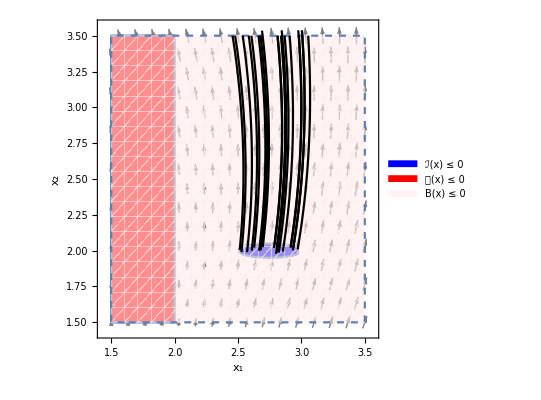

SDP CPU-time elapsed: 54.7977s

Total CPU-time elapsed: 56.7763s

```mathematica
main[varSetC13,flowVecC13,domainRangeC13,initialBoundaryC13,unsafeBoundaryC13,barrierDegreeC13,polyDegreesC13,paraRangeC13,LieOrderC13,ϵIC13,ϵUC13,ϵLC13,ϵC13,δC13,bilinearUnsafeConsC13,posteriorCheckC13,verboseC13];
```

### sys-bio1

```mathematica
varSetC9={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7]};
flowVecC9={-0.4 Subscript[x, 1]+ 5 Subscript[x, 3] Subscript[x, 4],0.4 Subscript[x, 1]-Subscript[x, 2],Subscript[x, 2]-5 Subscript[x, 3] Subscript[x, 4],5 Subscript[x, 5] Subscript[x, 6] - 5 Subscript[x, 3] Subscript[x, 4],-5 Subscript[x, 5] Subscript[x, 6] + 5 Subscript[x, 3] Subscript[x, 4],0.5 Subscript[x, 7]- 5 Subscript[x, 5] Subscript[x, 6],-0.5 Subscript[x, 7] + 5 Subscript[x, 5] Subscript[x, 6]};
domainRangeC9={-2,2};
initialBoundaryC9=(-1+Subscript[x, 1])^2+(-1+Subscript[x, 2])^2+(-1+Subscript[x, 3])^2+(-1+Subscript[x, 4])^2+(-1+Subscript[x, 5])^2+(-1+Subscript[x, 6])^2+(-1+Subscript[x, 7])^2- 0.01^2;
unsafeBoundaryC9=(-1.9+Subscript[x, 1])^2+(-1.9+Subscript[x, 2])^2+(-1.9+Subscript[x, 3])^2+(-1.9+Subscript[x, 4])^2+(-1.9+Subscript[x, 5])^2+(-1.9+Subscript[x, 6])^2+(-1.9+Subscript[x, 7])^2 - 0.1^2;
barrierDegreeC9=2;
polyDegreesC9={0,0,1};
paraRangeC9={-10,10};
LieOrderC9=1;
ϵIC9=ϵUC9=ϵLC9=N[10^-3];
ϵC9=N[10^-3];
δC9=-N[10^-3];
bilinearUnsafeConsC9=False;
posteriorCheckC9=False;
verboseC9=False;
```

```mathematica
main[varSetC9,flowVecC9,domainRangeC9,initialBoundaryC9,unsafeBoundaryC9,barrierDegreeC9,polyDegreesC9,paraRangeC9,LieOrderC9,ϵIC9,ϵUC9,ϵLC9,ϵC9,δC9,bilinearUnsafeConsC9,posteriorCheckC9,verboseC9];
```

Template BC: 
a_0000000+a_1000000 x_1+a_2000000 x_1^2+a_0100000 x_2+a_1100000 x_1 x_2+a_0200000 x_2^2+a_0010000 x_3+a_1010000 x_1 x_3+a_0110000 x_2 x_3+a_0020000 x_3^2+a_0001000 x_4+a_1001000 x_1 x_4+a_0101000 x_2 x_4+a_0011000 x_3 x_4+a_0002000 x_4^2+a_0000100 x_5+a_1000100 x_1 x_5+a_0100100 x_2 x_5+a_0010100 x_3 x_5+a_0001100 x_4 x_5+a_0000200 x_5^2+a_0000010 x_6+a_1000010 x_1 x_6+a_0100010 x_2 x_6+a_0010010 x_3 x_6+a_0001010 x_4 x_6+a_0000110 x_5 x_6+a_0000020 x_6^2+a_0000001 x_7+a_1000001 x_1 x_7+a_0100001 x_2 x_7+a_0010001 x_3 x_7+a_0001001 x_4 x_7+a_0000101 x_5 x_7+a_0000011 x_6 x_7+a_0000002 x_7^2

Lie sequence: 
{a_0000000+a_1000000 x_1+a_2000000 x_1^2+a_0100000 x_2+a_1100000 x_1 x_2+a_0200000 x_2^2+a_0010000 x_3+a_1010000 x_1 x_3+a_0110000 x_2 x_3+a_0020000 x_3^2+a_0001000 x_4+a_1001000 x_1 x_4+a_0101000 x_2 x_4+a_0011000 x_3 x_4+a_0002000 x_4^2+a_0000100 x_5+a_1000100 x_1 x_5+a_0100100 x_2 x_5+a_0010100 x_3 x_5+a_0001100 x_4 x_5+a_0000200 x_5^2+a_0000010 x_6+a_1000010 x_1 x_6+a_0100010 x_2 x_6+a_0010010 x_3 x_6+a_0001010 x_4 x_6+a_0000110 x_5 x_6+a_0000020 x_6^2+a_0000001 x_7+a_1000001 x_1 x_7+a_0100001 x_2 x_7+a_0010001 x_3 x_7+a_0001001 x_4 x_7+a_0000101 x_5 x_7+a_0000011 x_6 x_7+a_0000002 x_7^2,(0.4 a_1100000-0.8 a_2000000) x_1^2+(a_0110000-2 a_0200000) x_2^2+5 (a_0010100-a_0011000-2 a_0020000+a_1010000) x_3^2 x_4+5 (a_0000101-a_0000110-2 a_0000200+a_0001100) x_5^2 x_6+(-0.5 a_0000001+0.5 a_0000010) x_7+(-0.5 a_0000011+1. a_0000020) x_6 x_7+(-1. a_0000002+0.5 a_0000011) x_7^2+x_4 (5 (a_0001001-a_0001010-a_0001100+2 a_0002000) x_5 x_6+(-0.5 a_0001001+0.5 a_0001010) x_7)+x_2 (a_0010000-a_0100000+(a_0011000-a_0101000) x_4+x_3 (2 a_0020000-a_0110000+5 (a_0100100-a_0101000-a_0110000+a_1100000) x_4)+(a_0010010-a_0100010) x_6+x_5 (a_0010100-a_0100100+5 (a_0100001-a_0100010-a_0100100+a_0101000) x_6)+(a_0010001-1.5 a_0100001+0.5 a_0100010) x_7)+x_1 (0.4 a_0100000-0.4 a_1000000+(0.8 a_0200000+a_1010000-1.4 a_1100000) x_2+(0.4 a_0101000-0.4 a_1001000) x_4+x_3 (0.4 a_0110000-0.4 a_1010000+5 (a_1000100-a_1001000-a_1010000+2 a_2000000) x_4)+(0.4 a_0100010-0.4 a_1000010) x_6+x_5 (0.4 a_0100100-0.4 a_1000100+5 (a_1000001-a_1000010-a_1000100+a_1001000) x_6)+(0.4 a_0100001-0.9 a_1000001+0.5 a_1000010) x_7)+x_5 (5 (a_0000011-2 a_0000020-a_0000110+a_0001010) x_6^2+(-0.5 a_0000101+0.5 a_0000110) x_7+x_6 (5 (a_0000001-a_0000010-a_0000100+a_0001000)+5 (2 a_0000002-a_0000011-a_0000101+a_0001001) x_7))+x_3 (5 (a_0001100-2 a_0002000-a_0011000+a_1001000) x_4^2+5 (a_0010001-a_0010010-a_0010100+a_0011000) x_5 x_6+(-0.5 a_0010001+0.5 a_0010010) x_7+x_4 (5 (a_0000100-a_0001000-a_0010000+a_1000000)+5 (2 a_0000200-a_0001100-a_0010100+a_1000100) x_5+5 (a_0000110-a_0001010-a_0010010+a_1000010) x_6+5 (a_0000101-a_0001001-a_0010001+a_1000001) x_7))}

SOS constraints:
{w_0000000,u_0000000,-0.001-a_0000000+6.9999 w_0000000+(-a_2000000+w_0000000) x_1^2+(-a_0200000+w_0000000) x_2^2+(-a_0020000+w_0000000) x_3^2+(-a_0002000+w_0000000) x_4^2+(-a_0000200+w_0000000) x_5^2+(-a_0000020+w_0000000) x_6^2+(-a_0000001-2 w_0000000) x_7+(-a_0000002+w_0000000) x_7^2+x_6 (-a_0000010-2 w_0000000-a_0000011 x_7)+x_5 (-a_0000100-2 w_0000000-a_0000110 x_6-a_0000101 x_7)+x_4 (-a_0001000-2 w_0000000-a_0001100 x_5-a_0001010 x_6-a_0001001 x_7)+x_3 (-a_0010000-2 w_0000000-a_0011000 x_4-a_0010100 x_5-a_0010010 x_6-a_0010001 x_7)+x_2 (-a_0100000-2 w_0000000-a_0110000 x_3-a_0101000 x_4-a_0100100 x_5-a_0100010 x_6-a_0100001 x_7)+x_1 (-a_1000000-2 w_0000000-a_1100000 x_2-a_1010000 x_3-a_1001000 x_4-a_1000100 x_5-a_1000010 x_6-a_1000001 x_7),-0.001+a_0000000+25.26 u_0000000+(a_2000000+u_0000000) x_1^2+(a_0200000+u_0000000) x_2^2+(a_0020000+u_0000000) x_3^2+(a_0002000+u_0000000) x_4^2+(a_0000200+u_0000000) x_5^2+(a_0000020+u_0000000) x_6^2+(a_0000001-3.8 u_0000000) x_7+(a_0000002+u_0000000) x_7^2+x_6 (a_0000010-3.8 u_0000000+a_0000011 x_7)+x_5 (a_0000100-3.8 u_0000000+a_0000110 x_6+a_0000101 x_7)+x_4 (a_0001000-3.8 u_0000000+a_0001100 x_5+a_0001010 x_6+a_0001001 x_7)+x_3 (a_0010000-3.8 u_0000000+a_0011000 x_4+a_0010100 x_5+a_0010010 x_6+a_0010001 x_7)+x_2 (a_0100000-3.8 u_0000000+a_0110000 x_3+a_0101000 x_4+a_0100100 x_5+a_0100010 x_6+a_0100001 x_7)+x_1 (a_1000000-3.8 u_0000000+a_1100000 x_2+a_1010000 x_3+a_1001000 x_4+a_1000100 x_5+a_1000010 x_6+a_1000001 x_7),-0.001+a_0000000 v10_0000000+a_2000000 v10_1000000 x_1^3+a_0200000 v10_0100000 x_2^3+a_0020000 v10_0010000 x_3^3+a_0002000 v10_0001000 x_4^3+a_0000200 v10_0000100 x_5^3+a_0000020 v10_0000010 x_6^3+(-0.5 a_0000010+a_0000001 (0.5+v10_0000000)+a_0000000 v10_0000001) x_7+(-0.5 a_0000011+a_0000002 (1.+v10_0000000)+a_0000001 v10_0000001) x_7^2+a_0000002 v10_0000001 x_7^3+x_6^2 (a_0000020 v10_0000000+a_0000010 v10_0000010+(a_0000020 v10_0000001+a_0000011 v10_0000010) x_7)+x_5^2 (a_0000200 v10_0000000+a_0000100 v10_0000100+(-5 a_0000101+10 a_0000200-5 a_0001100+a_0000200 v10_0000010+a_0000110 (5+v10_0000100)) x_6+(a_0000200 v10_0000001+a_0000101 v10_0000100) x_7)+x_4^2 (a_0002000 v10_0000000+a_0001000 v10_0001000+(a_0002000 v10_0000100+a_0001100 v10_0001000) x_5+(a_0002000 v10_0000010+a_0001010 v10_0001000) x_6+(a_0002000 v10_0000001+a_0001001 v10_0001000) x_7)+x_3^2 (a_0020000 v10_0000000+a_0010000 v10_0010000+(-5 a_0010100+10 a_0020000-5 a_1010000+a_0020000 v10_0001000+a_0011000 (5+v10_0010000)) x_4+(a_0020000 v10_0000100+a_0010100 v10_0010000) x_5+(a_0020000 v10_0000010+a_0010010 v10_0010000) x_6+(a_0020000 v10_0000001+a_0010001 v10_0010000) x_7)+x_2^2 (-a_0110000+a_0200000 (2+v10_0000000)+a_0100000 v10_0100000+(a_0200000 v10_0010000+a_0110000 v10_0100000) x_3+(a_0200000 v10_0001000+a_0101000 v10_0100000) x_4+(a_0200000 v10_0000100+a_0100100 v10_0100000) x_5+(a_0200000 v10_0000010+a_0100010 v10_0100000) x_6+(a_0200000 v10_0000001+a_0100001 v10_0100000) x_7)+x_1^2 (-0.4 a_1100000+a_2000000 (0.8+v10_0000000)+a_1000000 v10_1000000+(a_2000000 v10_0100000+a_1100000 v10_1000000) x_2+(a_2000000 v10_0010000+a_1010000 v10_1000000) x_3+(a_2000000 v10_0001000+a_1001000 v10_1000000) x_4+(a_2000000 v10_0000100+a_1000100 v10_1000000) x_5+(a_2000000 v10_0000010+a_1000010 v10_1000000) x_6+(a_2000000 v10_0000001+a_1000001 v10_1000000) x_7)+x_6 (a_0000010 v10_0000000+a_0000000 v10_0000010+(-1. a_0000020+a_0000011 (0.5+v10_0000000)+a_0000010 v10_0000001+a_0000001 v10_0000010) x_7+(a_0000011 v10_0000001+a_0000002 v10_0000010) x_7^2)+x_5 (a_0000100 v10_0000000+a_0000000 v10_0000100+(-5 a_0000011+5 a_0000110-5 a_0001010+a_0000110 v10_0000010+a_0000020 (10+v10_0000100)) x_6^2+(-0.5 a_0000110+a_0000101 (0.5+v10_0000000)+a_0000100 v10_0000001+a_0000001 v10_0000100) x_7+(a_0000101 v10_0000001+a_0000002 v10_0000100) x_7^2+x_6 (-5 a_0000001+5 a_0000100-5 a_0001000+a_0000110 v10_0000000+a_0000100 v10_0000010+a_0000010 (5+v10_0000100)+(-10 a_0000002+5 a_0000101-5 a_0001001+a_0000110 v10_0000001+a_0000101 v10_0000010+a_0000011 (5+v10_0000100)) x_7))+x_4 (a_0001000 v10_0000000+a_0000000 v10_0001000+(a_0001100 v10_0000100+a_0000200 v10_0001000) x_5^2+(a_0001010 v10_0000010+a_0000020 v10_0001000) x_6^2+(-0.5 a_0001010+a_0001001 (0.5+v10_0000000)+a_0001000 v10_0000001+a_0000001 v10_0001000) x_7+(a_0001001 v10_0000001+a_0000002 v10_0001000) x_7^2+x_6 (a_0001010 v10_0000000+a_0001000 v10_0000010+a_0000010 v10_0001000+(a_0001010 v10_0000001+a_0001001 v10_0000010+a_0000011 v10_0001000) x_7)+x_5 (a_0001100 v10_0000000+a_0001000 v10_0000100+a_0000100 v10_0001000+(-5 a_0001001+5 a_0001100-10 a_0002000+a_0001100 v10_0000010+a_0001010 (5+v10_0000100)+a_0000110 v10_0001000) x_6+(a_0001100 v10_0000001+a_0001001 v10_0000100+a_0000101 v10_0001000) x_7))+x_3 (a_0010000 v10_0000000+a_0000000 v10_0010000+(-5 a_0001100+5 a_0011000-5 a_1001000+a_0011000 v10_0001000+a_0002000 (10+v10_0010000)) x_4^2+(a_0010100 v10_0000100+a_0000200 v10_0010000) x_5^2+(a_0010010 v10_0000010+a_0000020 v10_0010000) x_6^2+(-0.5 a_0010010+a_0010001 (0.5+v10_0000000)+a_0010000 v10_0000001+a_0000001 v10_0010000) x_7+(a_0010001 v10_0000001+a_0000002 v10_0010000) x_7^2+x_6 (a_0010010 v10_0000000+a_0010000 v10_0000010+a_0000010 v10_0010000+(a_0010010 v10_0000001+a_0010001 v10_0000010+a_0000011 v10_0010000) x_7)+x_5 (a_0010100 v10_0000000+a_0010000 v10_0000100+a_0000100 v10_0010000+(-5 a_0010001+5 a_0010100-5 a_0011000+a_0010100 v10_0000010+a_0010010 (5+v10_0000100)+a_0000110 v10_0010000) x_6+(a_0010100 v10_0000001+a_0010001 v10_0000100+a_0000101 v10_0010000) x_7)+x_4 (-5 a_0000100+5 a_0010000-5 a_1000000+a_0011000 v10_0000000+a_0010000 v10_0001000+a_0001000 (5+v10_0010000)+(-10 a_0000200+5 a_0010100-5 a_1000100+a_0011000 v10_0000100+a_0010100 v10_0001000+a_0001100 (5+v10_0010000)) x_5+(-5 a_0000110+5 a_0010010-5 a_1000010+a_0011000 v10_0000010+a_0010010 v10_0001000+a_0001010 (5+v10_0010000)) x_6+(-5 a_0000101+5 a_0010001-5 a_1000001+a_0011000 v10_0000001+a_0010001 v10_0001000+a_0001001 (5+v10_0010000)) x_7))+x_2 (-a_0010000+a_0100000 (1+v10_0000000)+a_0000000 v10_0100000+(a_0110000 v10_0010000+a_0020000 v10_0100000) x_3^2+(a_0101000 v10_0001000+a_0002000 v10_0100000) x_4^2+(a_0100100 v10_0000100+a_0000200 v10_0100000) x_5^2+(a_0100010 v10_0000010+a_0000020 v10_0100000) x_6^2+(-a_0010001-0.5 a_0100010+a_0100001 (1.5+v10_0000000)+a_0100000 v10_0000001+a_0000001 v10_0100000) x_7+(a_0100001 v10_0000001+a_0000002 v10_0100000) x_7^2+x_6 (-a_0010010+a_0100010 (1+v10_0000000)+a_0100000 v10_0000010+a_0000010 v10_0100000+(a_0100010 v10_0000001+a_0100001 v10_0000010+a_0000011 v10_0100000) x_7)+x_5 (-a_0010100+a_0100100 (1+v10_0000000)+a_0100000 v10_0000100+a_0000100 v10_0100000+(-5 a_0100001+5 a_0100100-5 a_0101000+a_0100100 v10_0000010+a_0100010 (5+v10_0000100)+a_0000110 v10_0100000) x_6+(a_0100100 v10_0000001+a_0100001 v10_0000100+a_0000101 v10_0100000) x_7)+x_4 (-a_0011000+a_0101000 (1+v10_0000000)+a_0100000 v10_0001000+a_0001000 v10_0100000+(a_0101000 v10_0000100+a_0100100 v10_0001000+a_0001100 v10_0100000) x_5+(a_0101000 v10_0000010+a_0100010 v10_0001000+a_0001010 v10_0100000) x_6+(a_0101000 v10_0000001+a_0100001 v10_0001000+a_0001001 v10_0100000) x_7)+x_3 (-2 a_0020000+a_0110000 (1+v10_0000000)+a_0100000 v10_0010000+a_0010000 v10_0100000+(-5 a_0100100+5 a_0110000-5 a_1100000+a_0110000 v10_0001000+a_0101000 (5+v10_0010000)+a_0011000 v10_0100000) x_4+(a_0110000 v10_0000100+a_0100100 v10_0010000+a_0010100 v10_0100000) x_5+(a_0110000 v10_0000010+a_0100010 v10_0010000+a_0010010 v10_0100000) x_6+(a_0110000 v10_0000001+a_0100001 v10_0010000+a_0010001 v10_0100000) x_7))+x_1 (-0.4 a_0100000+a_1000000 (0.4+v10_0000000)+a_0000000 v10_1000000+(a_1100000 v10_0100000+a_0200000 v10_1000000) x_2^2+(a_1010000 v10_0010000+a_0020000 v10_1000000) x_3^2+(a_1001000 v10_0001000+a_0002000 v10_1000000) x_4^2+(a_1000100 v10_0000100+a_0000200 v10_1000000) x_5^2+(a_1000010 v10_0000010+a_0000020 v10_1000000) x_6^2+(-0.4 a_0100001-0.5 a_1000010+a_1000001 (0.9+v10_0000000)+a_1000000 v10_0000001+a_0000001 v10_1000000) x_7+(a_1000001 v10_0000001+a_0000002 v10_1000000) x_7^2+x_6 (-0.4 a_0100010+a_1000010 (0.4+v10_0000000)+a_1000000 v10_0000010+a_0000010 v10_1000000+(a_1000010 v10_0000001+a_1000001 v10_0000010+a_0000011 v10_1000000) x_7)+x_5 (-0.4 a_0100100+a_1000100 (0.4+v10_0000000)+a_1000000 v10_0000100+a_0000100 v10_1000000+(-5 a_1000001+5 a_1000100-5 a_1001000+a_1000100 v10_0000010+a_1000010 (5+v10_0000100)+a_0000110 v10_1000000) x_6+(a_1000100 v10_0000001+a_1000001 v10_0000100+a_0000101 v10_1000000) x_7)+x_4 (-0.4 a_0101000+a_1001000 (0.4+v10_0000000)+a_1000000 v10_0001000+a_0001000 v10_1000000+(a_1001000 v10_0000100+a_1000100 v10_0001000+a_0001100 v10_1000000) x_5+(a_1001000 v10_0000010+a_1000010 v10_0001000+a_0001010 v10_1000000) x_6+(a_1001000 v10_0000001+a_1000001 v10_0001000+a_0001001 v10_1000000) x_7)+x_3 (-0.4 a_0110000+a_1010000 (0.4+v10_0000000)+a_1000000 v10_0010000+a_0010000 v10_1000000+(-5 a_1000100+5 a_1010000-10 a_2000000+a_1010000 v10_0001000+a_1001000 (5+v10_0010000)+a_0011000 v10_1000000) x_4+(a_1010000 v10_0000100+a_1000100 v10_0010000+a_0010100 v10_1000000) x_5+(a_1010000 v10_0000010+a_1000010 v10_0010000+a_0010010 v10_1000000) x_6+(a_1010000 v10_0000001+a_1000001 v10_0010000+a_0010001 v10_1000000) x_7)+x_2 (-0.8 a_0200000-a_1010000+1.4 a_1100000+a_1100000 v10_0000000+a_1000000 v10_0100000+a_0100000 v10_1000000+(a_1100000 v10_0010000+a_1010000 v10_0100000+a_0110000 v10_1000000) x_3+(a_1100000 v10_0001000+a_1001000 v10_0100000+a_0101000 v10_1000000) x_4+(a_1100000 v10_0000100+a_1000100 v10_0100000+a_0100100 v10_1000000) x_5+(a_1100000 v10_0000010+a_1000010 v10_0100000+a_0100010 v10_1000000) x_6+(a_1100000 v10_0000001+a_1000001 v10_0100000+a_0100001 v10_1000000) x_7))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<12468>, {1656, 1656}]}

LMI variables:
{a_0000000,a_0000001,a_0000002,a_0000010,a_0000011,a_0000020,a_0000100,a_0000101,a_0000110,a_0000200,a_0001000,a_0001001,a_0001010,a_0001100,a_0002000,a_0010000,a_0010001,a_0010010,a_0010100,a_0011000,a_0020000,a_0100000,a_0100001,a_0100010,a_0100100,a_0101000,a_0110000,a_0200000,a_1000000,a_1000001,a_1000010,a_1000100,a_1001000,a_1010000,a_1100000,a_2000000,λ,w_0000000,u_0000000,v10_0000000,v10_0000001,v10_0000010,v10_0000100,v10_0001000,v10_0010000,v10_0100000,v10_1000000}

Variable correspondence:
{a_0000000→z_1,a_0000001→z_2,a_0000002→z_3,a_0000010→z_4,a_0000011→z_5,a_0000020→z_6,a_0000100→z_7,a_0000101→z_8,a_0000110→z_9,a_0000200→z_10,a_0001000→z_11,a_0001001→z_12,a_0001010→z_13,a_0001100→z_14,a_0002000→z_15,a_0010000→z_16,a_0010001→z_17,a_0010010→z_18,a_0010100→z_19,a_0011000→z_20,a_0020000→z_21,a_0100000→z_22,a_0100001→z_23,a_0100010→z_24,a_0100100→z_25,a_0101000→z_26,a_0110000→z_27,a_0200000→z_28,a_1000000→z_29,a_1000001→z_30,a_1000010→z_31,a_1000100→z_32,a_1001000→z_33,a_1010000→z_34,a_1100000→z_35,a_2000000→z_36,λ→z_37,w_0000000→z_38,u_0000000→z_39,v10_0000000→z_40,v10_0000001→z_41,v10_0000010→z_42,v10_0000100→z_43,v10_0001000→z_44,v10_0010000→z_45,v10_0100000→z_46,v10_1000000→z_47}

Initial vector:
{a_0000000,a_0000001,a_0000002,a_0000010,a_0000011,a_0000020,a_0000100,a_0000101,a_0000110,a_0000200,a_0001000,a_0001001,a_0001010,a_0001100,a_0002000,a_0010000,a_0010001,a_0010010,a_0010100,a_0011000,a_0020000,a_0100000,a_0100001,a_0100010,a_0100100,a_0101000,a_0110000,a_0200000,a_1000000,a_1000001,a_1000010,a_1000100,a_1001000,a_1010000,a_1100000,a_2000000,λ,1,1,-1,0,0,0,0,0,0,0}

Initial feasible solution:
z^0={z_1→-6.45154,z_2→0.97323,z_3→-0.240078,z_4→0.973239,z_5→-0.480045,z_6→-0.240246,z_7→0.923761,z_8→0.0962086,z_9→0.0967271,z_10→-0.235662,z_11→0.923696,z_12→0.0963196,z_13→0.0962492,z_14→-0.470801,z_15→-0.235437,z_16→0.999832,z_17→0.0851783,z_18→0.0851891,z_19→0.0875362,z_20→0.0875214,z_21→-0.145267,z_22→0.999773,z_23→0.0854898,z_24→0.0857735,z_25→0.0878317,z_26→0.0881054,z_27→-0.291102,z_28→-0.144257,z_29→0.999816,z_30→0.0853013,z_31→0.084662,z_32→0.0880428,z_33→0.0874418,z_34→-0.290577,z_35→-0.290857,z_36→-0.145592,z_37→-0.00014816,z_38→1,z_39→1,z_40→-1,z_41→0,z_42→0,z_43→0,z_44→0,z_45→0,z_46→0,z_47→0}

Initial maximum:
λ^0=-0.00014816

LMI variables:
{a_0000000,a_0000001,a_0000002,a_0000010,a_0000011,a_0000020,a_0000100,a_0000101,a_0000110,a_0000200,a_0001000,a_0001001,a_0001010,a_0001100,a_0002000,a_0010000,a_0010001,a_0010010,a_0010100,a_0011000,a_0020000,a_0100000,a_0100001,a_0100010,a_0100100,a_0101000,a_0110000,a_0200000,a_1000000,a_1000001,a_1000010,a_1000100,a_1001000,a_1010000,a_1100000,a_2000000,λ,w_0000000,u_0000000,v10_0000000,v10_0000001,v10_0000010,v10_0000100,v10_0001000,v10_0010000,v10_0100000,v10_1000000,ζ}

Variable correspondence:
{a_0000000→z_1,a_0000001→z_2,a_0000002→z_3,a_0000010→z_4,a_0000011→z_5,a_0000020→z_6,a_0000100→z_7,a_0000101→z_8,a_0000110→z_9,a_0000200→z_10,a_0001000→z_11,a_0001001→z_12,a_0001010→z_13,a_0001100→z_14,a_0002000→z_15,a_0010000→z_16,a_0010001→z_17,a_0010010→z_18,a_0010100→z_19,a_0011000→z_20,a_0020000→z_21,a_0100000→z_22,a_0100001→z_23,a_0100010→z_24,a_0100100→z_25,a_0101000→z_26,a_0110000→z_27,a_0200000→z_28,a_1000000→z_29,a_1000001→z_30,a_1000010→z_31,a_1000100→z_32,a_1001000→z_33,a_1010000→z_34,a_1100000→z_35,a_2000000→z_36,λ→z_37,w_0000000→z_38,u_0000000→z_39,v10_0000000→z_40,v10_0000001→z_41,v10_0000010→z_42,v10_0000100→z_43,v10_0001000→z_44,v10_0010000→z_45,v10_0100000→z_46,v10_1000000→z_47,ζ→zz}

Feasible solution:
z^1={z_1→-6.45157,z_2→0.973143,z_3→-0.240043,z_4→0.973161,z_5→-0.479979,z_6→-0.240084,z_7→0.923716,z_8→0.0961937,z_9→0.0965474,z_10→-0.23557,z_11→0.923722,z_12→0.0962888,z_13→0.0963497,z_14→-0.470782,z_15→-0.235357,z_16→0.99986,z_17→0.0851117,z_18→0.085175,z_19→0.0875494,z_20→0.0876106,z_21→-0.145356,z_22→0.999752,z_23→0.0856141,z_24→0.0855672,z_25→0.0879971,z_26→0.0879478,z_27→-0.290596,z_28→-0.144717,z_29→0.999845,z_30→0.0851644,z_31→0.0849328,z_32→0.0879565,z_33→0.0877224,z_34→-0.29066,z_35→-0.290661,z_36→-0.14545,z_37→-0.000035917,z_38→1.,z_39→0.969318,z_40→-1.00003,z_41→0.0000688654,z_42→-8.97758×10^-6,z_43→0.000137352,z_44→0.0000625627,z_45→-0.0000153261,z_46→0.0000802919,z_47→0.000225943,zz→-4.71218×10^-7}

Maximum:
(λ+ζ)^1=-0.0000363883

|z^1-z^0|=0.0306991

Feasible solution:
z^2={z_1→-6.45158,z_2→0.973126,z_3→-0.239971,z_4→0.973126,z_5→-0.479788,z_6→-0.239964,z_7→0.923753,z_8→0.0960949,z_9→0.0964359,z_10→-0.235526,z_11→0.923741,z_12→0.096236,z_13→0.0962874,z_14→-0.470707,z_15→-0.235324,z_16→0.999917,z_17→0.0850109,z_18→0.0850528,z_19→0.0875728,z_20→0.0876126,z_21→-0.145324,z_22→0.999757,z_23→0.0855547,z_24→0.0854852,z_25→0.0879817,z_26→0.0879097,z_27→-0.290521,z_28→-0.144676,z_29→0.999883,z_30→0.0851374,z_31→0.0848875,z_32→0.0879396,z_33→0.0876873,z_34→-0.290617,z_35→-0.290608,z_36→-0.145438,z_37→-0.0000358524,z_38→1.,z_39→0.969334,z_40→-1.00001,z_41→0.0000688713,z_42→-8.7471×10^-6,z_43→0.000137199,z_44→0.0000626804,z_45→-0.0000151548,z_46→0.0000803219,z_47→0.000226384,zz→-4.70913×10^-7}

Maximum:
(λ+ζ)^2=-0.0000363233

|z^2-z^1|=0.000397243

Close enough solutions: 0.000397243 ≤ ϵ = 0.001

Barrier certificate candidate:
-6.45158+0.999883 x_1-0.145438 x_1^2+0.999757 x_2-0.290608 x_1 x_2-0.144676 x_2^2+0.999917 x_3-0.290617 x_1 x_3-0.290521 x_2 x_3-0.145324 x_3^2+0.923741 x_4+0.0876873 x_1 x_4+0.0879097 x_2 x_4+0.0876126 x_3 x_4-0.235324 x_4^2+0.923753 x_5+0.0879396 x_1 x_5+0.0879817 x_2 x_5+0.0875728 x_3 x_5-0.470707 x_4 x_5-0.235526 x_5^2+0.973126 x_6+0.0848875 x_1 x_6+0.0854852 x_2 x_6+0.0850528 x_3 x_6+0.0962874 x_4 x_6+0.0964359 x_5 x_6-0.239964 x_6^2+0.973126 x_7+0.0851374 x_1 x_7+0.0855547 x_2 x_7+0.0850109 x_3 x_7+0.096236 x_4 x_7+0.0960949 x_5 x_7-0.479788 x_6 x_7-0.239971 x_7^2

SDP CPU-time elapsed: 73.4487s

Total CPU-time elapsed: 113.875s

### sys-bio2

```mathematica
varSetC10={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9]};
flowVecC10={3 Subscript[x, 3] - Subscript[x, 1] Subscript[x, 6],Subscript[x, 4] - Subscript[x, 2] Subscript[x, 6],Subscript[x, 1] Subscript[x, 6] - 3 Subscript[x, 3],Subscript[x, 2] Subscript[x, 6] - Subscript[x, 4],3 Subscript[x, 3] + 5 Subscript[x, 1] - Subscript[x, 5],5 Subscript[x, 5] + 3 Subscript[x, 3]+ Subscript[x, 4] - Subscript[x, 6](Subscript[x, 1]+Subscript[x, 2]+2 Subscript[x, 8] + 1),5 Subscript[x, 4] + Subscript[x, 2]- 0.5 Subscript[x, 7],5 Subscript[x, 7] - 2 Subscript[x, 6] Subscript[x, 8] + Subscript[x, 9] - 0.2 Subscript[x, 8],2 Subscript[x, 6] Subscript[x, 8] - Subscript[x, 9]};
domainRangeC10={-2,2};
initialBoundaryC10=(-1+Subscript[x, 1])^2+(-1+Subscript[x, 2])^2+(-1+Subscript[x, 3])^2+(-1+Subscript[x, 4])^2+(-1+Subscript[x, 5])^2+(-1+Subscript[x, 6])^2+(-1+Subscript[x, 7])^2+(-1+Subscript[x, 8])^2+(-1+Subscript[x, 9])^2- 0.01^2;
unsafeBoundaryC10=(-1.9+Subscript[x, 1])^2+(-1.9+Subscript[x, 2])^2+(-1.9+Subscript[x, 3])^2+(-1.9+Subscript[x, 4])^2+(-1.9+Subscript[x, 5])^2+(-1.9+Subscript[x, 6])^2+(-1.9+Subscript[x, 7])^2 +(-1.9+Subscript[x, 8])^2+(-1.9+Subscript[x, 9])^2- 0.1^2;
barrierDegreeC10=1;
polyDegreesC10={0,0,1};
paraRangeC10={-10,10};
LieOrderC10=1;
ϵIC10=ϵUC10=ϵLC10=N[10^-3];
ϵC10=N[10^-1];
δC10=-N[10^-3];
bilinearUnsafeConsC10=False;
posteriorCheckC10=False;
verboseC10=False;
```

```mathematica
main[varSetC10,flowVecC10,domainRangeC10,initialBoundaryC10,unsafeBoundaryC10,barrierDegreeC10,polyDegreesC10,paraRangeC10,LieOrderC10,ϵIC10,ϵUC10,ϵLC10,ϵC10,δC10,bilinearUnsafeConsC10,posteriorCheckC10,verboseC10];
```

Template BC: 
a_000000000+a_100000000 x_1+a_010000000 x_2+a_001000000 x_3+a_000100000 x_4+a_000010000 x_5+a_000001000 x_6+a_000000100 x_7+a_000000010 x_8+a_000000001 x_9

Lie sequence: 
{a_000000000+a_100000000 x_1+a_010000000 x_2+a_001000000 x_3+a_000100000 x_4+a_000010000 x_5+a_000001000 x_6+a_000000100 x_7+a_000000010 x_8+a_000000001 x_9,3 (a_000001000+a_000010000-a_001000000+a_100000000) x_3+(5 a_000000100+a_000001000-a_000100000+a_010000000) x_4+(5 a_000001000-a_000010000) x_5+x_2 (a_000000100+(-a_000001000+a_000100000-a_010000000) x_6)+x_1 (5 a_000010000+(-a_000001000+a_001000000-a_100000000) x_6)+(5 a_000000010-0.5 a_000000100) x_7-0.2 a_000000010 x_8+x_6 (-a_000001000+2 (a_000000001-a_000000010-a_000001000) x_8)+(-a_000000001+a_000000010) x_9}

SOS constraints:
{w_000000000,u_000000000,-0.001-a_000000000+8.9999 w_000000000+(-a_100000000-2 w_000000000) x_1+w_000000000 x_1^2+(-a_010000000-2 w_000000000) x_2+w_000000000 x_2^2+(-a_001000000-2 w_000000000) x_3+w_000000000 x_3^2+(-a_000100000-2 w_000000000) x_4+w_000000000 x_4^2+(-a_000010000-2 w_000000000) x_5+w_000000000 x_5^2+(-a_000001000-2 w_000000000) x_6+w_000000000 x_6^2+(-a_000000100-2 w_000000000) x_7+w_000000000 x_7^2+(-a_000000010-2 w_000000000) x_8+w_000000000 x_8^2+(-a_000000001-2 w_000000000) x_9+w_000000000 x_9^2,-0.001+a_000000000+32.48 u_000000000+(a_100000000-3.8 u_000000000) x_1+u_000000000 x_1^2+(a_010000000-3.8 u_000000000) x_2+u_000000000 x_2^2+(a_001000000-3.8 u_000000000) x_3+u_000000000 x_3^2+(a_000100000-3.8 u_000000000) x_4+u_000000000 x_4^2+(a_000010000-3.8 u_000000000) x_5+u_000000000 x_5^2+(a_000001000-3.8 u_000000000) x_6+u_000000000 x_6^2+(a_000000100-3.8 u_000000000) x_7+u_000000000 x_7^2+(a_000000010-3.8 u_000000000) x_8+u_000000000 x_8^2+(a_000000001-3.8 u_000000000) x_9+u_000000000 x_9^2,-0.001+a_000000000 v10_000000000+a_100000000 v10_100000000 x_1^2+a_010000000 v10_010000000 x_2^2+a_001000000 v10_001000000 x_3^2+a_000100000 v10_000100000 x_4^2+a_000010000 v10_000010000 x_5^2+a_000001000 v10_000001000 x_6^2+a_000000100 v10_000000100 x_7^2+a_000000010 v10_000000010 x_8^2+(-a_000000010+a_000000001 (1+v10_000000000)+a_000000000 v10_000000001) x_9+a_000000001 v10_000000001 x_9^2+x_8 (a_000000010 (0.2+v10_000000000)+a_000000000 v10_000000010+(a_000000010 v10_000000001+a_000000001 v10_000000010) x_9)+x_7 (-5 a_000000010+a_000000100 (0.5+v10_000000000)+a_000000000 v10_000000100+(a_000000100 v10_000000010+a_000000010 v10_000000100) x_8+(a_000000100 v10_000000001+a_000000001 v10_000000100) x_9)+x_6 (a_000001000 (1+v10_000000000)+a_000000000 v10_000001000+(a_000001000 v10_000000100+a_000000100 v10_000001000) x_7+(-2 a_000000001+a_000001000 (2+v10_000000010)+a_000000010 (2+v10_000001000)) x_8+(a_000001000 v10_000000001+a_000000001 v10_000001000) x_9)+x_5 (-5 a_000001000+a_000010000 (1+v10_000000000)+a_000000000 v10_000010000+(a_000010000 v10_000001000+a_000001000 v10_000010000) x_6+(a_000010000 v10_000000100+a_000000100 v10_000010000) x_7+(a_000010000 v10_000000010+a_000000010 v10_000010000) x_8+(a_000010000 v10_000000001+a_000000001 v10_000010000) x_9)+x_4 (-5 a_000000100-a_000001000+a_000100000-a_010000000+a_000100000 v10_000000000+a_000000000 v10_000100000+(a_000100000 v10_000010000+a_000010000 v10_000100000) x_5+(a_000100000 v10_000001000+a_000001000 v10_000100000) x_6+(a_000100000 v10_000000100+a_000000100 v10_000100000) x_7+(a_000100000 v10_000000010+a_000000010 v10_000100000) x_8+(a_000100000 v10_000000001+a_000000001 v10_000100000) x_9)+x_3 (-3 (a_000001000+a_000010000-a_001000000+a_100000000)+a_001000000 v10_000000000+a_000000000 v10_001000000+(a_001000000 v10_000100000+a_000100000 v10_001000000) x_4+(a_001000000 v10_000010000+a_000010000 v10_001000000) x_5+(a_001000000 v10_000001000+a_000001000 v10_001000000) x_6+(a_001000000 v10_000000100+a_000000100 v10_001000000) x_7+(a_001000000 v10_000000010+a_000000010 v10_001000000) x_8+(a_001000000 v10_000000001+a_000000001 v10_001000000) x_9)+x_2 (-a_000000100+a_010000000 v10_000000000+a_000000000 v10_010000000+(a_010000000 v10_001000000+a_001000000 v10_010000000) x_3+(a_010000000 v10_000100000+a_000100000 v10_010000000) x_4+(a_010000000 v10_000010000+a_000010000 v10_010000000) x_5+(-a_000100000+a_010000000 (1+v10_000001000)+a_000001000 (1+v10_010000000)) x_6+(a_010000000 v10_000000100+a_000000100 v10_010000000) x_7+(a_010000000 v10_000000010+a_000000010 v10_010000000) x_8+(a_010000000 v10_000000001+a_000000001 v10_010000000) x_9)+x_1 (-5 a_000010000+a_100000000 v10_000000000+a_000000000 v10_100000000+(a_100000000 v10_010000000+a_010000000 v10_100000000) x_2+(a_100000000 v10_001000000+a_001000000 v10_100000000) x_3+(a_100000000 v10_000100000+a_000100000 v10_100000000) x_4+(a_100000000 v10_000010000+a_000010000 v10_100000000) x_5+(-a_001000000+a_100000000 (1+v10_000001000)+a_000001000 (1+v10_100000000)) x_6+(a_100000000 v10_000000100+a_000000100 v10_100000000) x_7+(a_100000000 v10_000000010+a_000000010 v10_100000000) x_8+(a_100000000 v10_000000001+a_000000001 v10_100000000) x_9)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<1430>, {220, 220}]}

LMI variables:
{a_000000000,a_000000001,a_000000010,a_000000100,a_000001000,a_000010000,a_000100000,a_001000000,a_010000000,a_100000000,λ,w_000000000,u_000000000,v10_000000000,v10_000000001,v10_000000010,v10_000000100,v10_000001000,v10_000010000,v10_000100000,v10_001000000,v10_010000000,v10_100000000}

Variable correspondence:
{a_000000000→z_1,a_000000001→z_2,a_000000010→z_3,a_000000100→z_4,a_000001000→z_5,a_000010000→z_6,a_000100000→z_7,a_001000000→z_8,a_010000000→z_9,a_100000000→z_10,λ→z_11,w_000000000→z_12,u_000000000→z_13,v10_000000000→z_14,v10_000000001→z_15,v10_000000010→z_16,v10_000000100→z_17,v10_000001000→z_18,v10_000010000→z_19,v10_000100000→z_20,v10_001000000→z_21,v10_010000000→z_22,v10_100000000→z_23}

Initial vector:
{a_000000000,a_000000001,a_000000010,a_000000100,a_000001000,a_000010000,a_000100000,a_001000000,a_010000000,a_100000000,λ,1,1,-1,0,0,0,0,0,0,0,0,0}

Initial feasible solution:
z^0={z_1→-0.01068,z_2→0.0000451641,z_3→0.0000422689,z_4→-0.000214922,z_5→-2.2892×10^-6,z_6→-0.00103491,z_7→0.00106697,z_8→0.00472512,z_9→0.000991932,z_10→0.00461868,z_11→-0.0000669096,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0,z_18→0,z_19→0,z_20→0,z_21→0,z_22→0,z_23→0}

Initial maximum:
λ^0=-0.0000669096

LMI variables:
{a_000000000,a_000000001,a_000000010,a_000000100,a_000001000,a_000010000,a_000100000,a_001000000,a_010000000,a_100000000,λ,w_000000000,u_000000000,v10_000000000,v10_000000001,v10_000000010,v10_000000100,v10_000001000,v10_000010000,v10_000100000,v10_001000000,v10_010000000,v10_100000000,ζ}

Variable correspondence:
{a_000000000→z_1,a_000000001→z_2,a_000000010→z_3,a_000000100→z_4,a_000001000→z_5,a_000010000→z_6,a_000100000→z_7,a_001000000→z_8,a_010000000→z_9,a_100000000→z_10,λ→z_11,w_000000000→z_12,u_000000000→z_13,v10_000000000→z_14,v10_000000001→z_15,v10_000000010→z_16,v10_000000100→z_17,v10_000001000→z_18,v10_000010000→z_19,v10_000100000→z_20,v10_001000000→z_21,v10_010000000→z_22,v10_100000000→z_23,ζ→zz}

Feasible solution:
z^1={z_1→-0.0103084,z_2→0.0000363127,z_3→0.0000384059,z_4→-0.00020201,z_5→-6.83839×10^-6,z_6→-0.000964259,z_7→0.00103113,z_8→0.00451648,z_9→0.000960679,z_10→0.00441822,z_11→-0.0000629773,z_12→0.999922,z_13→0.946159,z_14→-0.99982,z_15→0.0000515547,z_16→0.000107307,z_17→0.000136041,z_18→0.000907817,z_19→-2.1266×10^-6,z_20→-0.000125848,z_21→0.00160928,z_22→0.00155141,z_23→-0.0000303101,zz→-1.45251×10^-6}

Maximum:
(λ+ζ)^1=-0.0000644298

|z^1-z^0|=0.0538982

Close enough solutions: 0.0538982 ≤ ϵ = 0.1

Barrier certificate candidate:
-0.0103084+0.00441822 x_1+0.000960679 x_2+0.00451648 x_3+0.00103113 x_4-0.000964259 x_5-6.83839×10^-6 x_6-0.00020201 x_7+0.0000384059 x_8+0.0000363127 x_9

SDP CPU-time elapsed: 0.953018s

Total CPU-time elapsed: 1.90322s

### quadcopter

```mathematica
varSetC11={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9], Subscript[x, 10],Subscript[x, 11], Subscript[x, 12]};
flowVecC11={Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],-7253.4927 Subscript[x, 1] + 1936.3639 Subscript[x, 11] - 1338.7624 Subscript[x, 4] + 1333.3333 Subscript[x, 8],-1936.3639 Subscript[x, 10] - 7253.4927 Subscript[x, 2] - 1338.7624 Subscript[x, 5] - 1333.3333 Subscript[x, 7],-769.2308 Subscript[x, 3] - 770.2301 Subscript[x, 6],Subscript[x, 10],Subscript[x, 11],Subscript[x, 12],9.81 Subscript[x, 2],-9.81 Subscript[x, 1],-16.3541 Subscript[x, 12] - 15.3846 Subscript[x, 9]};
domainRangeC11={-2,2};
initialBoundaryC11 = Subscript[x, 1]^2 + Subscript[x, 2]^2 + Subscript[x, 3]^2 + Subscript[x, 4]^2 + Subscript[x, 5]^2 + Subscript[x, 6]^2 + Subscript[x, 7]^2 + Subscript[x, 8]^2 + Subscript[x, 9]^2 + Subscript[x, 10]^2 + Subscript[x, 11]^2 + Subscript[x, 12]^2 - 0.1^2;
unsafeBoundaryC11=(2 Subscript[x, 1]- 0.5)^2 + (2 Subscript[x, 2] - 0.5)^2 + (2 Subscript[x, 3] - 0.5)^2 + (Subscript[x, 4] - 1)^2 + (Subscript[x, 5] - 1)^2 + (Subscript[x, 6] - 1)^2 + (Subscript[x, 7] - 1)^2 + (Subscript[x, 8] + 1)^2 + (Subscript[x, 9] - 1)^2 + (Subscript[x, 10] - 1)^2 + (Subscript[x, 11] + 1)^2 + (Subscript[x, 12] - 1)^2 - 0.5^2;
barrierDegreeC11=1;
polyDegreesC11={0,0,1};
paraRangeC11={-10,10};
LieOrderC11=1;
ϵIC11=ϵUC11=ϵLC11=N[10^-3];
ϵC11=N[10^-1];
δC11=-N[10^-3];
bilinearUnsafeConsC11=False;
posteriorCheckC11=False;
verboseC11=False;
```

```mathematica
main[varSetC11,flowVecC11,domainRangeC11,initialBoundaryC11,unsafeBoundaryC11,barrierDegreeC11,polyDegreesC11,paraRangeC11,LieOrderC11,ϵIC11,ϵUC11,ϵLC11,ϵC11,δC11,bilinearUnsafeConsC11,posteriorCheckC11,verboseC11];
```

Template BC: 
a_000000000000+a_100000000000 x_1+a_010000000000 x_2+a_001000000000 x_3+a_000100000000 x_4+a_000010000000 x_5+a_000001000000 x_6+a_000000100000 x_7+a_000000010000 x_8+a_000000001000 x_9+a_000000000100 x_10+a_000000000010 x_11+a_000000000001 x_12

Lie sequence: 
{a_000000000000+a_100000000000 x_1+a_010000000000 x_2+a_001000000000 x_3+a_000100000000 x_4+a_000010000000 x_5+a_000001000000 x_6+a_000000100000 x_7+a_000000010000 x_8+a_000000001000 x_9+a_000000000100 x_10+a_000000000010 x_11+a_000000000001 x_12,(-9.81 a_000000000010-7253.49 a_000100000000) x_1+(9.81 a_000000000100-7253.49 a_000010000000) x_2-769.231 a_000001000000 x_3+(-1338.76 a_000100000000+a_100000000000) x_4+(-1338.76 a_000010000000+a_010000000000) x_5+(-770.23 a_000001000000+a_001000000000) x_6-1333.33 a_000010000000 x_7+1333.33 a_000100000000 x_8-15.3846 a_000000000001 x_9+(a_000000100000-1936.36 a_000010000000) x_10+(a_000000010000+1936.36 a_000100000000) x_11+(-16.3541 a_000000000001+a_000000001000) x_12}

SOS constraints:
{w_000000000000,u_000000000000,-0.001-a_000000000000-0.01 w_000000000000-a_100000000000 x_1+w_000000000000 x_1^2-a_010000000000 x_2+w_000000000000 x_2^2-a_001000000000 x_3+w_000000000000 x_3^2-a_000100000000 x_4+w_000000000000 x_4^2-a_000010000000 x_5+w_000000000000 x_5^2-a_000001000000 x_6+w_000000000000 x_6^2-a_000000100000 x_7+w_000000000000 x_7^2-a_000000010000 x_8+w_000000000000 x_8^2-a_000000001000 x_9+w_000000000000 x_9^2-a_000000000100 x_10+w_000000000000 x_10^2-a_000000000010 x_11+w_000000000000 x_11^2-a_000000000001 x_12+w_000000000000 x_12^2,-0.001+a_000000000000+9.5 u_000000000000+(a_100000000000-2. u_000000000000) x_1+4 u_000000000000 x_1^2+(a_010000000000-2. u_000000000000) x_2+4 u_000000000000 x_2^2+(a_001000000000-2. u_000000000000) x_3+4 u_000000000000 x_3^2+(a_000100000000-2 u_000000000000) x_4+u_000000000000 x_4^2+(a_000010000000-2 u_000000000000) x_5+u_000000000000 x_5^2+(a_000001000000-2 u_000000000000) x_6+u_000000000000 x_6^2+(a_000000100000-2 u_000000000000) x_7+u_000000000000 x_7^2+(a_000000010000+2 u_000000000000) x_8+u_000000000000 x_8^2+(a_000000001000-2 u_000000000000) x_9+u_000000000000 x_9^2+(a_000000000100-2 u_000000000000) x_10+u_000000000000 x_10^2+(a_000000000010+2 u_000000000000) x_11+u_000000000000 x_11^2+(a_000000000001-2 u_000000000000) x_12+u_000000000000 x_12^2,-0.001+a_000000000000 v10_000000000000+a_100000000000 v10_100000000000 x_1^2+a_010000000000 v10_010000000000 x_2^2+a_001000000000 v10_001000000000 x_3^2+a_000100000000 v10_000100000000 x_4^2+a_000010000000 v10_000010000000 x_5^2+a_000001000000 v10_000001000000 x_6^2+a_000000100000 v10_000000100000 x_7^2+a_000000010000 v10_000000010000 x_8^2+a_000000001000 v10_000000001000 x_9^2+a_000000000100 v10_000000000100 x_10^2+a_000000000010 v10_000000000010 x_11^2+(-a_000000001000+a_000000000001 (16.3541+v10_000000000000)+a_000000000000 v10_000000000001) x_12+a_000000000001 v10_000000000001 x_12^2+x_11 (-a_000000010000-1936.36 a_000100000000+a_000000000010 v10_000000000000+a_000000000000 v10_000000000010+(a_000000000010 v10_000000000001+a_000000000001 v10_000000000010) x_12)+x_10 (-a_000000100000+1936.36 a_000010000000+a_000000000100 v10_000000000000+a_000000000000 v10_000000000100+(a_000000000100 v10_000000000010+a_000000000010 v10_000000000100) x_11+(a_000000000100 v10_000000000001+a_000000000001 v10_000000000100) x_12)+x_9 (15.3846 a_000000000001+a_000000001000 v10_000000000000+a_000000000000 v10_000000001000+(a_000000001000 v10_000000000100+a_000000000100 v10_000000001000) x_10+(a_000000001000 v10_000000000010+a_000000000010 v10_000000001000) x_11+(a_000000001000 v10_000000000001+a_000000000001 v10_000000001000) x_12)+x_8 (-1333.33 a_000100000000+a_000000010000 v10_000000000000+a_000000000000 v10_000000010000+(a_000000010000 v10_000000001000+a_000000001000 v10_000000010000) x_9+(a_000000010000 v10_000000000100+a_000000000100 v10_000000010000) x_10+(a_000000010000 v10_000000000010+a_000000000010 v10_000000010000) x_11+(a_000000010000 v10_000000000001+a_000000000001 v10_000000010000) x_12)+x_7 (1333.33 a_000010000000+a_000000100000 v10_000000000000+a_000000000000 v10_000000100000+(a_000000100000 v10_000000010000+a_000000010000 v10_000000100000) x_8+(a_000000100000 v10_000000001000+a_000000001000 v10_000000100000) x_9+(a_000000100000 v10_000000000100+a_000000000100 v10_000000100000) x_10+(a_000000100000 v10_000000000010+a_000000000010 v10_000000100000) x_11+(a_000000100000 v10_000000000001+a_000000000001 v10_000000100000) x_12)+x_6 (-a_001000000000+a_000001000000 (770.23+v10_000000000000)+a_000000000000 v10_000001000000+(a_000001000000 v10_000000100000+a_000000100000 v10_000001000000) x_7+(a_000001000000 v10_000000010000+a_000000010000 v10_000001000000) x_8+(a_000001000000 v10_000000001000+a_000000001000 v10_000001000000) x_9+(a_000001000000 v10_000000000100+a_000000000100 v10_000001000000) x_10+(a_000001000000 v10_000000000010+a_000000000010 v10_000001000000) x_11+(a_000001000000 v10_000000000001+a_000000000001 v10_000001000000) x_12)+x_5 (-a_010000000000+a_000010000000 (1338.76+v10_000000000000)+a_000000000000 v10_000010000000+(a_000010000000 v10_000001000000+a_000001000000 v10_000010000000) x_6+(a_000010000000 v10_000000100000+a_000000100000 v10_000010000000) x_7+(a_000010000000 v10_000000010000+a_000000010000 v10_000010000000) x_8+(a_000010000000 v10_000000001000+a_000000001000 v10_000010000000) x_9+(a_000010000000 v10_000000000100+a_000000000100 v10_000010000000) x_10+(a_000010000000 v10_000000000010+a_000000000010 v10_000010000000) x_11+(a_000010000000 v10_000000000001+a_000000000001 v10_000010000000) x_12)+x_4 (-a_100000000000+a_000100000000 (1338.76+v10_000000000000)+a_000000000000 v10_000100000000+(a_000100000000 v10_000010000000+a_000010000000 v10_000100000000) x_5+(a_000100000000 v10_000001000000+a_000001000000 v10_000100000000) x_6+(a_000100000000 v10_000000100000+a_000000100000 v10_000100000000) x_7+(a_000100000000 v10_000000010000+a_000000010000 v10_000100000000) x_8+(a_000100000000 v10_000000001000+a_000000001000 v10_000100000000) x_9+(a_000100000000 v10_000000000100+a_000000000100 v10_000100000000) x_10+(a_000100000000 v10_000000000010+a_000000000010 v10_000100000000) x_11+(a_000100000000 v10_000000000001+a_000000000001 v10_000100000000) x_12)+x_3 (769.231 a_000001000000+a_001000000000 v10_000000000000+a_000000000000 v10_001000000000+(a_001000000000 v10_000100000000+a_000100000000 v10_001000000000) x_4+(a_001000000000 v10_000010000000+a_000010000000 v10_001000000000) x_5+(a_001000000000 v10_000001000000+a_000001000000 v10_001000000000) x_6+(a_001000000000 v10_000000100000+a_000000100000 v10_001000000000) x_7+(a_001000000000 v10_000000010000+a_000000010000 v10_001000000000) x_8+(a_001000000000 v10_000000001000+a_000000001000 v10_001000000000) x_9+(a_001000000000 v10_000000000100+a_000000000100 v10_001000000000) x_10+(a_001000000000 v10_000000000010+a_000000000010 v10_001000000000) x_11+(a_001000000000 v10_000000000001+a_000000000001 v10_001000000000) x_12)+x_2 (-9.81 a_000000000100+7253.49 a_000010000000+a_010000000000 v10_000000000000+a_000000000000 v10_010000000000+(a_010000000000 v10_001000000000+a_001000000000 v10_010000000000) x_3+(a_010000000000 v10_000100000000+a_000100000000 v10_010000000000) x_4+(a_010000000000 v10_000010000000+a_000010000000 v10_010000000000) x_5+(a_010000000000 v10_000001000000+a_000001000000 v10_010000000000) x_6+(a_010000000000 v10_000000100000+a_000000100000 v10_010000000000) x_7+(a_010000000000 v10_000000010000+a_000000010000 v10_010000000000) x_8+(a_010000000000 v10_000000001000+a_000000001000 v10_010000000000) x_9+(a_010000000000 v10_000000000100+a_000000000100 v10_010000000000) x_10+(a_010000000000 v10_000000000010+a_000000000010 v10_010000000000) x_11+(a_010000000000 v10_000000000001+a_000000000001 v10_010000000000) x_12)+x_1 (9.81 a_000000000010+7253.49 a_000100000000+a_100000000000 v10_000000000000+a_000000000000 v10_100000000000+(a_100000000000 v10_010000000000+a_010000000000 v10_100000000000) x_2+(a_100000000000 v10_001000000000+a_001000000000 v10_100000000000) x_3+(a_100000000000 v10_000100000000+a_000100000000 v10_100000000000) x_4+(a_100000000000 v10_000010000000+a_000010000000 v10_100000000000) x_5+(a_100000000000 v10_000001000000+a_000001000000 v10_100000000000) x_6+(a_100000000000 v10_000000100000+a_000000100000 v10_100000000000) x_7+(a_100000000000 v10_000000010000+a_000000010000 v10_100000000000) x_8+(a_100000000000 v10_000000001000+a_000000001000 v10_100000000000) x_9+(a_100000000000 v10_000000000100+a_000000000100 v10_100000000000) x_10+(a_100000000000 v10_000000000010+a_000000000010 v10_100000000000) x_11+(a_100000000000 v10_000000000001+a_000000000001 v10_100000000000) x_12)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<2444>, {364, 364}]}

LMI variables:
{a_000000000000,a_000000000001,a_000000000010,a_000000000100,a_000000001000,a_000000010000,a_000000100000,a_000001000000,a_000010000000,a_000100000000,a_001000000000,a_010000000000,a_100000000000,λ,w_000000000000,u_000000000000,v10_000000000000,v10_000000000001,v10_000000000010,v10_000000000100,v10_000000001000,v10_000000010000,v10_000000100000,v10_000001000000,v10_000010000000,v10_000100000000,v10_001000000000,v10_010000000000,v10_100000000000}

Variable correspondence:
{a_000000000000→z_1,a_000000000001→z_2,a_000000000010→z_3,a_000000000100→z_4,a_000000001000→z_5,a_000000010000→z_6,a_000000100000→z_7,a_000001000000→z_8,a_000010000000→z_9,a_000100000000→z_10,a_001000000000→z_11,a_010000000000→z_12,a_100000000000→z_13,λ→z_14,w_000000000000→z_15,u_000000000000→z_16,v10_000000000000→z_17,v10_000000000001→z_18,v10_000000000010→z_19,v10_000000000100→z_20,v10_000000001000→z_21,v10_000000010000→z_22,v10_000000100000→z_23,v10_000001000000→z_24,v10_000010000000→z_25,v10_000100000000→z_26,v10_001000000000→z_27,v10_010000000000→z_28,v10_100000000000→z_29}

Initial vector:
{a_000000000000,a_000000000001,a_000000000010,a_000000000100,a_000000001000,a_000000010000,a_000000100000,a_000001000000,a_000010000000,a_000100000000,a_001000000000,a_010000000000,a_100000000000,λ,1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0}

Initial feasible solution:
z^0={z_1→-2.02411,z_2→-0.0000531213,z_3→-0.47478,z_4→0.47478,z_5→-0.000816444,z_6→-1.04976,z_7→1.04976,z_8→0.000613382,z_9→0.000787322,z_10→0.000787322,z_11→0.471832,z_12→1.05325,z_13→1.05325,z_14→5.426×10^-10,z_15→1,z_16→1,z_17→-1,z_18→0,z_19→0,z_20→0,z_21→0,z_22→0,z_23→0,z_24→0,z_25→0,z_26→0,z_27→0,z_28→0,z_29→0}

Initial maximum:
λ^0=5.426×10^-10

LMI variables:
{a_000000000000,a_000000000001,a_000000000010,a_000000000100,a_000000001000,a_000000010000,a_000000100000,a_000001000000,a_000010000000,a_000100000000,a_001000000000,a_010000000000,a_100000000000,λ,w_000000000000,u_000000000000,v10_000000000000,v10_000000000001,v10_000000000010,v10_000000000100,v10_000000001000,v10_000000010000,v10_000000100000,v10_000001000000,v10_000010000000,v10_000100000000,v10_001000000000,v10_010000000000,v10_100000000000,ζ}

Variable correspondence:
{a_000000000000→z_1,a_000000000001→z_2,a_000000000010→z_3,a_000000000100→z_4,a_000000001000→z_5,a_000000010000→z_6,a_000000100000→z_7,a_000001000000→z_8,a_000010000000→z_9,a_000100000000→z_10,a_001000000000→z_11,a_010000000000→z_12,a_100000000000→z_13,λ→z_14,w_000000000000→z_15,u_000000000000→z_16,v10_000000000000→z_17,v10_000000000001→z_18,v10_000000000010→z_19,v10_000000000100→z_20,v10_000000001000→z_21,v10_000000010000→z_22,v10_000000100000→z_23,v10_000001000000→z_24,v10_000010000000→z_25,v10_000100000000→z_26,v10_001000000000→z_27,v10_010000000000→z_28,v10_100000000000→z_29,ζ→zz}

Barrier certificate candidate:
-2.02411+1.05325 x_1+1.05325 x_2+0.471832 x_3+0.000787322 x_4+0.000787322 x_5+0.000613382 x_6+1.04976 x_7-1.04976 x_8-0.000816444 x_9+0.47478 x_10-0.47478 x_11-0.0000531213 x_12

SDP CPU-time elapsed: 0.031666s

Total CPU-time elapsed: 3.0046s